```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];  (* already have Repeating or Dead Verdict *)

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Loop to find & compare data for various cases

```mathematica
$debug=False;
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
While[rs["Index"]<10^4,                         (* or some other large number, stopping point *)
(* Print[rs["Index"]]; *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[],  (* skip all possible *)

sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
MatchQ[sss["Verdict"],"Dead"], (* do nothing! *) ,

GuessDimension[sss];
Length[ans=TestForUnusedRules[sss]]>0, rs=ans; Continue[], (* skip more! *)

True, (* else *)
Print[rs ," : ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->Tiny,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

## Loop to find & compare data for 1-D cases

A loop to examine only repeating or 1-D cases

<|Index→2,QCode→0,RuleSet→{A→,→A}|> : Repeating

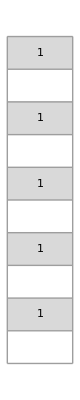
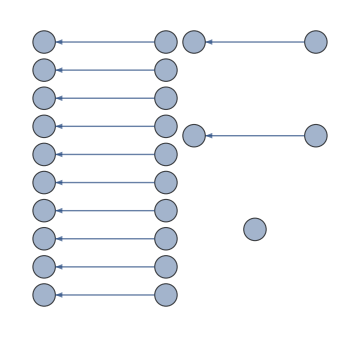
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|> : Repeating

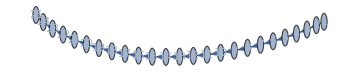
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|> : Repeating

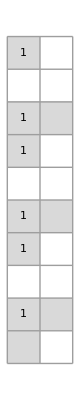
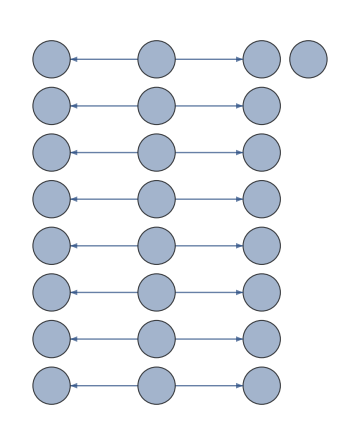
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1D

<|Index→20,QCode→23,RuleSet→{A→AA}|> : 1D

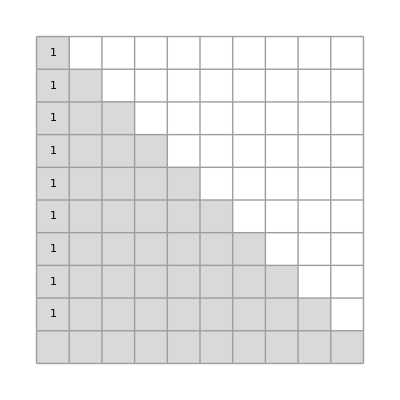
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→22,QCode→30,RuleSet→{AA→,→A}|> : Repeating

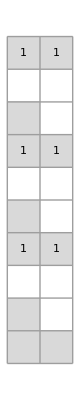
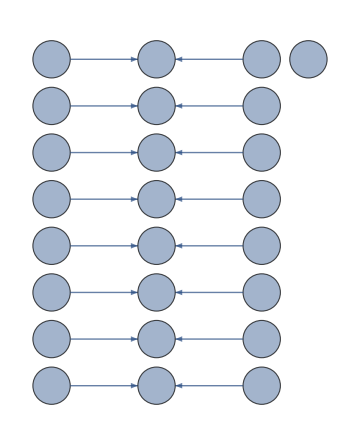
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50,QCode→033,RuleSet→{A→,→AAA}|> : Repeating

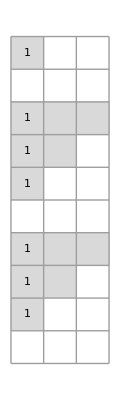
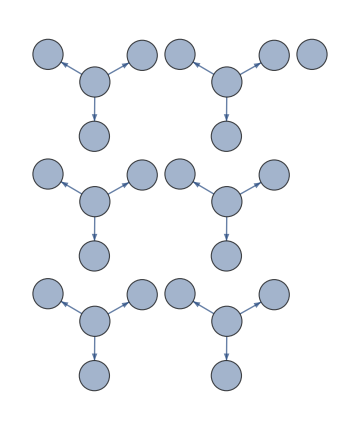
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
$debug=False;
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
While[rs["Index"]<10^2,                         (* or some other large number, stopping point *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[],  (* skip all possible *)
sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
MatchQ[sss["Verdict"],"Dead"], (* do nothing! *) ,
GuessDimension[sss];  (* if dimension can be guessed, sss will be updated accordingly *)

(* Length[ans=TestForUnusedRules[sss]]>0, rs=ans; Continue[], *)

MatchQ[sss["Verdict"],"Repeating"|"1D"],
Print[rs ," : ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->Tiny,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]]
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

## Loop to find & compare data for 2-D cases

```mathematica
$debug=False;
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
While[rs["Index"]<10^5,                         (* or some other large number, stopping point *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[],  (* skip all possible *)
sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
MatchQ[sss["Verdict"],"Dead"|"Repeating"], (* do nothing! *) ,
GuessDimension[sss];

(* Length[ans=TestForUnusedRules[sss]]>0, rs=ans; Continue[], skip more! *)

MatchQ[sss["Verdict"],"2D"],
Print[rs ," : ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->Tiny,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]]
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

Debugging

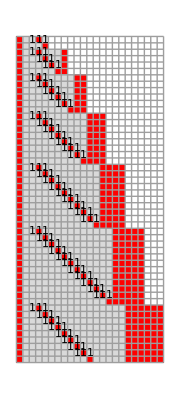


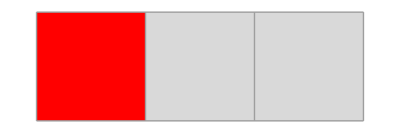
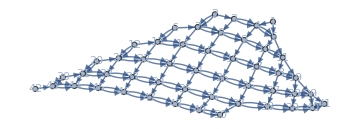
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssF2FF=SSS[{"ABA"->"AAB",""->"BAA"},"BAABA",50,SSSSize->Small,NetSize->Medium];
```

```mathematica
LeastUsedRulePositions[sssF2FF]
```

{2,6,12,20,30,42}

```mathematica
CheckDimension@MaxStateLengthPositions[sssF2FF]
```

{2D,{1,0,2},1
2
2,1 | 3 | 7 | 13 | 21 | 31 | 43 | 57 | 73 | 91 | 111 | 133
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssF2FF]
```

{2D,{1,0,2},2
4
2,2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceTally[sssF2FF]
```

{2D,{2,1,3/2},3 | 7
4 | 6
2 | 1,1 | 3 | 7 | 13 | 20 | 29 | 39 | 51 | 64 | 79
2 | 4 | 6 | 7 | 9 | 10 | 12 | 13 | 15 | 
2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 |  | }

```mathematica
CheckDimension@DistanceLastPositions[sssF2FF]
```

{2D,{1,0,2},5
6
2,5 | 11 | 19 | 29 | 41 | 55 | 71 | 89 | 109
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

### Loop to find & compare data for 3-D cases

```mathematica
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
```

<|Index→403773,QCode→34243431,RuleSet→{AB→BBA,→A}|> : {exp2,exp2,exp2,exp2} - OK

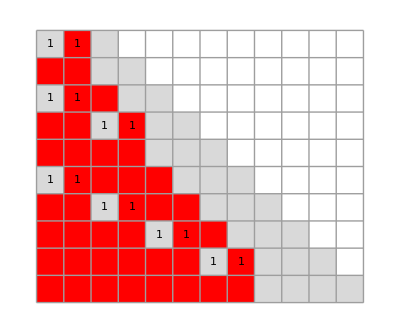

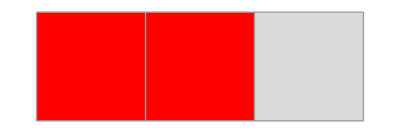
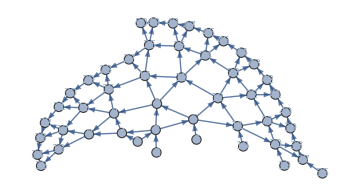
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1953648,QCode→333342431,RuleSet→{AAAAB→BA,→A}|> : {failed,failed,failed,failed} - OK

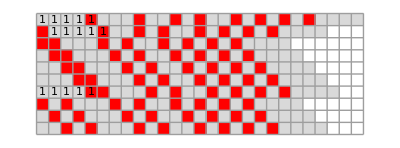
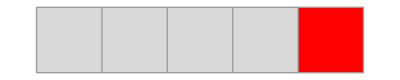

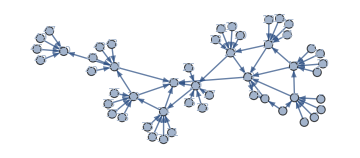
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2015478,QCode→342332241,RuleSet→{AB→AAA,A→B,→A}|> : {failed,exp2,failed,failed} - OK

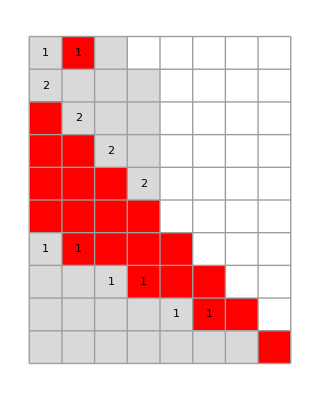

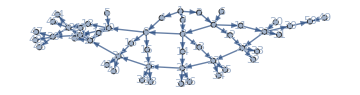
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2018701,QCode→342433134,RuleSet→{AB→BAA,→AB}|> : {exp1,exp1,failed,failed} - OK

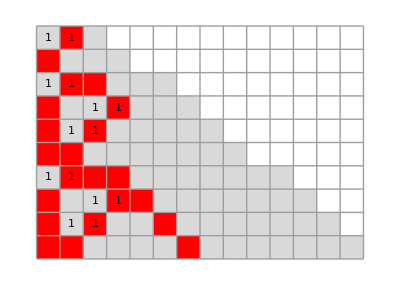
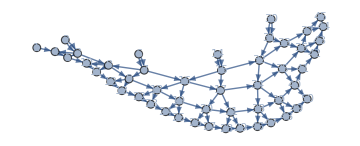
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2018705,QCode→342433143,RuleSet→{AB→BAA,→BA}|> : {exp1,exp1,failed,failed} - OK

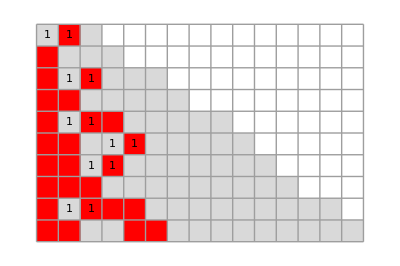
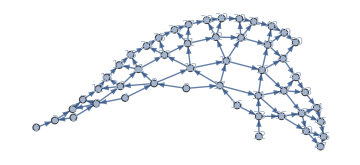
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2018865,QCode→342434313,RuleSet→{AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

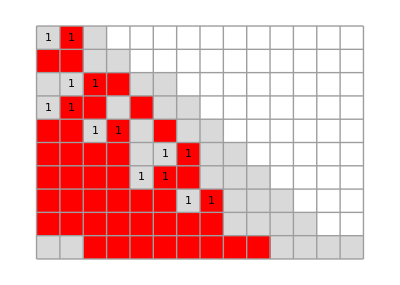
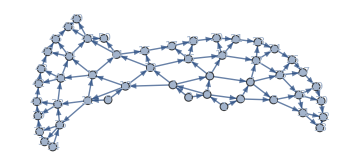
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2018867,QCode→342434320,RuleSet→{AB→BBA,A→,→A}|> : {exp2,exp2,exp2,exp2} - OK

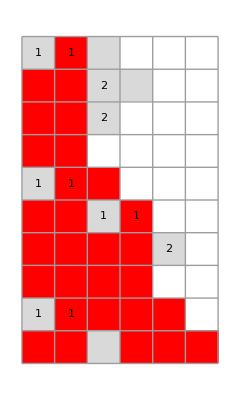
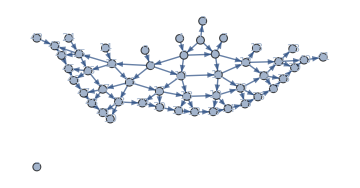
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→8997523,QCode→3134243431,RuleSet→{AA→,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

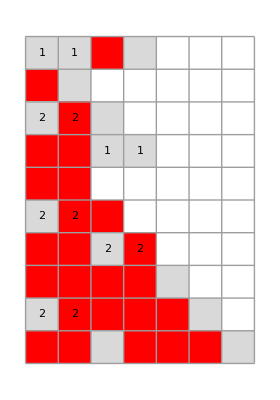
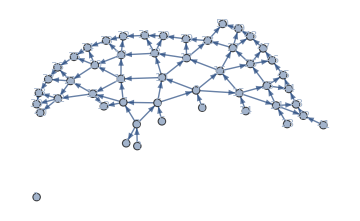
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9768248,QCode→3333424331,RuleSet→{AAAAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

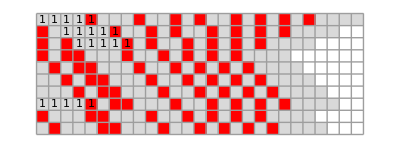
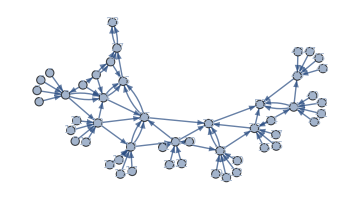
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9831373,QCode→3342434331,RuleSet→{AAB→BBAA,→A}|> : {exp2,failed,exp2,exp2} - OK

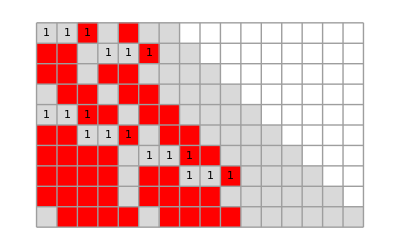
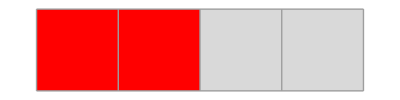
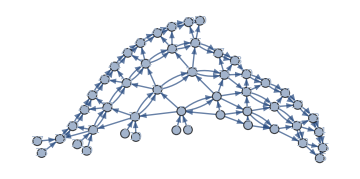
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10074503,QCode→3423224341,RuleSet→{AB→AA,A→BB,→A}|> : {failed,exp2,failed,failed} - OK

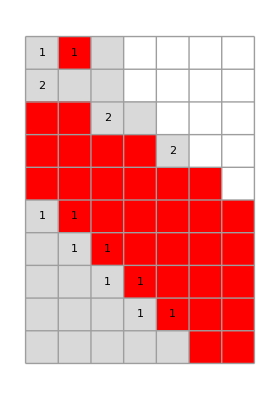
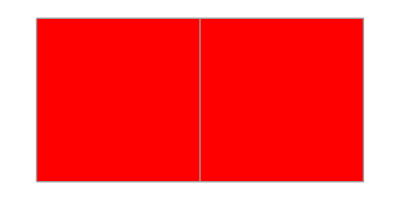
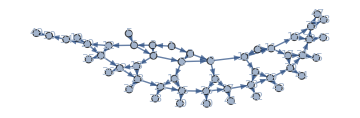
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10077390,QCode→3423322413,RuleSet→{AB→AAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

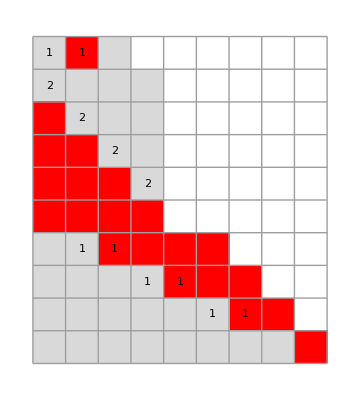
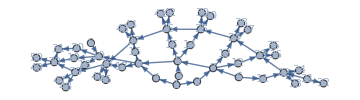
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10077978,QCode→3423332241,RuleSet→{AB→AAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

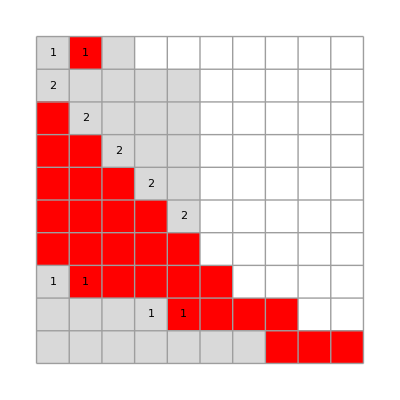
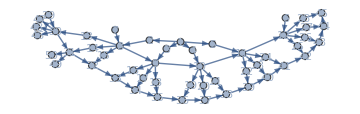
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093501,QCode→3424331334,RuleSet→{AB→BAA,→AAB}|> : {exp2,exp2,failed,failed} - OK

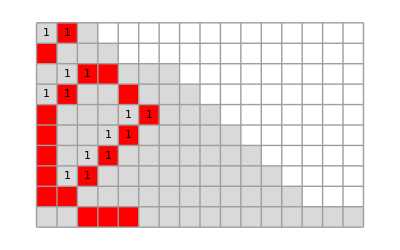
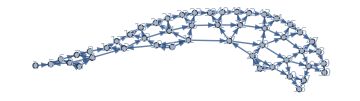
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093505,QCode→3424331343,RuleSet→{AB→BAA,→ABA}|> : {exp2,exp2,failed,failed} - OK

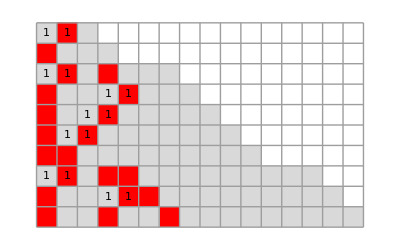
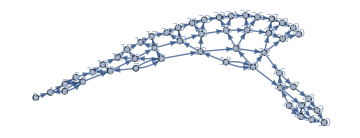
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093525,QCode→3424331433,RuleSet→{AB→BAA,→BAA}|> : {exp2,exp2,failed,failed} - OK

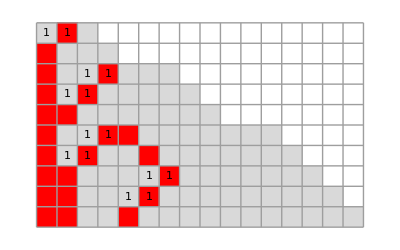
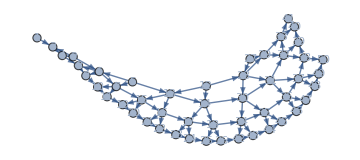
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093551,QCode→3424332034,RuleSet→{AB→BAA,A→,→AB}|> : {exp1,exp1,failed,failed} - OK

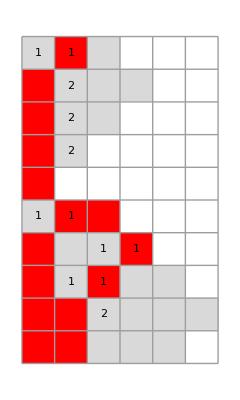
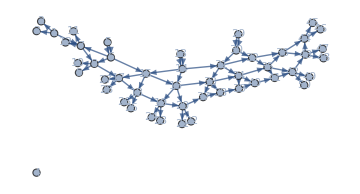
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093555,QCode→3424332043,RuleSet→{AB→BAA,A→,→BA}|> : {exp1,exp1,failed,failed} - OK

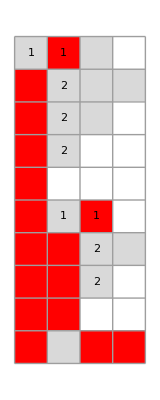
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093701,QCode→3424333134,RuleSet→{AB→BAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10093705,QCode→3424333143,RuleSet→{AB→BAAA,→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094325,QCode→3424343133,RuleSet→{AB→BBA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094326,QCode→3424343134,RuleSet→{AB→BBA,→AB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094330,QCode→3424343143,RuleSet→{AB→BBA,→BA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094335,QCode→3424343203,RuleSet→{AB→BBA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094347,QCode→3424343230,RuleSet→{AB→BBA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094354,QCode→3424343242,RuleSet→{AB→BBA,B→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10094398,QCode→3424343431,RuleSet→{AB→BBBA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→46497523,QCode→32234243431,RuleSet→{AA→A,AB→BBA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→47250498,QCode→32432342331,RuleSet→{AA→BA,AB→AAA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48060023,QCode→33134243431,RuleSet→{AAA→,AB→BBA,→A}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48830648,QCode→33333423431,RuleSet→{AAAAAB→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48830740,QCode→33333424313,RuleSet→{AAAAAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48840740,QCode→33334234313,RuleSet→{AAAAB→ABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48840748,QCode→33334234331,RuleSet→{AAAAB→ABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48841200,QCode→33334243133,RuleSet→{AAAAB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48841240,QCode→33334243313,RuleSet→{AAAAB→BAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48841248,QCode→33334243331,RuleSet→{AAAAB→BAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48893748,QCode→33342433331,RuleSet→{AAAB→BAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→48903248,QCode→33343234331,RuleSet→{AAABA→ABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49143773,QCode→33423433431,RuleSet→{AAB→ABABA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49155603,QCode→33424323241,RuleSet→{AAB→BA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49156373,QCode→33424334331,RuleSet→{AAB→BABAA,→A}|> : {exp2,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→49156865,QCode→33424343313,RuleSet→{AAB→BBAA,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50372515,QCode→34232243413,RuleSet→{AB→AA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50386950,QCode→34233224133,RuleSet→{AB→AAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50386951,QCode→34233224134,RuleSet→{AB→AAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50386955,QCode→34233224143,RuleSet→{AB→AAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50386979,QCode→34233224242,RuleSet→{AB→AAA,A→B,B→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50387003,QCode→34233224341,RuleSet→{AB→AAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50387398,QCode→34233232431,RuleSet→{AB→AAA,AA→BA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50389890,QCode→34233322413,RuleSet→{AB→AAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50389978,QCode→34233323241,RuleSet→{AB→AAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50390478,QCode→34233332241,RuleSet→{AB→AAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467501,QCode→34243313334,RuleSet→{AB→BAA,→AAAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467505,QCode→34243313343,RuleSet→{AB→BAA,→AABA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467525,QCode→34243313433,RuleSet→{AB→BAA,→ABAA}|> : {exp2,exp2,3D,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467526,QCode→34243313434,RuleSet→{AB→BAA,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467625,QCode→34243314333,RuleSet→{AB→BAA,→BAAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467626,QCode→34243314334,RuleSet→{AB→BAA,→BAB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467630,QCode→34243314343,RuleSet→{AB→BAA,→BBA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467751,QCode→34243320334,RuleSet→{AB→BAA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467755,QCode→34243320343,RuleSet→{AB→BAA,A→,→ABA}|> : {failed,exp2,exp3,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50467775,QCode→34243320433,RuleSet→{AB→BAA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468015,QCode→34243322413,RuleSet→{AB→BAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468051,QCode→34243323034,RuleSet→{AB→BAA,AA→,→AB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468055,QCode→34243323043,RuleSet→{AB→BAA,AA→,→BA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468103,QCode→34243323241,RuleSet→{AB→BAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468501,QCode→34243331334,RuleSet→{AB→BAAA,→AAB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468505,QCode→34243331343,RuleSet→{AB→BAAA,→ABA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468525,QCode→34243331433,RuleSet→{AB→BAAA,→BAA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468551,QCode→34243332034,RuleSet→{AB→BAAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468555,QCode→34243332043,RuleSet→{AB→BAAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468603,QCode→34243332241,RuleSet→{AB→BAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468701,QCode→34243333134,RuleSet→{AB→BAAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50468705,QCode→34243333143,RuleSet→{AB→BAAAA,→BA}|> : {failed,exp2,exp3,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471626,QCode→34243431334,RuleSet→{AB→BBA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471630,QCode→34243431343,RuleSet→{AB→BBA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471650,QCode→34243431433,RuleSet→{AB→BBA,→BAA}|> : {failed,failed,exp1,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471675,QCode→34243432033,RuleSet→{AB→BBA,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471676,QCode→34243432034,RuleSet→{AB→BBA,A→,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471680,QCode→34243432043,RuleSet→{AB→BBA,A→,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471704,QCode→34243432142,RuleSet→{AB→BBA,A→,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471728,QCode→34243432241,RuleSet→{AB→BBA,A→B,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471735,QCode→34243432303,RuleSet→{AB→BBA,AA→,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471743,QCode→34243432321,RuleSet→{AB→BBA,AA→A,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471747,QCode→34243432330,RuleSet→{AB→BBA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471770,QCode→34243432423,RuleSet→{AB→BBA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471990,QCode→34243434313,RuleSet→{AB→BBBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50471992,QCode→34243434320,RuleSet→{AB→BBBA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50703201,QCode→34323334134,RuleSet→{ABA→AAAB,→AB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50703205,QCode→34323334143,RuleSet→{ABA→AAAB,→BA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224922523,QCode→313423343431,RuleSet→{AA→,AB→AABBA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224937523,QCode→313424333431,RuleSet→{AA→,AB→BAABA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938075,QCode→313424343133,RuleSet→{AA→,AB→BBA,→AAA}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938076,QCode→313424343134,RuleSet→{AA→,AB→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938080,QCode→313424343143,RuleSet→{AA→,AB→BBA,→BA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938104,QCode→313424343242,RuleSet→{AA→,AB→BBA,B→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938123,QCode→313424343331,RuleSet→{AA→,AB→BBAAA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→224938148,QCode→313424343431,RuleSet→{AA→,AB→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→232487615,QCode→322342434313,RuleSet→{AA→A,AB→BBA,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→232487623,QCode→322342434331,RuleSet→{AA→A,AB→BBAA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→235949998,QCode→324234233331,RuleSet→{AA→B,AB→AAAAA,→A}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→235950023,QCode→324234233431,RuleSet→{AA→B,AB→AABA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→235950623,QCode→324234243331,RuleSet→{AA→B,AB→BAAA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→235950648,QCode→324234243431,RuleSet→{AA→B,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236252490,QCode→324323423313,RuleSet→{AA→BA,AB→AAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236252492,QCode→324323423320,RuleSet→{AA→BA,AB→AAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236252498,QCode→324323423331,RuleSet→{AA→BA,AB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236252623,QCode→324323424331,RuleSet→{AA→BA,AB→BAA,→A}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236391123,QCode→324342342331,RuleSet→{AA→BB,AB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→236403223,QCode→324343234231,RuleSet→{AA→BBA,AB→AA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→240300115,QCode→331342434313,RuleSet→{AAA→,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→241810023,QCode→332234243431,RuleSet→{AAA→A,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→242500523,QCode→332423342431,RuleSet→{AAA→B,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→242502623,QCode→332423424331,RuleSet→{AAA→B,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→243372523,QCode→333134243431,RuleSet→{AAAA→,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244142400,QCode→333333412433,RuleSet→{AAAAAAB→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244142605,QCode→333333414243,RuleSet→{AAAAAAB→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244143220,QCode→333333424223,RuleSet→{AAAAAAB→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244143248,QCode→333333424331,RuleSet→{AAAAAAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244152400,QCode→333334222433,RuleSet→{AAAAAB→A,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244152605,QCode→333334224243,RuleSet→{AAAAAB→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244153248,QCode→333334234331,RuleSet→{AAAAAB→ABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244153700,QCode→333334243133,RuleSet→{AAAAAB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244153720,QCode→333334243223,RuleSet→{AAAAAB→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244153740,QCode→333334243313,RuleSet→{AAAAAB→BAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244153748,QCode→333334243331,RuleSet→{AAAAAB→BAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244154900,QCode→333334312433,RuleSet→{AAAAABA→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244155101,QCode→333334314234,RuleSet→{AAAAABA→,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244155105,QCode→333334314243,RuleSet→{AAAAABA→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244155720,QCode→333334324223,RuleSet→{AAAAABA→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244203740,QCode→333342343313,RuleSet→{AAAAB→ABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244206200,QCode→333342433133,RuleSet→{AAAAB→BAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244206240,QCode→333342433313,RuleSet→{AAAAB→BAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244214900,QCode→333343222433,RuleSet→{AAAABA→A,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244215101,QCode→333343224234,RuleSet→{AAAABA→A,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244215105,QCode→333343224243,RuleSet→{AAAABA→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244216220,QCode→333343243223,RuleSet→{AAAABA→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244467500,QCode→333424313333,RuleSet→{AAAB→BA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244468500,QCode→333424331333,RuleSet→{AAAB→BAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244468740,QCode→333424333313,RuleSet→{AAAB→BAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244468748,QCode→333424333331,RuleSet→{AAAB→BAAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244469373,QCode→333424343331,RuleSet→{AAAB→BBAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→244516240,QCode→333432343313,RuleSet→{AAABA→ABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245702390,QCode→334233322413,RuleSet→{AAB→AAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245718501,QCode→334234331334,RuleSet→{AAB→ABAA,→AAB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245718505,QCode→334234331343,RuleSet→{AAB→ABAA,→ABA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245718525,QCode→334234331433,RuleSet→{AAB→ABAA,→BAA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245718865,QCode→334234334313,RuleSet→{AAB→ABABA,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245718871,QCode→334234334324,RuleSet→{AAB→ABABA,B→}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778003,QCode→334243232341,RuleSet→{AAB→BA,AA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778015,QCode→334243232413,RuleSet→{AAB→BA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778023,QCode→334243232431,RuleSet→{AAB→BA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778103,QCode→334243233241,RuleSet→{AAB→BA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778247,QCode→334243234330,RuleSet→{AAB→BA,ABAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245778747,QCode→334243243330,RuleSet→{AAB→BA,BAAA→,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245781001,QCode→334243331334,RuleSet→{AAB→BAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245781005,QCode→334243331343,RuleSet→{AAB→BAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245781025,QCode→334243331433,RuleSet→{AAB→BAAA,→BAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245781865,QCode→334243343313,RuleSet→{AAB→BABAA,→AA}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245781871,QCode→334243343324,RuleSet→{AAB→BABAA,B→}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245784325,QCode→334243433133,RuleSet→{AAB→BBAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245784335,QCode→334243433203,RuleSet→{AAB→BBAA,A→,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245784347,QCode→334243433230,RuleSet→{AAB→BBAA,AA→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245784354,QCode→334243433242,RuleSet→{AAB→BBAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→245784498,QCode→334243434331,RuleSet→{AAB→BBBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251862575,QCode→342322434133,RuleSet→{AB→AA,A→BB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251862576,QCode→342322434134,RuleSet→{AB→AA,A→BB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251862580,QCode→342322434143,RuleSet→{AB→AA,A→BB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251862604,QCode→342322434242,RuleSet→{AB→AA,A→BB,B→A}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251862628,QCode→342322434341,RuleSet→{AB→AA,A→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251872523,QCode→342323243431,RuleSet→{AB→AA,AA→BBA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251934750,QCode→342332241333,RuleSet→{AB→AAA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251934751,QCode→342332241334,RuleSet→{AB→AAA,A→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251934755,QCode→342332241343,RuleSet→{AB→AAA,A→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251934775,QCode→342332241433,RuleSet→{AB→AAA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251934895,QCode→342332242423,RuleSet→{AB→AAA,A→B,B→AA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251935015,QCode→342332243413,RuleSet→{AB→AAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251936990,QCode→342332324313,RuleSet→{AB→AAA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251936992,QCode→342332324320,RuleSet→{AB→AAA,AA→BA,A→,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251937003,QCode→342332324341,RuleSet→{AB→AAA,AA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949450,QCode→342333224133,RuleSet→{AB→AAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949451,QCode→342333224134,RuleSet→{AB→AAAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949455,QCode→342333224143,RuleSet→{AB→AAAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949479,QCode→342333224242,RuleSet→{AB→AAAA,A→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949503,QCode→342333224341,RuleSet→{AB→AAAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949890,QCode→342333232413,RuleSet→{AB→AAAA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949892,QCode→342333232420,RuleSet→{AB→AAAA,AA→B,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251949898,QCode→342333232431,RuleSet→{AB→AAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251952390,QCode→342333322413,RuleSet→{AB→AAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251952478,QCode→342333323241,RuleSet→{AB→AAAAA,AA→B,→A}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→251952978,QCode→342333332241,RuleSet→{AB→AAAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337501,QCode→342433133334,RuleSet→{AB→BAA,→AAAAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337505,QCode→342433133343,RuleSet→{AB→BAA,→AAABA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337525,QCode→342433133433,RuleSet→{AB→BAA,→AABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337526,QCode→342433133434,RuleSet→{AB→BAA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337625,QCode→342433134333,RuleSet→{AB→BAA,→ABAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337626,QCode→342433134334,RuleSet→{AB→BAA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252337630,QCode→342433134343,RuleSet→{AB→BAA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338125,QCode→342433143333,RuleSet→{AB→BAA,→BAAAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338126,QCode→342433143334,RuleSet→{AB→BAA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338130,QCode→342433143343,RuleSet→{AB→BAA,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338150,QCode→342433143433,RuleSet→{AB→BAA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338751,QCode→342433203334,RuleSet→{AB→BAA,A→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338755,QCode→342433203343,RuleSet→{AB→BAA,A→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338775,QCode→342433203433,RuleSet→{AB→BAA,A→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338776,QCode→342433203434,RuleSet→{AB→BAA,A→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338875,QCode→342433204333,RuleSet→{AB→BAA,A→,→BAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338876,QCode→342433204334,RuleSet→{AB→BAA,A→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252338880,QCode→342433204343,RuleSet→{AB→BAA,A→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340075,QCode→342433224133,RuleSet→{AB→BAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340076,QCode→342433224134,RuleSet→{AB→BAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340104,QCode→342433224242,RuleSet→{AB→BAA,A→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340128,QCode→342433224341,RuleSet→{AB→BAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340251,QCode→342433230334,RuleSet→{AB→BAA,AA→,→AAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340255,QCode→342433230343,RuleSet→{AB→BAA,AA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340275,QCode→342433230433,RuleSet→{AB→BAA,AA→,→BAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340451,QCode→342433232134,RuleSet→{AB→BAA,AA→A,→AB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340455,QCode→342433232143,RuleSet→{AB→BAA,AA→A,→BA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340523,QCode→342433232431,RuleSet→{AB→BAA,AA→BA,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340551,QCode→342433233034,RuleSet→{AB→BAA,AAA→,→AB}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340555,QCode→342433233043,RuleSet→{AB→BAA,AAA→,→BA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252340603,QCode→342433233241,RuleSet→{AB→BAA,AAA→B,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342505,QCode→342433313343,RuleSet→{AB→BAAA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342525,QCode→342433313433,RuleSet→{AB→BAAA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342526,QCode→342433313434,RuleSet→{AB→BAAA,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342625,QCode→342433314333,RuleSet→{AB→BAAA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342626,QCode→342433314334,RuleSet→{AB→BAAA,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342630,QCode→342433314343,RuleSet→{AB→BAAA,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342751,QCode→342433320334,RuleSet→{AB→BAAA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342755,QCode→342433320343,RuleSet→{AB→BAAA,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252342775,QCode→342433320433,RuleSet→{AB→BAAA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343051,QCode→342433323034,RuleSet→{AB→BAAA,AA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343055,QCode→342433323043,RuleSet→{AB→BAAA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343103,QCode→342433323241,RuleSet→{AB→BAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343501,QCode→342433331334,RuleSet→{AB→BAAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343505,QCode→342433331343,RuleSet→{AB→BAAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343525,QCode→342433331433,RuleSet→{AB→BAAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343551,QCode→342433332034,RuleSet→{AB→BAAAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343555,QCode→342433332043,RuleSet→{AB→BAAAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343701,QCode→342433333134,RuleSet→{AB→BAAAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252343705,QCode→342433333143,RuleSet→{AB→BAAAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358125,QCode→342434313333,RuleSet→{AB→BBA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358126,QCode→342434313334,RuleSet→{AB→BBA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358130,QCode→342434313343,RuleSet→{AB→BBA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358150,QCode→342434313433,RuleSet→{AB→BBA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358151,QCode→342434313434,RuleSet→{AB→BBA,→ABB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358250,QCode→342434314333,RuleSet→{AB→BBA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358251,QCode→342434314334,RuleSet→{AB→BBA,→BAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358255,QCode→342434314343,RuleSet→{AB→BBA,→BBA}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358376,QCode→342434320334,RuleSet→{AB→BBA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358380,QCode→342434320343,RuleSet→{AB→BBA,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358400,QCode→342434320433,RuleSet→{AB→BBA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358520,QCode→342434321423,RuleSet→{AB→BBA,A→,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358640,QCode→342434322413,RuleSet→{AB→BBA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358675,QCode→342434323033,RuleSet→{AB→BBA,AA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358676,QCode→342434323034,RuleSet→{AB→BBA,AA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358680,QCode→342434323043,RuleSet→{AB→BBA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358704,QCode→342434323142,RuleSet→{AB→BBA,AA→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358715,QCode→342434323213,RuleSet→{AB→BBA,AA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358728,QCode→342434323241,RuleSet→{AB→BBA,AA→B,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358743,QCode→342434323321,RuleSet→{AB→BBA,AAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358747,QCode→342434323330,RuleSet→{AB→BBA,AAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358850,QCode→342434324233,RuleSet→{AB→BBA,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358851,QCode→342434324234,RuleSet→{AB→BBA,B→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358855,QCode→342434324243,RuleSet→{AB→BBA,B→BA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252358879,QCode→342434324342,RuleSet→{AB→BBA,BB→A}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252359951,QCode→342434343134,RuleSet→{AB→BBBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252359955,QCode→342434343143,RuleSet→{AB→BBBA,→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252359960,QCode→342434343203,RuleSet→{AB→BBBA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252359972,QCode→342434343230,RuleSet→{AB→BBBA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252359979,QCode→342434343242,RuleSet→{AB→BBBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→252360023,QCode→342434343431,RuleSet→{AB→BBBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253138148,QCode→343134243431,RuleSet→{ABA→,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253515701,QCode→343233334134,RuleSet→{ABA→AAAAB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253515705,QCode→343233334143,RuleSet→{ABA→AAAAB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253516001,QCode→343233341334,RuleSet→{ABA→AAAB,→AAB}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253516005,QCode→343233341343,RuleSet→{ABA→AAAB,→ABA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253516025,QCode→343233341433,RuleSet→{ABA→AAAB,→BAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253516101,QCode→343233342234,RuleSet→{ABA→AAAB,A→AB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253578127,QCode→343242333340,RuleSet→{ABA→B,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253750523,QCode→343313342431,RuleSet→{ABAA→,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→253875523,QCode→343331342431,RuleSet→{ABAAA→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→254218603,QCode→343423332241,RuleSet→{ABB→AAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→254235003,QCode→343424343341,RuleSet→{ABB→BBAB,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→254235023,QCode→343424343431,RuleSet→{ABB→BBBA,→A}|> : {exp2,exp2,exp2,5D} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1124612617,QCode→3134233434320,RuleSet→{AA→,AB→AABBA,A→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1124687617,QCode→3134243334320,RuleSet→{AA→,AB→BAABA,A→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1124690425,QCode→3134243432033,RuleSet→{AA→,AB→BBA,A→,→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1124690473,QCode→3134243432231,RuleSet→{AA→,AB→BBA,A→AA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1124690617,QCode→3134243433320,RuleSet→{AA→,AB→BBAAA,A→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1125013076,QCode→3134334243134,RuleSet→{AA→,ABAB→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1125013080,QCode→3134334243143,RuleSet→{AA→,ABAB→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438075,QCode→3223424343133,RuleSet→{AA→A,AB→BBA,→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438076,QCode→3223424343134,RuleSet→{AA→A,AB→BBA,→AB}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438080,QCode→3223424343143,RuleSet→{AA→A,AB→BBA,→BA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438085,QCode→3223424343203,RuleSet→{AA→A,AB→BBA,A→,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438104,QCode→3223424343242,RuleSet→{AA→A,AB→BBA,B→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438115,QCode→3223424343313,RuleSet→{AA→A,AB→BBAA,→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438117,QCode→3223424343320,RuleSet→{AA→A,AB→BBAA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438123,QCode→3223424343331,RuleSet→{AA→A,AB→BBAAA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1162438148,QCode→3223424343431,RuleSet→{AA→A,AB→BBBA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1173450648,QCode→3234234243431,RuleSet→{AA→AB,AB→BBA,→A}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1173518123,QCode→3234243423331,RuleSet→{AA→AB,BB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1173518848,QCode→3234243434231,RuleSet→{AA→AB,BBB→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1179749992,QCode→3242342333320,RuleSet→{AA→B,AB→AAAAA,A→,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1179750117,QCode→3242342334320,RuleSet→{AA→B,AB→AABA,A→,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1179753117,QCode→3242342433320,RuleSet→{AA→B,AB→BAAA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262450,QCode→3243234233133,RuleSet→{AA→BA,AB→AAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262451,QCode→3243234233134,RuleSet→{AA→BA,AB→AAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262455,QCode→3243234233143,RuleSet→{AA→BA,AB→AAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262460,QCode→3243234233203,RuleSet→{AA→BA,AB→AAA,A→,→AA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262479,QCode→3243234233242,RuleSet→{AA→BA,AB→AAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262490,QCode→3243234233313,RuleSet→{AA→BA,AB→AAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262492,QCode→3243234233320,RuleSet→{AA→BA,AB→AAAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181262498,QCode→3243234233331,RuleSet→{AA→BA,AB→AAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181263115,QCode→3243234243313,RuleSet→{AA→BA,AB→BAA,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181263117,QCode→3243234243320,RuleSet→{AA→BA,AB→BAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181263123,QCode→3243234243331,RuleSet→{AA→BA,AB→BAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181263148,QCode→3243234243431,RuleSet→{AA→BA,AB→BBA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181732002,QCode→3243344244340,RuleSet→{AA→BAC,CB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1181955617,QCode→3243423423320,RuleSet→{AA→BB,AB→AAA,A→,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1182016115,QCode→3243432342313,RuleSet→{AA→BBA,AB→AA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1182016117,QCode→3243432342320,RuleSet→{AA→BBA,AB→AA,A→,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1182016123,QCode→3243432342331,RuleSet→{AA→BBA,AB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1182097518,QCode→3243442443421,RuleSet→{AA→BC,CB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1201237623,QCode→3313342434331,RuleSet→{AAA→,AAB→BBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1201500576,QCode→3313424343134,RuleSet→{AAA→,AB→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1201500580,QCode→3313424343143,RuleSet→{AAA→,AB→BBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1201500604,QCode→3313424343242,RuleSet→{AAA→,AB→BBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1201500648,QCode→3313424343431,RuleSet→{AAA→,AB→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1209050115,QCode→3322342434313,RuleSet→{AAA→A,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1210560023,QCode→3323234243431,RuleSet→{AAA→AA,AB→BBA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1211250523,QCode→3323423342431,RuleSet→{AAA→AB,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1211252623,QCode→3323423424331,RuleSet→{AAA→AB,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212502498,QCode→3324233423331,RuleSet→{AAA→B,AAB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212502615,QCode→3324233424313,RuleSet→{AAA→B,AAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212512523,QCode→3324234233431,RuleSet→{AAA→B,AB→AABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212513115,QCode→3324234243313,RuleSet→{AAA→B,AB→BAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212513117,QCode→3324234243320,RuleSet→{AAA→B,AB→BAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212513148,QCode→3324234243431,RuleSet→{AAA→B,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212812998,QCode→3324323342331,RuleSet→{AAA→BA,AAB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212813023,QCode→3324323342431,RuleSet→{AAA→BA,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212814998,QCode→3324323423331,RuleSet→{AAA→BA,AB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1212875498,QCode→3324332342331,RuleSet→{AAA→BAA,AB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1216862615,QCode→3331342434313,RuleSet→{AAAA→,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1218372523,QCode→3332234243431,RuleSet→{AAAA→A,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1219063023,QCode→3332423342431,RuleSet→{AAAA→B,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1219934951,QCode→3333134243134,RuleSet→{AAAAA→,AB→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1219934955,QCode→3333134243143,RuleSet→{AAAAA→,AB→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220704900,QCode→3333333412433,RuleSet→{AAAAAAAB→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705051,QCode→3333333414034,RuleSet→{AAAAAAAB→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705055,QCode→3333333414043,RuleSet→{AAAAAAAB→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705091,QCode→3333333414214,RuleSet→{AAAAAAAB→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705105,QCode→3333333414243,RuleSet→{AAAAAAAB→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705720,QCode→3333333424223,RuleSet→{AAAAAAAB→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705740,QCode→3333333424313,RuleSet→{AAAAAAAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220705748,QCode→3333333424331,RuleSet→{AAAAAAAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220712000,QCode→3333334124333,RuleSet→{AAAAAAB→,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220713003,QCode→3333334142341,RuleSet→{AAAAAAB→,B→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220715105,QCode→3333334224243,RuleSet→{AAAAAAB→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220715648,QCode→3333334233431,RuleSet→{AAAAAAB→AABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220715740,QCode→3333334234313,RuleSet→{AAAAAAB→ABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220716200,QCode→3333334243133,RuleSet→{AAAAAAB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220716220,QCode→3333334243223,RuleSet→{AAAAAAB→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220716248,QCode→3333334243331,RuleSet→{AAAAAAB→BAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717400,QCode→3333334312433,RuleSet→{AAAAAABA→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717551,QCode→3333334314034,RuleSet→{AAAAAABA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717555,QCode→3333334314043,RuleSet→{AAAAAABA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717591,QCode→3333334314214,RuleSet→{AAAAAABA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717601,QCode→3333334314234,RuleSet→{AAAAAABA→,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220717605,QCode→3333334314243,RuleSet→{AAAAAABA→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220718220,QCode→3333334324223,RuleSet→{AAAAAABA→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220750603,QCode→3333341343241,RuleSet→{AAAAAB→,ABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220753003,QCode→3333341432341,RuleSet→{AAAAAB→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220765740,QCode→3333342334313,RuleSet→{AAAAAB→AABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220765748,QCode→3333342334331,RuleSet→{AAAAAB→AABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220766200,QCode→3333342343133,RuleSet→{AAAAAB→ABA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220766220,QCode→3333342343223,RuleSet→{AAAAAB→ABA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220766240,QCode→3333342343313,RuleSet→{AAAAAB→ABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220766248,QCode→3333342343331,RuleSet→{AAAAAB→ABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220768500,QCode→3333342431333,RuleSet→{AAAAAB→BA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220768700,QCode→3333342433133,RuleSet→{AAAAAB→BAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220768740,QCode→3333342433313,RuleSet→{AAAAAB→BAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220774500,QCode→3333343124333,RuleSet→{AAAAABA→,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220775501,QCode→3333343142334,RuleSet→{AAAAABA→,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220775525,QCode→3333343142433,RuleSet→{AAAAABA→,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220777601,QCode→3333343224234,RuleSet→{AAAAABA→A,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220777605,QCode→3333343224243,RuleSet→{AAAAABA→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220778720,QCode→3333343243223,RuleSet→{AAAAABA→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220780051,QCode→3333343314034,RuleSet→{AAAAABAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220780055,QCode→3333343314043,RuleSet→{AAAAABAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220780091,QCode→3333343314214,RuleSet→{AAAAABAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220780727,QCode→3333343324240,RuleSet→{AAAAABAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220938103,QCode→3333413343241,RuleSet→{AAAAB→,AABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1220940503,QCode→3333413432341,RuleSet→{AAAAB→,ABA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221016200,QCode→3333423343133,RuleSet→{AAAAB→AABA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221018500,QCode→3333423431333,RuleSet→{AAAAB→ABA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221018600,QCode→3333423432233,RuleSet→{AAAAB→ABA,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221018700,QCode→3333423433133,RuleSet→{AAAAB→ABAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221018720,QCode→3333423433223,RuleSet→{AAAAB→ABAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221018748,QCode→3333423433331,RuleSet→{AAAAB→ABAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221030000,QCode→3333424313333,RuleSet→{AAAAB→BA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221030726,QCode→3333424324234,RuleSet→{AAAAB→BA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221031000,QCode→3333424331333,RuleSet→{AAAAB→BAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221031100,QCode→3333424332233,RuleSet→{AAAAB→BAA,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221031200,QCode→3333424333133,RuleSet→{AAAAB→BAAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221031248,QCode→3333424333331,RuleSet→{AAAAB→BAAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221062478,QCode→3333431333241,RuleSet→{AAAABA→,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221065503,QCode→3333431432341,RuleSet→{AAAABA→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221078248,QCode→3333432334331,RuleSet→{AAAABA→AABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221078748,QCode→3333432343331,RuleSet→{AAAABA→ABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221092551,QCode→3333433314034,RuleSet→{AAAABAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221092555,QCode→3333433314043,RuleSet→{AAAABAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221092591,QCode→3333433314214,RuleSet→{AAAABAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1221093227,QCode→3333433324240,RuleSet→{AAAABAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222268727,QCode→3334233433240,RuleSet→{AAAB→AABAA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222268871,QCode→3334233434324,RuleSet→{AAAB→AABBA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222281373,QCode→3334234334331,RuleSet→{AAAB→ABABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222281854,QCode→3334234343242,RuleSet→{AAAB→ABBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222341126,QCode→3334243242334,RuleSet→{AAAB→BA,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222341130,QCode→3334243242343,RuleSet→{AAAB→BA,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222341247,QCode→3334243243330,RuleSet→{AAAB→BA,BAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222342500,QCode→3334243313333,RuleSet→{AAAB→BAA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222343110,QCode→3334243323303,RuleSet→{AAAB→BAA,AAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222343226,QCode→3334243324234,RuleSet→{AAAB→BAA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222343740,QCode→3334243333313,RuleSet→{AAAB→BAAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222344373,QCode→3334243343331,RuleSet→{AAAB→BABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222346770,QCode→3334243432423,RuleSet→{AAAB→BBA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222346865,QCode→3334243433313,RuleSet→{AAAB→BBAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222581200,QCode→3334323433133,RuleSet→{AAABA→ABAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222581220,QCode→3334323433223,RuleSet→{AAABA→ABAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222655051,QCode→3334333314034,RuleSet→{AAABAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222655055,QCode→3334333314043,RuleSet→{AAABAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222655091,QCode→3334333314214,RuleSet→{AAABAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222655727,QCode→3334333324240,RuleSet→{AAABAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1222728103,QCode→3334343133241,RuleSet→{AAABBA→,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228497515,QCode→3342332243413,RuleSet→{AAB→AAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228499398,QCode→3342332323431,RuleSet→{AAB→AAA,AA→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228511950,QCode→3342333224133,RuleSet→{AAB→AAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228512378,QCode→3342333232341,RuleSet→{AAB→AAAA,AA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228512398,QCode→3342333232431,RuleSet→{AAB→AAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228514890,QCode→3342333322413,RuleSet→{AAB→AAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228514978,QCode→3342333323241,RuleSet→{AAB→AAAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228590515,QCode→3342343232413,RuleSet→{AAB→ABA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228592501,QCode→3342343313334,RuleSet→{AAB→ABAA,→AAAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228592505,QCode→3342343313343,RuleSet→{AAB→ABAA,→AABA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228592525,QCode→3342343313433,RuleSet→{AAB→ABAA,→ABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228592625,QCode→3342343314333,RuleSet→{AAB→ABAA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228593001,QCode→3342343322334,RuleSet→{AAB→ABAA,A→AAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228593015,QCode→3342343322413,RuleSet→{AAB→ABAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228593501,QCode→3342343331334,RuleSet→{AAB→ABAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228593505,QCode→3342343331343,RuleSet→{AAB→ABAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228593525,QCode→3342343331433,RuleSet→{AAB→ABAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228594325,QCode→3342343343133,RuleSet→{AAB→ABABA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228594345,QCode→3342343343223,RuleSet→{AAB→ABABA,A→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228594347,QCode→3342343343230,RuleSet→{AAB→ABABA,AA→,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228594354,QCode→3342343343242,RuleSet→{AAB→ABABA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228596835,QCode→3342343433203,RuleSet→{AAB→ABBAA,A→,→AA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890003,QCode→3342432323341,RuleSet→{AAB→BA,AA→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890015,QCode→3342432323413,RuleSet→{AAB→BA,AA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890023,QCode→3342432323431,RuleSet→{AAB→BA,AA→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890075,QCode→3342432324133,RuleSet→{AAB→BA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890115,QCode→3342432324313,RuleSet→{AAB→BA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890128,QCode→3342432324341,RuleSet→{AAB→BA,AA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890503,QCode→3342432332341,RuleSet→{AAB→BA,AAA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890515,QCode→3342432332413,RuleSet→{AAB→BA,AAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890523,QCode→3342432332431,RuleSet→{AAB→BA,AAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228890603,QCode→3342432333241,RuleSet→{AAB→BA,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228891235,QCode→3342432343303,RuleSet→{AAB→BA,ABAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228891243,QCode→3342432343321,RuleSet→{AAB→BA,ABAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228893735,QCode→3342432433303,RuleSet→{AAB→BA,BAAA→,→AA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228893743,QCode→3342432433321,RuleSet→{AAB→BA,BAAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228893747,QCode→3342432433330,RuleSet→{AAB→BA,BAAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228893872,QCode→3342432434330,RuleSet→{AAB→BA,BBAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905001,QCode→3342433313334,RuleSet→{AAB→BAAA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905005,QCode→3342433313343,RuleSet→{AAB→BAAA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905025,QCode→3342433313433,RuleSet→{AAB→BAAA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905125,QCode→3342433314333,RuleSet→{AAB→BAAA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905515,QCode→3342433322413,RuleSet→{AAB→BAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228905603,QCode→3342433323241,RuleSet→{AAB→BAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228906001,QCode→3342433331334,RuleSet→{AAB→BAAAA,→AAB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228906005,QCode→3342433331343,RuleSet→{AAB→BAAAA,→ABA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228906025,QCode→3342433331433,RuleSet→{AAB→BAAAA,→BAA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909325,QCode→3342433433133,RuleSet→{AAB→BABAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909335,QCode→3342433433203,RuleSet→{AAB→BABAA,A→,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909345,QCode→3342433433223,RuleSet→{AAB→BABAA,A→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909347,QCode→3342433433230,RuleSet→{AAB→BABAA,AA→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909354,QCode→3342433433242,RuleSet→{AAB→BABAA,B→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228909498,QCode→3342433434331,RuleSet→{AAB→BABBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921625,QCode→3342434331333,RuleSet→{AAB→BBAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921626,QCode→3342434331334,RuleSet→{AAB→BBAA,→AAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921630,QCode→3342434331343,RuleSet→{AAB→BBAA,→ABA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921650,QCode→3342434331433,RuleSet→{AAB→BBAA,→BAA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921675,QCode→3342434332033,RuleSet→{AAB→BBAA,A→,→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921725,QCode→3342434332233,RuleSet→{AAB→BBAA,A→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921735,QCode→3342434332303,RuleSet→{AAB→BBAA,AA→,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921743,QCode→3342434332321,RuleSet→{AAB→BBAA,AA→A,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921747,QCode→3342434332330,RuleSet→{AAB→BBAA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921770,QCode→3342434332423,RuleSet→{AAB→BBAA,B→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921835,QCode→3342434333203,RuleSet→{AAB→BBAAA,A→,→AA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228921998,QCode→3342434334331,RuleSet→{AAB→BBABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1228922490,QCode→3342434343313,RuleSet→{AAB→BBBAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230093873,QCode→3343234334331,RuleSet→{AABA→ABABAA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230140627,QCode→3343242333340,RuleSet→{AABA→B,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230156873,QCode→3343243343331,RuleSet→{AABA→BABAAA,→A}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230158752,QCode→3343243423340,RuleSet→{AABA→BB,AAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230315115,QCode→3343313424313,RuleSet→{AABAA→,AB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230327516,QCode→3343314323414,RuleSet→{AABAA→,BA→AB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230403127,QCode→3343324233340,RuleSet→{AABAA→B,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230467551,QCode→3343333314034,RuleSet→{AABAAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230467555,QCode→3343333314043,RuleSet→{AABAAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230467591,QCode→3343333314214,RuleSet→{AABAAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1230468227,QCode→3343333324240,RuleSet→{AABAAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259312875,QCode→3423224341333,RuleSet→{AB→AA,A→BB,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259312876,QCode→3423224341334,RuleSet→{AB→AA,A→BB,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259312880,QCode→3423224341343,RuleSet→{AB→AA,A→BB,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259312900,QCode→3423224341433,RuleSet→{AB→AA,A→BB,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259313020,QCode→3423224342423,RuleSet→{AB→AA,A→BB,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259313140,QCode→3423224343413,RuleSet→{AB→AA,A→BBB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259362615,QCode→3423232434313,RuleSet→{AB→AA,AA→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259362617,QCode→3423232434320,RuleSet→{AB→AA,AA→BBA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259362628,QCode→3423232434341,RuleSet→{AB→AA,AA→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673750,QCode→3423322413333,RuleSet→{AB→AAA,A→B,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673751,QCode→3423322413334,RuleSet→{AB→AAA,A→B,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673755,QCode→3423322413343,RuleSet→{AB→AAA,A→B,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673775,QCode→3423322413433,RuleSet→{AB→AAA,A→B,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673776,QCode→3423322413434,RuleSet→{AB→AAA,A→B,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673875,QCode→3423322414333,RuleSet→{AB→AAA,A→B,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673876,QCode→3423322414334,RuleSet→{AB→AAA,A→B,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259673880,QCode→3423322414343,RuleSet→{AB→AAA,A→B,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259674475,QCode→3423322424233,RuleSet→{AB→AAA,A→B,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259674476,QCode→3423322424234,RuleSet→{AB→AAA,A→B,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259674480,QCode→3423322424243,RuleSet→{AB→AAA,A→B,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259674504,QCode→3423322424342,RuleSet→{AB→AAA,A→B,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259675075,QCode→3423322434133,RuleSet→{AB→AAA,A→BB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259675076,QCode→3423322434134,RuleSet→{AB→AAA,A→BB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259675080,QCode→3423322434143,RuleSet→{AB→AAA,A→BB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259675104,QCode→3423322434242,RuleSet→{AB→AAA,A→BB,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259675128,QCode→3423322434341,RuleSet→{AB→AAA,A→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259684950,QCode→3423323243133,RuleSet→{AB→AAA,AA→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259684951,QCode→3423323243134,RuleSet→{AB→AAA,AA→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259684955,QCode→3423323243143,RuleSet→{AB→AAA,AA→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259684960,QCode→3423323243203,RuleSet→{AB→AAA,AA→BA,A→,→AA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259684979,QCode→3423323243242,RuleSet→{AB→AAA,AA→BA,B→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259685015,QCode→3423323243413,RuleSet→{AB→AAA,AA→BB,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259685017,QCode→3423323243420,RuleSet→{AB→AAA,AA→BB,A→,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259685023,QCode→3423323243431,RuleSet→{AB→AAA,AA→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259686998,QCode→3423323324331,RuleSet→{AB→AAA,AAA→BAA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259687003,QCode→3423323324341,RuleSet→{AB→AAA,AAA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747250,QCode→3423332241333,RuleSet→{AB→AAAA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747251,QCode→3423332241334,RuleSet→{AB→AAAA,A→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747255,QCode→3423332241343,RuleSet→{AB→AAAA,A→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747275,QCode→3423332241433,RuleSet→{AB→AAAA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747395,QCode→3423332242423,RuleSet→{AB→AAAA,A→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259747515,QCode→3423332243413,RuleSet→{AB→AAAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749450,QCode→3423332324133,RuleSet→{AB→AAAA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749451,QCode→3423332324134,RuleSet→{AB→AAAA,AA→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749455,QCode→3423332324143,RuleSet→{AB→AAAA,AA→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749460,QCode→3423332324203,RuleSet→{AB→AAAA,AA→B,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749479,QCode→3423332324242,RuleSet→{AB→AAAA,AA→B,B→A}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749490,QCode→3423332324313,RuleSet→{AB→AAAA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749492,QCode→3423332324320,RuleSet→{AB→AAAA,AA→BA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749503,QCode→3423332324341,RuleSet→{AB→AAAA,AA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259749898,QCode→3423332332431,RuleSet→{AB→AAAA,AAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259761950,QCode→3423333224133,RuleSet→{AB→AAAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259761951,QCode→3423333224134,RuleSet→{AB→AAAAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259761955,QCode→3423333224143,RuleSet→{AB→AAAAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259761979,QCode→3423333224242,RuleSet→{AB→AAAAA,A→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259762003,QCode→3423333224341,RuleSet→{AB→AAAAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259762390,QCode→3423333232413,RuleSet→{AB→AAAAA,AA→B,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259762392,QCode→3423333232420,RuleSet→{AB→AAAAA,AA→B,A→,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259762398,QCode→3423333232431,RuleSet→{AB→AAAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259762478,QCode→3423333233241,RuleSet→{AB→AAAAA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259764890,QCode→3423333322413,RuleSet→{AB→AAAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259764978,QCode→3423333323241,RuleSet→{AB→AAAAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1259765478,QCode→3423333332241,RuleSet→{AB→AAAAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261626875,QCode→3424322413333,RuleSet→{AB→BA,A→B,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261640551,QCode→3424323333034,RuleSet→{AB→BA,AAAAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261640555,QCode→3424323333043,RuleSet→{AB→BA,AAAAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261656175,QCode→3424324333033,RuleSet→{AB→BA,BAAA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687501,QCode→3424331333334,RuleSet→{AB→BAA,→AAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687505,QCode→3424331333343,RuleSet→{AB→BAA,→AAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687525,QCode→3424331333433,RuleSet→{AB→BAA,→AAABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687526,QCode→3424331333434,RuleSet→{AB→BAA,→AAABB}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687625,QCode→3424331334333,RuleSet→{AB→BAA,→AABAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687626,QCode→3424331334334,RuleSet→{AB→BAA,→AABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261687630,QCode→3424331334343,RuleSet→{AB→BAA,→AABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261688125,QCode→3424331343333,RuleSet→{AB→BAA,→ABAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261688126,QCode→3424331343334,RuleSet→{AB→BAA,→ABAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261688130,QCode→3424331343343,RuleSet→{AB→BAA,→ABABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261688150,QCode→3424331343433,RuleSet→{AB→BAA,→ABBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261688151,QCode→3424331343434,RuleSet→{AB→BAA,→ABBB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690625,QCode→3424331433333,RuleSet→{AB→BAA,→BAAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690626,QCode→3424331433334,RuleSet→{AB→BAA,→BAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690630,QCode→3424331433343,RuleSet→{AB→BAA,→BAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690650,QCode→3424331433433,RuleSet→{AB→BAA,→BABAA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690651,QCode→3424331433434,RuleSet→{AB→BAA,→BABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690750,QCode→3424331434333,RuleSet→{AB→BAA,→BBAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690751,QCode→3424331434334,RuleSet→{AB→BAA,→BBAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261690755,QCode→3424331434343,RuleSet→{AB→BAA,→BBBA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693751,QCode→3424332033334,RuleSet→{AB→BAA,A→,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693755,QCode→3424332033343,RuleSet→{AB→BAA,A→,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693775,QCode→3424332033433,RuleSet→{AB→BAA,A→,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693776,QCode→3424332033434,RuleSet→{AB→BAA,A→,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693875,QCode→3424332034333,RuleSet→{AB→BAA,A→,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693876,QCode→3424332034334,RuleSet→{AB→BAA,A→,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261693880,QCode→3424332034343,RuleSet→{AB→BAA,A→,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261694375,QCode→3424332043333,RuleSet→{AB→BAA,A→,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261694376,QCode→3424332043334,RuleSet→{AB→BAA,A→,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261694380,QCode→3424332043343,RuleSet→{AB→BAA,A→,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261694400,QCode→3424332043433,RuleSet→{AB→BAA,A→,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261700375,QCode→3424332241333,RuleSet→{AB→BAA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261700376,QCode→3424332241334,RuleSet→{AB→BAA,A→B,→AAB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261700380,QCode→3424332241343,RuleSet→{AB→BAA,A→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261700400,QCode→3424332241433,RuleSet→{AB→BAA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701251,QCode→3424332303334,RuleSet→{AB→BAA,AA→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701255,QCode→3424332303343,RuleSet→{AB→BAA,AA→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701275,QCode→3424332303433,RuleSet→{AB→BAA,AA→,→ABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701276,QCode→3424332303434,RuleSet→{AB→BAA,AA→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701375,QCode→3424332304333,RuleSet→{AB→BAA,AA→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701376,QCode→3424332304334,RuleSet→{AB→BAA,AA→,→BAB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261701380,QCode→3424332304343,RuleSet→{AB→BAA,AA→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702251,QCode→3424332321334,RuleSet→{AB→BAA,AA→A,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702255,QCode→3424332321343,RuleSet→{AB→BAA,AA→A,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702275,QCode→3424332321433,RuleSet→{AB→BAA,AA→A,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702301,QCode→3424332322034,RuleSet→{AB→BAA,AA→A,A→,→AB}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702305,QCode→3424332322043,RuleSet→{AB→BAA,AA→A,A→,→BA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702353,QCode→3424332322241,RuleSet→{AB→BAA,AA→A,A→B,→A}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702580,QCode→3424332324143,RuleSet→{AB→BAA,AA→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702604,QCode→3424332324242,RuleSet→{AB→BAA,AA→B,B→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702615,QCode→3424332324313,RuleSet→{AB→BAA,AA→BA,→AA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702617,QCode→3424332324320,RuleSet→{AB→BAA,AA→BA,A→,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702628,QCode→3424332324341,RuleSet→{AB→BAA,AA→BB,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702751,QCode→3424332330334,RuleSet→{AB→BAA,AAA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702755,QCode→3424332330343,RuleSet→{AB→BAA,AAA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702775,QCode→3424332330433,RuleSet→{AB→BAA,AAA→,→BAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702801,QCode→3424332331034,RuleSet→{AB→BAA,AAA→,A→,→AB}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702805,QCode→3424332331043,RuleSet→{AB→BAA,AAA→,A→,→BA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702853,QCode→3424332331241,RuleSet→{AB→BAA,AAA→,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702951,QCode→3424332332134,RuleSet→{AB→BAA,AAA→A,→AB}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261702955,QCode→3424332332143,RuleSet→{AB→BAA,AAA→A,→BA}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261703003,QCode→3424332332341,RuleSet→{AB→BAA,AAA→AB,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261703017,QCode→3424332332420,RuleSet→{AB→BAA,AAA→B,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261703051,QCode→3424332333034,RuleSet→{AB→BAA,AAAA→,→AB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261703055,QCode→3424332333043,RuleSet→{AB→BAA,AAAA→,→BA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261703103,QCode→3424332333241,RuleSet→{AB→BAA,AAAA→B,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261705651,QCode→3424332423434,RuleSet→{AB→BAA,B→ABB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261705751,QCode→3424332424334,RuleSet→{AB→BAA,B→BAB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261705755,QCode→3424332424343,RuleSet→{AB→BAA,B→BBA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712501,QCode→3424333133334,RuleSet→{AB→BAAA,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712505,QCode→3424333133343,RuleSet→{AB→BAAA,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712525,QCode→3424333133433,RuleSet→{AB→BAAA,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712526,QCode→3424333133434,RuleSet→{AB→BAAA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712625,QCode→3424333134333,RuleSet→{AB→BAAA,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712626,QCode→3424333134334,RuleSet→{AB→BAAA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261712630,QCode→3424333134343,RuleSet→{AB→BAAA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713125,QCode→3424333143333,RuleSet→{AB→BAAA,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713126,QCode→3424333143334,RuleSet→{AB→BAAA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713130,QCode→3424333143343,RuleSet→{AB→BAAA,→BABA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713150,QCode→3424333143433,RuleSet→{AB→BAAA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713751,QCode→3424333203334,RuleSet→{AB→BAAA,A→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713755,QCode→3424333203343,RuleSet→{AB→BAAA,A→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713775,QCode→3424333203433,RuleSet→{AB→BAAA,A→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713776,QCode→3424333203434,RuleSet→{AB→BAAA,A→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713875,QCode→3424333204333,RuleSet→{AB→BAAA,A→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713876,QCode→3424333204334,RuleSet→{AB→BAAA,A→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261713880,QCode→3424333204343,RuleSet→{AB→BAAA,A→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715080,QCode→3424333224143,RuleSet→{AB→BAAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715251,QCode→3424333230334,RuleSet→{AB→BAAA,AA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715255,QCode→3424333230343,RuleSet→{AB→BAAA,AA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715275,QCode→3424333230433,RuleSet→{AB→BAAA,AA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715301,QCode→3424333231034,RuleSet→{AB→BAAA,AA→,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715305,QCode→3424333231043,RuleSet→{AB→BAAA,AA→,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715353,QCode→3424333231241,RuleSet→{AB→BAAA,AA→,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715451,QCode→3424333232134,RuleSet→{AB→BAAA,AA→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715455,QCode→3424333232143,RuleSet→{AB→BAAA,AA→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715515,QCode→3424333232413,RuleSet→{AB→BAAA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715517,QCode→3424333232420,RuleSet→{AB→BAAA,AA→B,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715551,QCode→3424333233034,RuleSet→{AB→BAAA,AAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715555,QCode→3424333233043,RuleSet→{AB→BAAA,AAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261715603,QCode→3424333233241,RuleSet→{AB→BAAA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261716268,QCode→3424333243421,RuleSet→{AB→BAAA,BB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717501,QCode→3424333313334,RuleSet→{AB→BAAAA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717505,QCode→3424333313343,RuleSet→{AB→BAAAA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717525,QCode→3424333313433,RuleSet→{AB→BAAAA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717526,QCode→3424333313434,RuleSet→{AB→BAAAA,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717625,QCode→3424333314333,RuleSet→{AB→BAAAA,→BAAA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717626,QCode→3424333314334,RuleSet→{AB→BAAAA,→BAB}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717630,QCode→3424333314343,RuleSet→{AB→BAAAA,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717751,QCode→3424333320334,RuleSet→{AB→BAAAA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717755,QCode→3424333320343,RuleSet→{AB→BAAAA,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261717775,QCode→3424333320433,RuleSet→{AB→BAAAA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718051,QCode→3424333323034,RuleSet→{AB→BAAAA,AA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718055,QCode→3424333323043,RuleSet→{AB→BAAAA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718501,QCode→3424333331334,RuleSet→{AB→BAAAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718505,QCode→3424333331343,RuleSet→{AB→BAAAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718525,QCode→3424333331433,RuleSet→{AB→BAAAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718551,QCode→3424333332034,RuleSet→{AB→BAAAAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718555,QCode→3424333332043,RuleSet→{AB→BAAAAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718701,QCode→3424333333134,RuleSet→{AB→BAAAAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261718705,QCode→3424333333143,RuleSet→{AB→BAAAAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261790625,QCode→3424343133333,RuleSet→{AB→BBA,→AAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261790626,QCode→3424343133334,RuleSet→{AB→BBA,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261790651,QCode→3424343133434,RuleSet→{AB→BBA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261790751,QCode→3424343134334,RuleSet→{AB→BBA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261790755,QCode→3424343134343,RuleSet→{AB→BBA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791251,QCode→3424343143334,RuleSet→{AB→BBA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791255,QCode→3424343143343,RuleSet→{AB→BBA,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791275,QCode→3424343143433,RuleSet→{AB→BBA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791875,QCode→3424343203333,RuleSet→{AB→BBA,A→,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791876,QCode→3424343203334,RuleSet→{AB→BBA,A→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791880,QCode→3424343203343,RuleSet→{AB→BBA,A→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791900,QCode→3424343203433,RuleSet→{AB→BBA,A→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261791901,QCode→3424343203434,RuleSet→{AB→BBA,A→,→ABB}|> : {exp1,exp1,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792000,QCode→3424343204333,RuleSet→{AB→BBA,A→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792001,QCode→3424343204334,RuleSet→{AB→BBA,A→,→BAB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792005,QCode→3424343204343,RuleSet→{AB→BBA,A→,→BBA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792600,QCode→3424343214233,RuleSet→{AB→BBA,A→,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792601,QCode→3424343214234,RuleSet→{AB→BBA,A→,B→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792605,QCode→3424343214243,RuleSet→{AB→BBA,A→,B→BA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261792629,QCode→3424343214342,RuleSet→{AB→BBA,A→,BB→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793200,QCode→3424343224133,RuleSet→{AB→BBA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793201,QCode→3424343224134,RuleSet→{AB→BBA,A→B,→AB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793205,QCode→3424343224143,RuleSet→{AB→BBA,A→B,→BA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793229,QCode→3424343224242,RuleSet→{AB→BBA,A→B,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793253,QCode→3424343224341,RuleSet→{AB→BBA,A→BB,→A}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793375,QCode→3424343230333,RuleSet→{AB→BBA,AA→,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793376,QCode→3424343230334,RuleSet→{AB→BBA,AA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793380,QCode→3424343230343,RuleSet→{AB→BBA,AA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793400,QCode→3424343230433,RuleSet→{AB→BBA,AA→,→BAA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793425,QCode→3424343231033,RuleSet→{AB→BBA,AA→,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793473,QCode→3424343231231,RuleSet→{AB→BBA,AA→,A→AA,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793520,QCode→3424343231423,RuleSet→{AB→BBA,AA→,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793575,QCode→3424343232133,RuleSet→{AB→BBA,AA→A,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793576,QCode→3424343232134,RuleSet→{AB→BBA,AA→A,→AB}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793580,QCode→3424343232143,RuleSet→{AB→BBA,AA→A,→BA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793585,QCode→3424343232203,RuleSet→{AB→BBA,AA→A,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793604,QCode→3424343232242,RuleSet→{AB→BBA,AA→A,B→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793628,QCode→3424343232341,RuleSet→{AB→BBA,AA→AB,→A}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793640,QCode→3424343232413,RuleSet→{AB→BBA,AA→B,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793648,QCode→3424343232431,RuleSet→{AB→BBA,AA→BA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793675,QCode→3424343233033,RuleSet→{AB→BBA,AAA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793676,QCode→3424343233034,RuleSet→{AB→BBA,AAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793680,QCode→3424343233043,RuleSet→{AB→BBA,AAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793704,QCode→3424343233142,RuleSet→{AB→BBA,AAA→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793715,QCode→3424343233213,RuleSet→{AB→BBA,AAA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793723,QCode→3424343233231,RuleSet→{AB→BBA,AAA→AA,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793728,QCode→3424343233241,RuleSet→{AB→BBA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793735,QCode→3424343233303,RuleSet→{AB→BBA,AAAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261793743,QCode→3424343233321,RuleSet→{AB→BBA,AAAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794250,QCode→3424343242333,RuleSet→{AB→BBA,B→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794251,QCode→3424343242334,RuleSet→{AB→BBA,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794255,QCode→3424343242343,RuleSet→{AB→BBA,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794275,QCode→3424343242433,RuleSet→{AB→BBA,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794301,QCode→3424343243034,RuleSet→{AB→BBA,BA→,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794329,QCode→3424343243142,RuleSet→{AB→BBA,BA→,B→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794353,QCode→3424343243241,RuleSet→{AB→BBA,BA→B,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794395,QCode→3424343243423,RuleSet→{AB→BBA,BB→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261794397,QCode→3424343243430,RuleSet→{AB→BBA,BBA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799750,QCode→3424343431333,RuleSet→{AB→BBBA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799751,QCode→3424343431334,RuleSet→{AB→BBBA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799755,QCode→3424343431343,RuleSet→{AB→BBBA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799775,QCode→3424343431433,RuleSet→{AB→BBBA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799800,QCode→3424343432033,RuleSet→{AB→BBBA,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799801,QCode→3424343432034,RuleSet→{AB→BBBA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799805,QCode→3424343432043,RuleSet→{AB→BBBA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799829,QCode→3424343432142,RuleSet→{AB→BBBA,A→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799853,QCode→3424343432241,RuleSet→{AB→BBBA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799860,QCode→3424343432303,RuleSet→{AB→BBBA,AA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799868,QCode→3424343432321,RuleSet→{AB→BBBA,AA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799872,QCode→3424343432330,RuleSet→{AB→BBBA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799895,QCode→3424343432423,RuleSet→{AB→BBBA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261799897,QCode→3424343432430,RuleSet→{AB→BBBA,BA→,→A}|> : {exp2,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261800115,QCode→3424343434313,RuleSet→{AB→BBBBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1261800117,QCode→3424343434320,RuleSet→{AB→BBBBA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578201,QCode→3432333334134,RuleSet→{ABA→AAAAAB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578205,QCode→3432333334143,RuleSet→{ABA→AAAAAB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578501,QCode→3432333341334,RuleSet→{ABA→AAAAB,→AAB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578505,QCode→3432333341343,RuleSet→{ABA→AAAAB,→ABA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578525,QCode→3432333341433,RuleSet→{ABA→AAAAB,→BAA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267578601,QCode→3432333342234,RuleSet→{ABA→AAAAB,A→AB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580001,QCode→3432333413334,RuleSet→{ABA→AAAB,→AAAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580005,QCode→3432333413343,RuleSet→{ABA→AAAB,→AABA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580025,QCode→3432333413433,RuleSet→{ABA→AAAB,→ABAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580125,QCode→3432333414333,RuleSet→{ABA→AAAB,→BAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580501,QCode→3432333422334,RuleSet→{ABA→AAAB,A→AAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580505,QCode→3432333422343,RuleSet→{ABA→AAAB,A→ABA}|> : {exp1,exp1,exp2,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580601,QCode→3432333423234,RuleSet→{ABA→AAAB,AA→AB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267580676,QCode→3432333424034,RuleSet→{ABA→AAAB,B→,→AB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267640627,QCode→3432342333340,RuleSet→{ABA→AB,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267890627,QCode→3432423333340,RuleSet→{ABA→B,AAAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267890643,QCode→3432423333421,RuleSet→{ABA→B,AAAAB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1267981252,QCode→3432434233340,RuleSet→{ABA→BB,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1268763148,QCode→3433134243431,RuleSet→{ABAA→,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269140701,QCode→3433233334134,RuleSet→{ABAA→AAAAB,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269140705,QCode→3433233334143,RuleSet→{ABAA→AAAAB,→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269141201,QCode→3433233343134,RuleSet→{ABAA→AAABA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269141205,QCode→3433233343143,RuleSet→{ABAA→AAABA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269375523,QCode→3433313342431,RuleSet→{ABAAA→,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269377615,QCode→3433313424313,RuleSet→{ABAAA→,AB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269438023,QCode→3433322342431,RuleSet→{ABAAA→A,AB→BA,→A}|> : {failed,failed,3D,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269513023,QCode→3433332242431,RuleSet→{ABAAAA→A,B→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269596626,QCode→3433342431334,RuleSet→{ABAAB→BA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269596630,QCode→3433342431343,RuleSet→{ABAAB→BA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269858676,QCode→3433424323034,RuleSet→{ABAB→BA,AA→,→AB}|> : {failed,failed,exp1,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1269858680,QCode→3433424323043,RuleSet→{ABAB→BA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1270778141,QCode→3434143233414,RuleSet→{ABB→,BA→AAB,→B}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271090128,QCode→3434233224341,RuleSet→{ABB→AAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271093015,QCode→3434233322413,RuleSet→{ABB→AAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271093603,QCode→3434233332241,RuleSet→{ABB→AAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271094228,QCode→3434233342241,RuleSet→{ABB→AAAB,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271096728,QCode→3434233432241,RuleSet→{ABB→AABA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271109228,QCode→3434234332241,RuleSet→{ABB→ABAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271171728,QCode→3434243332241,RuleSet→{ABB→BAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271175015,QCode→3434243433413,RuleSet→{ABB→BBAB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271175017,QCode→3434243433420,RuleSet→{ABB→BBAB,A→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271175115,QCode→3434243434313,RuleSet→{ABB→BBBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1271175117,QCode→3434243434320,RuleSet→{ABB→BBBA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5137175643,QCode→24343442443421,RuleSet→{A→BBC,CB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5138375523,QCode→24344244342431,RuleSet→{A→BC,CB→BA,→A}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623047523,QCode→31342333343431,RuleSet→{AA→,AB→AAAABBA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623062523,QCode→31342334333431,RuleSet→{AA→,AB→AABAABA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063075,QCode→31342334343133,RuleSet→{AA→,AB→AABBA,→AAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063076,QCode→31342334343134,RuleSet→{AA→,AB→AABBA,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063080,QCode→31342334343143,RuleSet→{AA→,AB→AABBA,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063104,QCode→31342334343242,RuleSet→{AA→,AB→AABBA,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063123,QCode→31342334343331,RuleSet→{AA→,AB→AABBAAA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623063148,QCode→31342334343431,RuleSet→{AA→,AB→AABBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623437523,QCode→31342433333431,RuleSet→{AA→,AB→BAAAABA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438075,QCode→31342433343133,RuleSet→{AA→,AB→BAABA,→AAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438076,QCode→31342433343134,RuleSet→{AA→,AB→BAABA,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438080,QCode→31342433343143,RuleSet→{AA→,AB→BAABA,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438104,QCode→31342433343242,RuleSet→{AA→,AB→BAABA,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438123,QCode→31342433343331,RuleSet→{AA→,AB→BAABAAA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623438148,QCode→31342433343431,RuleSet→{AA→,AB→BAABBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623451875,QCode→31342434313333,RuleSet→{AA→,AB→BBA,→AAAAA}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623451876,QCode→31342434313334,RuleSet→{AA→,AB→BBA,→AAAB}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623451880,QCode→31342434313343,RuleSet→{AA→,AB→BBA,→AABA}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623451900,QCode→31342434313433,RuleSet→{AA→,AB→BBA,→ABAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623451901,QCode→31342434313434,RuleSet→{AA→,AB→BBA,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452000,QCode→31342434314333,RuleSet→{AA→,AB→BBA,→BAAA}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452001,QCode→31342434314334,RuleSet→{AA→,AB→BBA,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452005,QCode→31342434314343,RuleSet→{AA→,AB→BBA,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452600,QCode→31342434324233,RuleSet→{AA→,AB→BBA,B→AAA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452601,QCode→31342434324234,RuleSet→{AA→,AB→BBA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452605,QCode→31342434324243,RuleSet→{AA→,AB→BBA,B→BA}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623452629,QCode→31342434324342,RuleSet→{AA→,AB→BBA,BB→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453075,QCode→31342434333133,RuleSet→{AA→,AB→BBAAA,→AAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453076,QCode→31342434333134,RuleSet→{AA→,AB→BBAAA,→AB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453080,QCode→31342434333143,RuleSet→{AA→,AB→BBAAA,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453104,QCode→31342434333242,RuleSet→{AA→,AB→BBAAA,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453123,QCode→31342434333331,RuleSet→{AA→,AB→BBAAAAA,→A}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453148,QCode→31342434333431,RuleSet→{AA→,AB→BBAABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453700,QCode→31342434343133,RuleSet→{AA→,AB→BBBA,→AAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453701,QCode→31342434343134,RuleSet→{AA→,AB→BBBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453705,QCode→31342434343143,RuleSet→{AA→,AB→BBBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453729,QCode→31342434343242,RuleSet→{AA→,AB→BBBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453748,QCode→31342434343331,RuleSet→{AA→,AB→BBBAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5623453773,QCode→31342434343431,RuleSet→{AA→,AB→BBBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5625328773,QCode→31343424343431,RuleSet→{AA→,ABB→BBBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190375,QCode→32234243431333,RuleSet→{AA→A,AB→BBA,→AAAA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190376,QCode→32234243431334,RuleSet→{AA→A,AB→BBA,→AAB}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190380,QCode→32234243431343,RuleSet→{AA→A,AB→BBA,→ABA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190400,QCode→32234243431433,RuleSet→{AA→A,AB→BBA,→BAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190425,QCode→32234243432033,RuleSet→{AA→A,AB→BBA,A→,→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190520,QCode→32234243432423,RuleSet→{AA→A,AB→BBA,B→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190575,QCode→32234243433133,RuleSet→{AA→A,AB→BBAA,→AAA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190576,QCode→32234243433134,RuleSet→{AA→A,AB→BBAA,→AB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190580,QCode→32234243433143,RuleSet→{AA→A,AB→BBAA,→BA}|> : {exp1,exp1,exp2,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190585,QCode→32234243433203,RuleSet→{AA→A,AB→BBAA,A→,→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190604,QCode→32234243433242,RuleSet→{AA→A,AB→BBAA,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190615,QCode→32234243433313,RuleSet→{AA→A,AB→BBAAA,→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190617,QCode→32234243433320,RuleSet→{AA→A,AB→BBAAA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190623,QCode→32234243433331,RuleSet→{AA→A,AB→BBAAAA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190740,QCode→32234243434313,RuleSet→{AA→A,AB→BBBA,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812190748,QCode→32234243434331,RuleSet→{AA→A,AB→BBBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812513076,QCode→32234334243134,RuleSet→{AA→A,ABAB→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5812513080,QCode→32234334243143,RuleSet→{AA→A,ABAB→BA,→BA}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5820718841,QCode→32243434334214,RuleSet→{AA→A,BBBAB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867253240,QCode→32342342434313,RuleSet→{AA→AB,AB→BBA,→AA}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867590621,QCode→32342434233324,RuleSet→{AA→AB,BB→AAAA,B→}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867590648,QCode→32342434233431,RuleSet→{AA→AB,BB→AABA,→A}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867591248,QCode→32342434243331,RuleSet→{AA→AB,BB→BAAA,→A}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867591249,QCode→32342434243332,RuleSet→{AA→AB,BB→BAAA,A→}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5867594273,QCode→32342434342431,RuleSet→{AA→AB,BBB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5869206348,QCode→32343342434231,RuleSet→{AA→ABAB,BB→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898749950,QCode→32423423333133,RuleSet→{AA→B,AB→AAAAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898749951,QCode→32423423333134,RuleSet→{AA→B,AB→AAAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898749955,QCode→32423423333143,RuleSet→{AA→B,AB→AAAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898749979,QCode→32423423333242,RuleSet→{AA→B,AB→AAAAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898749998,QCode→32423423333331,RuleSet→{AA→B,AB→AAAAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750023,QCode→32423423333431,RuleSet→{AA→B,AB→AAAABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750575,QCode→32423423343133,RuleSet→{AA→B,AB→AABA,→AAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750576,QCode→32423423343134,RuleSet→{AA→B,AB→AABA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750580,QCode→32423423343143,RuleSet→{AA→B,AB→AABA,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750604,QCode→32423423343242,RuleSet→{AA→B,AB→AABA,B→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750623,QCode→32423423343331,RuleSet→{AA→B,AB→AABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898750648,QCode→32423423343431,RuleSet→{AA→B,AB→AABBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765575,QCode→32423424333133,RuleSet→{AA→B,AB→BAAA,→AAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765576,QCode→32423424333134,RuleSet→{AA→B,AB→BAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765580,QCode→32423424333143,RuleSet→{AA→B,AB→BAAA,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765604,QCode→32423424333242,RuleSet→{AA→B,AB→BAAA,B→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765623,QCode→32423424333331,RuleSet→{AA→B,AB→BAAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898765648,QCode→32423424333431,RuleSet→{AA→B,AB→BAABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766200,QCode→32423424343133,RuleSet→{AA→B,AB→BBA,→AAA}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766201,QCode→32423424343134,RuleSet→{AA→B,AB→BBA,→AB}|> : {failed,failed,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766205,QCode→32423424343143,RuleSet→{AA→B,AB→BBA,→BA}|> : {failed,failed,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766229,QCode→32423424343242,RuleSet→{AA→B,AB→BBA,B→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766248,QCode→32423424343331,RuleSet→{AA→B,AB→BBAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5898766273,QCode→32423424343431,RuleSet→{AA→B,AB→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312250,QCode→32432342331333,RuleSet→{AA→BA,AB→AAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312251,QCode→32432342331334,RuleSet→{AA→BA,AB→AAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312255,QCode→32432342331343,RuleSet→{AA→BA,AB→AAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312275,QCode→32432342331433,RuleSet→{AA→BA,AB→AAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312300,QCode→32432342332033,RuleSet→{AA→BA,AB→AAA,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312301,QCode→32432342332034,RuleSet→{AA→BA,AB→AAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312305,QCode→32432342332043,RuleSet→{AA→BA,AB→AAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312329,QCode→32432342332142,RuleSet→{AA→BA,AB→AAA,A→,B→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312353,QCode→32432342332241,RuleSet→{AA→BA,AB→AAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312395,QCode→32432342332423,RuleSet→{AA→BA,AB→AAA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312397,QCode→32432342332430,RuleSet→{AA→BA,AB→AAA,BA→,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312450,QCode→32432342333133,RuleSet→{AA→BA,AB→AAAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312451,QCode→32432342333134,RuleSet→{AA→BA,AB→AAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312455,QCode→32432342333143,RuleSet→{AA→BA,AB→AAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312460,QCode→32432342333203,RuleSet→{AA→BA,AB→AAAA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312479,QCode→32432342333242,RuleSet→{AA→BA,AB→AAAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312490,QCode→32432342333313,RuleSet→{AA→BA,AB→AAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312492,QCode→32432342333320,RuleSet→{AA→BA,AB→AAAAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906312498,QCode→32432342333331,RuleSet→{AA→BA,AB→AAAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315575,QCode→32432342433133,RuleSet→{AA→BA,AB→BAA,→AAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315576,QCode→32432342433134,RuleSet→{AA→BA,AB→BAA,→AB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315580,QCode→32432342433143,RuleSet→{AA→BA,AB→BAA,→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315585,QCode→32432342433203,RuleSet→{AA→BA,AB→BAA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315604,QCode→32432342433242,RuleSet→{AA→BA,AB→BAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315615,QCode→32432342433313,RuleSet→{AA→BA,AB→BAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315617,QCode→32432342433320,RuleSet→{AA→BA,AB→BAAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315623,QCode→32432342433331,RuleSet→{AA→BA,AB→BAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315740,QCode→32432342434313,RuleSet→{AA→BA,AB→BBA,→AA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906315748,QCode→32432342434331,RuleSet→{AA→BA,AB→BBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906328615,QCode→32432343342313,RuleSet→{AA→BA,ABAB→AA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906330623,QCode→32432343423331,RuleSet→{AA→BA,ABB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5906643123,QCode→32432433423331,RuleSet→{AA→BA,BAB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5908660010,QCode→32433442443403,RuleSet→{AA→BAC,CB→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778075,QCode→32434234233133,RuleSet→{AA→BB,AB→AAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778076,QCode→32434234233134,RuleSet→{AA→BB,AB→AAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778080,QCode→32434234233143,RuleSet→{AA→BB,AB→AAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778104,QCode→32434234233242,RuleSet→{AA→BB,AB→AAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778123,QCode→32434234233331,RuleSet→{AA→BB,AB→AAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778148,QCode→32434234233431,RuleSet→{AA→BB,AB→AABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778748,QCode→32434234243331,RuleSet→{AA→BB,AB→BAAA,→A}|> : {failed,failed,exp1,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5909778773,QCode→32434234243431,RuleSet→{AA→BB,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080575,QCode→32434323423133,RuleSet→{AA→BBA,AB→AA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080576,QCode→32434323423134,RuleSet→{AA→BBA,AB→AA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080580,QCode→32434323423143,RuleSet→{AA→BBA,AB→AA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080585,QCode→32434323423203,RuleSet→{AA→BBA,AB→AA,A→,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080604,QCode→32434323423242,RuleSet→{AA→BBA,AB→AA,B→A}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080615,QCode→32434323423313,RuleSet→{AA→BBA,AB→AAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080617,QCode→32434323423320,RuleSet→{AA→BBA,AB→AAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080623,QCode→32434323423331,RuleSet→{AA→BBA,AB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910080748,QCode→32434323424331,RuleSet→{AA→BBA,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910219248,QCode→32434342342331,RuleSet→{AA→BBB,AB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910231348,QCode→32434343234231,RuleSet→{AA→BBBA,AB→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→5910487590,QCode→32434424434213,RuleSet→{AA→BC,CB→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6006175023,QCode→33133423433431,RuleSet→{AAA→,AAB→ABABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6006188115,QCode→33133424343313,RuleSet→{AAA→,AAB→BBAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007422523,QCode→33134233343431,RuleSet→{AAA→,AB→AAABBA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007425123,QCode→33134233434331,RuleSet→{AAA→,AB→AABBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007493776,QCode→33134243133434,RuleSet→{AAA→,AB→BA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007493876,QCode→33134243134334,RuleSet→{AAA→,AB→BA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007493880,QCode→33134243134343,RuleSet→{AAA→,AB→BA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007494376,QCode→33134243143334,RuleSet→{AAA→,AB→BA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007500023,QCode→33134243333431,RuleSet→{AAA→,AB→BAAABA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007502875,QCode→33134243431333,RuleSet→{AAA→,AB→BBA,→AAAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007502876,QCode→33134243431334,RuleSet→{AAA→,AB→BBA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007502880,QCode→33134243431343,RuleSet→{AAA→,AB→BBA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007502900,QCode→33134243431433,RuleSet→{AAA→,AB→BBA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007502973,QCode→33134243432231,RuleSet→{AAA→,AB→BBA,A→AA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007503020,QCode→33134243432423,RuleSet→{AAA→,AB→BBA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007503123,QCode→33134243433331,RuleSet→{AAA→,AB→BBAAAA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007503240,QCode→33134243434313,RuleSet→{AAA→,AB→BBBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007825576,QCode→33134334243134,RuleSet→{AAA→,ABAB→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6007825580,QCode→33134334243143,RuleSet→{AAA→,ABAB→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6044987623,QCode→33223342434331,RuleSet→{AAA→A,AAB→BBAA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250575,QCode→33223424343133,RuleSet→{AAA→A,AB→BBA,→AAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250576,QCode→33223424343134,RuleSet→{AAA→A,AB→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250580,QCode→33223424343143,RuleSet→{AAA→A,AB→BBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250604,QCode→33223424343242,RuleSet→{AAA→A,AB→BBA,B→A}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250623,QCode→33223424343331,RuleSet→{AAA→A,AB→BBAAA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6045250648,QCode→33223424343431,RuleSet→{AAA→A,AB→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6052800115,QCode→33232342434313,RuleSet→{AAA→AA,AB→BBA,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6055000523,QCode→33233423342431,RuleSet→{AAA→AAB,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056263115,QCode→33234234243313,RuleSet→{AAA→AB,AB→BAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056263117,QCode→33234234243320,RuleSet→{AAA→AB,AB→BAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056263148,QCode→33234234243431,RuleSet→{AAA→AB,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056330615,QCode→33234243423313,RuleSet→{AAA→AB,BB→AAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056330740,QCode→33234243424313,RuleSet→{AAA→AB,BB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056330741,QCode→33234243424314,RuleSet→{AAA→AB,BB→BA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056563023,QCode→33234323342431,RuleSet→{AAA→ABA,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6056653760,QCode→33234334243403,RuleSet→{AAA→ABAB,BB→,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062512490,QCode→33242334233313,RuleSet→{AAA→B,AAB→AAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062562523,QCode→33242342333431,RuleSet→{AAA→B,AB→AAABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062562615,QCode→33242342334313,RuleSet→{AAA→B,AB→AABA,→AA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062562617,QCode→33242342334320,RuleSet→{AAA→B,AB→AABA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062562623,QCode→33242342334331,RuleSet→{AAA→B,AB→AABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565576,QCode→33242342433134,RuleSet→{AAA→B,AB→BAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565580,QCode→33242342433143,RuleSet→{AAA→B,AB→BAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565585,QCode→33242342433203,RuleSet→{AAA→B,AB→BAA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565597,QCode→33242342433230,RuleSet→{AAA→B,AB→BAA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565604,QCode→33242342433242,RuleSet→{AAA→B,AB→BAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565623,QCode→33242342433331,RuleSet→{AAA→B,AB→BAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062565740,QCode→33242342434313,RuleSet→{AAA→B,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6062906897,QCode→33242434343430,RuleSet→{AAA→B,BBBBA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064064990,QCode→33243233423313,RuleSet→{AAA→BA,AAB→AAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064065115,QCode→33243233424313,RuleSet→{AAA→BA,AAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064074990,QCode→33243234233313,RuleSet→{AAA→BA,AB→AAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064074992,QCode→33243234233320,RuleSet→{AAA→BA,AB→AAAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064074998,QCode→33243234233331,RuleSet→{AAA→BA,AB→AAAAA,→A}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064075617,QCode→33243234243320,RuleSet→{AAA→BA,AB→BAA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064075623,QCode→33243234243331,RuleSet→{AAA→BA,AB→BAAA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064075648,QCode→33243234243431,RuleSet→{AAA→BA,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064375523,QCode→33243323342431,RuleSet→{AAA→BAA,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064377490,QCode→33243323423313,RuleSet→{AAA→BAA,AB→AAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064377492,QCode→33243323423320,RuleSet→{AAA→BAA,AB→AAA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064377498,QCode→33243323423331,RuleSet→{AAA→BAA,AB→AAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064544502,QCode→33243344244340,RuleSet→{AAA→BAC,CB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064766148,QCode→33243423342431,RuleSet→{AAA→BB,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064768123,QCode→33243423423331,RuleSet→{AAA→BB,AB→AAAA,→A}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064768248,QCode→33243423424331,RuleSet→{AAA→BB,AB→BAA,→A}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064828623,QCode→33243432342331,RuleSet→{AAA→BBA,AB→AAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064840723,QCode→33243433234231,RuleSet→{AAA→BBAA,AB→AA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6064910018,QCode→33243442443421,RuleSet→{AAA→BC,CB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084050123,QCode→33313342434331,RuleSet→{AAAA→,AAB→BBAA,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311251,QCode→33313424313334,RuleSet→{AAAA→,AB→BA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311255,QCode→33313424313343,RuleSet→{AAAA→,AB→BA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311275,QCode→33313424313433,RuleSet→{AAAA→,AB→BA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311276,QCode→33313424313434,RuleSet→{AAAA→,AB→BA,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311375,QCode→33313424314333,RuleSet→{AAAA→,AB→BA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311376,QCode→33313424314334,RuleSet→{AAAA→,AB→BA,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084311380,QCode→33313424314343,RuleSet→{AAAA→,AB→BA,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084313076,QCode→33313424343134,RuleSet→{AAAA→,AB→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084313080,QCode→33313424343143,RuleSet→{AAAA→,AB→BBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6084313104,QCode→33313424343242,RuleSet→{AAAA→,AB→BBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6091862615,QCode→33322342434313,RuleSet→{AAAA→A,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6093372523,QCode→33323234243431,RuleSet→{AAAA→AA,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6094063023,QCode→33323423342431,RuleSet→{AAAA→AB,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095315115,QCode→33324233424313,RuleSet→{AAAA→B,AAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095325023,QCode→33324234233431,RuleSet→{AAAA→B,AB→AABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095325575,QCode→33324234243133,RuleSet→{AAAA→B,AB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095325576,QCode→33324234243134,RuleSet→{AAAA→B,AB→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095325580,QCode→33324234243143,RuleSet→{AAAA→B,AB→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095325648,QCode→33324234243431,RuleSet→{AAAA→B,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095328772,QCode→33324234343430,RuleSet→{AAAA→B,ABBBA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095625523,QCode→33324323342431,RuleSet→{AAAA→BA,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6095627623,QCode→33324323424331,RuleSet→{AAAA→BA,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6099611990,QCode→33331333424313,RuleSet→{AAAAA→,AAAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6099611998,QCode→33331333424331,RuleSet→{AAAAA→,AAAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6099674751,QCode→33331342431334,RuleSet→{AAAAA→,AB→BA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6099674775,QCode→33331342431433,RuleSet→{AAAAA→,AB→BA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6101185023,QCode→33332234243431,RuleSet→{AAAAA→A,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6101875523,QCode→33332423342431,RuleSet→{AAAAA→B,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6101877615,QCode→33332423424313,RuleSet→{AAAAA→B,AB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6102747455,QCode→33333134243143,RuleSet→{AAAAAA→,AB→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103516148,QCode→33333333342431,RuleSet→{AAAAAAAAAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517400,QCode→33333333412433,RuleSet→{AAAAAAAAB→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517551,QCode→33333333414034,RuleSet→{AAAAAAAAB→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517555,QCode→33333333414043,RuleSet→{AAAAAAAAB→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517591,QCode→33333333414214,RuleSet→{AAAAAAAAB→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517601,QCode→33333333414234,RuleSet→{AAAAAAAAB→,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103517605,QCode→33333333414243,RuleSet→{AAAAAAAAB→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103518220,QCode→33333333424223,RuleSet→{AAAAAAAAB→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103518227,QCode→33333333424240,RuleSet→{AAAAAAAAB→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103518248,QCode→33333333424331,RuleSet→{AAAAAAAAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103524500,QCode→33333334124333,RuleSet→{AAAAAAAB→,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525091,QCode→33333334134214,RuleSet→{AAAAAAAB→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525251,QCode→33333334140334,RuleSet→{AAAAAAAB→,B→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525255,QCode→33333334140343,RuleSet→{AAAAAAAB→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525275,QCode→33333334140433,RuleSet→{AAAAAAAB→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525451,QCode→33333334142134,RuleSet→{AAAAAAAB→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525455,QCode→33333334142143,RuleSet→{AAAAAAAB→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525491,QCode→33333334142314,RuleSet→{AAAAAAAB→,B→AA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525503,QCode→33333334142341,RuleSet→{AAAAAAAB→,B→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103525525,QCode→33333334142433,RuleSet→{AAAAAAAB→,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103527400,QCode→33333334222433,RuleSet→{AAAAAAAB→A,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103527511,QCode→33333334223404,RuleSet→{AAAAAAAB→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103527591,QCode→33333334224214,RuleSet→{AAAAAAAB→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103527605,QCode→33333334224243,RuleSet→{AAAAAAAB→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528248,QCode→33333334234331,RuleSet→{AAAAAAAB→ABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528600,QCode→33333334242233,RuleSet→{AAAAAAAB→B,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528627,QCode→33333334242340,RuleSet→{AAAAAAAB→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528643,QCode→33333334242421,RuleSet→{AAAAAAAB→B,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528720,QCode→33333334243223,RuleSet→{AAAAAAAB→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103528748,QCode→33333334243331,RuleSet→{AAAAAAAB→BAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103529900,QCode→33333334312433,RuleSet→{AAAAAAABA→,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530051,QCode→33333334314034,RuleSet→{AAAAAAABA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530055,QCode→33333334314043,RuleSet→{AAAAAAABA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530091,QCode→33333334314214,RuleSet→{AAAAAAABA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530101,QCode→33333334314234,RuleSet→{AAAAAAABA→,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530105,QCode→33333334314243,RuleSet→{AAAAAAABA→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530720,QCode→33333334324223,RuleSet→{AAAAAAABA→B,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103530727,QCode→33333334324240,RuleSet→{AAAAAAABA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103560000,QCode→33333341243333,RuleSet→{AAAAAAB→,A→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103560025,QCode→33333341243433,RuleSet→{AAAAAAB→,A→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103562000,QCode→33333341324333,RuleSet→{AAAAAAB→,AA→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103563005,QCode→33333341342343,RuleSet→{AAAAAAB→,AB→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103563103,QCode→33333341343241,RuleSet→{AAAAAAB→,ABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565003,QCode→33333341423341,RuleSet→{AAAAAAB→,B→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565015,QCode→33333341423413,RuleSet→{AAAAAAB→,B→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565023,QCode→33333341423431,RuleSet→{AAAAAAB→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565125,QCode→33333341424333,RuleSet→{AAAAAAB→,B→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565503,QCode→33333341432341,RuleSet→{AAAAAAB→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565525,QCode→33333341432433,RuleSet→{AAAAAAB→,BA→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103565716,QCode→33333341434214,RuleSet→{AAAAAAB→,BB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103574500,QCode→33333342224333,RuleSet→{AAAAAAB→A,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103575503,QCode→33333342242341,RuleSet→{AAAAAAB→A,B→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103575525,QCode→33333342242433,RuleSet→{AAAAAAB→A,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103577400,QCode→33333342322433,RuleSet→{AAAAAAB→AA,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103577605,QCode→33333342324243,RuleSet→{AAAAAAB→AA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103578248,QCode→33333342334331,RuleSet→{AAAAAAB→AABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103578643,QCode→33333342342421,RuleSet→{AAAAAAB→AB,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103578700,QCode→33333342343133,RuleSet→{AAAAAAB→ABA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103578740,QCode→33333342343313,RuleSet→{AAAAAAB→ABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103578748,QCode→33333342343331,RuleSet→{AAAAAAB→ABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103580525,QCode→33333342422433,RuleSet→{AAAAAAB→B,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103580600,QCode→33333342423233,RuleSet→{AAAAAAB→B,AA→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103580716,QCode→33333342424214,RuleSet→{AAAAAAB→B,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103580723,QCode→33333342424231,RuleSet→{AAAAAAB→B,B→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581000,QCode→33333342431333,RuleSet→{AAAAAAB→BA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581143,QCode→33333342432421,RuleSet→{AAAAAAB→BA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581220,QCode→33333342433223,RuleSet→{AAAAAAB→BAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581240,QCode→33333342433313,RuleSet→{AAAAAAB→BAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581248,QCode→33333342433331,RuleSet→{AAAAAAB→BAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581345,QCode→33333342434223,RuleSet→{AAAAAAB→BB,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103581352,QCode→33333342434240,RuleSet→{AAAAAAB→BB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587000,QCode→33333343124333,RuleSet→{AAAAAABA→,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587591,QCode→33333343134214,RuleSet→{AAAAAABA→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587751,QCode→33333343140334,RuleSet→{AAAAAABA→,B→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587755,QCode→33333343140343,RuleSet→{AAAAAABA→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587775,QCode→33333343140433,RuleSet→{AAAAAABA→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587951,QCode→33333343142134,RuleSet→{AAAAAABA→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587955,QCode→33333343142143,RuleSet→{AAAAAABA→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103587991,QCode→33333343142314,RuleSet→{AAAAAABA→,B→AA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103588001,QCode→33333343142334,RuleSet→{AAAAAABA→,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103588025,QCode→33333343142433,RuleSet→{AAAAAABA→,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103588091,QCode→33333343143214,RuleSet→{AAAAAABA→,BA→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103589900,QCode→33333343222433,RuleSet→{AAAAAABA→A,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103590011,QCode→33333343223404,RuleSet→{AAAAAABA→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103590091,QCode→33333343224214,RuleSet→{AAAAAABA→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103590101,QCode→33333343224234,RuleSet→{AAAAAABA→A,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103590105,QCode→33333343224243,RuleSet→{AAAAAABA→A,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103591127,QCode→33333343242340,RuleSet→{AAAAAABA→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103591143,QCode→33333343242421,RuleSet→{AAAAAABA→B,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103591147,QCode→33333343242430,RuleSet→{AAAAAABA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103591220,QCode→33333343243223,RuleSet→{AAAAAABA→BA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103592551,QCode→33333343314034,RuleSet→{AAAAAABAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103592555,QCode→33333343314043,RuleSet→{AAAAAABAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103592591,QCode→33333343314214,RuleSet→{AAAAAABAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103593227,QCode→33333343324240,RuleSet→{AAAAAABAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103595676,QCode→33333343414034,RuleSet→{AAAAAABB→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103595680,QCode→33333343414043,RuleSet→{AAAAAABB→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103595716,QCode→33333343414214,RuleSet→{AAAAAABB→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103596352,QCode→33333343424240,RuleSet→{AAAAAABB→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103750603,QCode→33333413343241,RuleSet→{AAAAAB→,AABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103752623,QCode→33333413424331,RuleSet→{AAAAAB→,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103753015,QCode→33333413432413,RuleSet→{AAAAAB→,ABA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103765003,QCode→33333414323341,RuleSet→{AAAAAB→,BA→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103765015,QCode→33333414323413,RuleSet→{AAAAAB→,BA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103765016,QCode→33333414323414,RuleSet→{AAAAAB→,BA→AB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103765026,QCode→33333414323434,RuleSet→{AAAAAB→,BA→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103812000,QCode→33333422324333,RuleSet→{AAAAAB→A,AA→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103813005,QCode→33333422342343,RuleSet→{AAAAAB→A,AB→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103813103,QCode→33333422343241,RuleSet→{AAAAAB→A,ABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103815503,QCode→33333422432341,RuleSet→{AAAAAB→A,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103815525,QCode→33333422432433,RuleSet→{AAAAAB→A,BA→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103815716,QCode→33333422434214,RuleSet→{AAAAAB→A,BB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103828148,QCode→33333423333431,RuleSet→{AAAAAB→AAAABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103828240,QCode→33333423334313,RuleSet→{AAAAAB→AAABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103828740,QCode→33333423343313,RuleSet→{AAAAAB→AABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103831200,QCode→33333423433133,RuleSet→{AAAAAB→ABAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103831220,QCode→33333423433223,RuleSet→{AAAAAB→ABAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103831240,QCode→33333423433313,RuleSet→{AAAAAB→ABAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843025,QCode→33333424322433,RuleSet→{AAAAAB→BA,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843100,QCode→33333424323233,RuleSet→{AAAAAB→BA,AA→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843147,QCode→33333424323430,RuleSet→{AAAAAB→BA,ABA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843230,QCode→33333424324243,RuleSet→{AAAAAB→BA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843252,QCode→33333424324340,RuleSet→{AAAAAB→BA,BB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843500,QCode→33333424331333,RuleSet→{AAAAAB→BAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843700,QCode→33333424333133,RuleSet→{AAAAAB→BAAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843720,QCode→33333424333223,RuleSet→{AAAAAB→BAAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103843740,QCode→33333424333313,RuleSet→{AAAAAB→BAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103844345,QCode→33333424343223,RuleSet→{AAAAAB→BBA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103872500,QCode→33333431243333,RuleSet→{AAAAABA→,A→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103872525,QCode→33333431243433,RuleSet→{AAAAABA→,A→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103875501,QCode→33333431342334,RuleSet→{AAAAABA→,AB→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103875505,QCode→33333431342343,RuleSet→{AAAAABA→,AB→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103877501,QCode→33333431423334,RuleSet→{AAAAABA→,B→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103877523,QCode→33333431423431,RuleSet→{AAAAABA→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103878003,QCode→33333431432341,RuleSet→{AAAAABA→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103878025,QCode→33333431432433,RuleSet→{AAAAABA→,BA→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103878216,QCode→33333431434214,RuleSet→{AAAAABA→,BB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103887000,QCode→33333432224333,RuleSet→{AAAAABA→A,A→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103888001,QCode→33333432242334,RuleSet→{AAAAABA→A,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103888025,QCode→33333432242433,RuleSet→{AAAAABA→A,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103889900,QCode→33333432322433,RuleSet→{AAAAABA→AA,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103890101,QCode→33333432324234,RuleSet→{AAAAABA→AA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103890105,QCode→33333432324243,RuleSet→{AAAAABA→AA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103891143,QCode→33333432342421,RuleSet→{AAAAABA→AB,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103891248,QCode→33333432343331,RuleSet→{AAAAABA→ABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893025,QCode→33333432422433,RuleSet→{AAAAABA→B,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893223,QCode→33333432424231,RuleSet→{AAAAABA→B,B→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893252,QCode→33333432424340,RuleSet→{AAAAABA→B,BB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893643,QCode→33333432432421,RuleSet→{AAAAABA→BA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893845,QCode→33333432434223,RuleSet→{AAAAABA→BB,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103893852,QCode→33333432434240,RuleSet→{AAAAABA→BB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900091,QCode→33333433134214,RuleSet→{AAAAABAA→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900251,QCode→33333433140334,RuleSet→{AAAAABAA→,B→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900255,QCode→33333433140343,RuleSet→{AAAAABAA→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900275,QCode→33333433140433,RuleSet→{AAAAABAA→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900451,QCode→33333433142134,RuleSet→{AAAAABAA→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103900455,QCode→33333433142143,RuleSet→{AAAAABAA→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103902511,QCode→33333433223404,RuleSet→{AAAAABAA→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103902551,QCode→33333433224034,RuleSet→{AAAAABAA→A,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103902555,QCode→33333433224043,RuleSet→{AAAAABAA→A,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103902591,QCode→33333433224214,RuleSet→{AAAAABAA→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103902611,QCode→33333433224304,RuleSet→{AAAAABAA→A,BA→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103903227,QCode→33333433234240,RuleSet→{AAAAABAA→AB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103903627,QCode→33333433242340,RuleSet→{AAAAABAA→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103903635,QCode→33333433242403,RuleSet→{AAAAABAA→B,B→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103903647,QCode→33333433242430,RuleSet→{AAAAABAA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103903727,QCode→33333433243240,RuleSet→{AAAAABAA→BA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103905051,QCode→33333433314034,RuleSet→{AAAAABAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103905055,QCode→33333433314043,RuleSet→{AAAAABAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103905091,QCode→33333433314214,RuleSet→{AAAAABAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103905727,QCode→33333433324240,RuleSet→{AAAAABAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103916228,QCode→33333434143241,RuleSet→{AAAAABB→,BA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103920676,QCode→33333434314034,RuleSet→{AAAAABBA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103920680,QCode→33333434314043,RuleSet→{AAAAABBA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103920716,QCode→33333434314214,RuleSet→{AAAAABBA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6103921352,QCode→33333434324240,RuleSet→{AAAAABBA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104688103,QCode→33334133343241,RuleSet→{AAAAB→,AAABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104690503,QCode→33334133432341,RuleSet→{AAAAB→,AABA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104690728,QCode→33334133434241,RuleSet→{AAAAB→,AABB→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104702628,QCode→33334134324341,RuleSet→{AAAAB→,ABA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104703023,QCode→33334134332431,RuleSet→{AAAAB→,ABAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104703728,QCode→33334134343241,RuleSet→{AAAAB→,ABBA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104762628,QCode→33334143234341,RuleSet→{AAAAB→,BA→ABB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6104768841,QCode→33334143434214,RuleSet→{AAAAB→,BBB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105078727,QCode→33334233343240,RuleSet→{AAAAB→AAABA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105081000,QCode→33334233431333,RuleSet→{AAAAB→AABA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105092500,QCode→33334234313333,RuleSet→{AAAAB→ABA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105093230,QCode→33334234324243,RuleSet→{AAAAB→ABA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105093500,QCode→33334234331333,RuleSet→{AAAAB→ABAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105093600,QCode→33334234332233,RuleSet→{AAAAB→ABAA,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105093740,QCode→33334234333313,RuleSet→{AAAAB→ABAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105150000,QCode→33334243133333,RuleSet→{AAAAB→BA,→AAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105152500,QCode→33334243223333,RuleSet→{AAAAB→BA,A→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105153247,QCode→33334243234330,RuleSet→{AAAAB→BA,ABAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105153630,QCode→33334243242343,RuleSet→{AAAAB→BA,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105153747,QCode→33334243243330,RuleSet→{AAAAB→BA,BAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105155610,QCode→33334243323303,RuleSet→{AAAAB→BAA,AAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105155726,QCode→33334243324234,RuleSet→{AAAAB→BAA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105155730,QCode→33334243324243,RuleSet→{AAAAB→BAA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105156000,QCode→33334243331333,RuleSet→{AAAAB→BAAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105156100,QCode→33334243332233,RuleSet→{AAAAB→BAAA,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105156220,QCode→33334243333223,RuleSet→{AAAAB→BAAAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105156240,QCode→33334243333313,RuleSet→{AAAAB→BAAAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105159373,QCode→33334243433331,RuleSet→{AAAAB→BBAAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105312378,QCode→33334313332341,RuleSet→{AAAABA→,AAAA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105312390,QCode→33334313332413,RuleSet→{AAAABA→,AAAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105312478,QCode→33334313333241,RuleSet→{AAAABA→,AAAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105327503,QCode→33334314323341,RuleSet→{AAAABA→,BA→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105327515,QCode→33334314323413,RuleSet→{AAAABA→,BA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105327516,QCode→33334314323414,RuleSet→{AAAABA→,BA→AB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105327526,QCode→33334314323434,RuleSet→{AAAABA→,BA→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105375505,QCode→33334322342343,RuleSet→{AAAABA→A,AB→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105378003,QCode→33334322432341,RuleSet→{AAAABA→A,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105378025,QCode→33334322432433,RuleSet→{AAAABA→A,BA→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105390748,QCode→33334323334331,RuleSet→{AAAABA→AAABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105393740,QCode→33334323433313,RuleSet→{AAAABA→ABAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105405525,QCode→33334324322433,RuleSet→{AAAABA→BA,A→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105406845,QCode→33334324343223,RuleSet→{AAAABA→BBA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105438023,QCode→33334331342431,RuleSet→{AAAABAA→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105440023,QCode→33334331423431,RuleSet→{AAAABAA→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105455716,QCode→33334332424214,RuleSet→{AAAABAA→B,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105456143,QCode→33334332432421,RuleSet→{AAAABAA→BA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105456352,QCode→33334332434240,RuleSet→{AAAABAA→BB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462591,QCode→33334333134214,RuleSet→{AAAABAAA→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462751,QCode→33334333140334,RuleSet→{AAAABAAA→,B→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462755,QCode→33334333140343,RuleSet→{AAAABAAA→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462775,QCode→33334333140433,RuleSet→{AAAABAAA→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462951,QCode→33334333142134,RuleSet→{AAAABAAA→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462955,QCode→33334333142143,RuleSet→{AAAABAAA→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105462991,QCode→33334333142314,RuleSet→{AAAABAAA→,B→AA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465011,QCode→33334333223404,RuleSet→{AAAABAAA→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465051,QCode→33334333224034,RuleSet→{AAAABAAA→A,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465055,QCode→33334333224043,RuleSet→{AAAABAAA→A,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465091,QCode→33334333224214,RuleSet→{AAAABAAA→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465111,QCode→33334333224304,RuleSet→{AAAABAAA→A,BA→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105465727,QCode→33334333234240,RuleSet→{AAAABAAA→AB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105466127,QCode→33334333242340,RuleSet→{AAAABAAA→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105466135,QCode→33334333242403,RuleSet→{AAAABAAA→B,B→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105466143,QCode→33334333242421,RuleSet→{AAAABAAA→B,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105466147,QCode→33334333242430,RuleSet→{AAAABAAA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105466227,QCode→33334333243240,RuleSet→{AAAABAAA→BA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105467551,QCode→33334333314034,RuleSet→{AAAABAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105467555,QCode→33334333314043,RuleSet→{AAAABAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105467591,QCode→33334333314214,RuleSet→{AAAABAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105468227,QCode→33334333324240,RuleSet→{AAAABAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105471352,QCode→33334333424240,RuleSet→{AAAABAAB→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105483852,QCode→33334334324240,RuleSet→{AAAABABA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105516148,QCode→33334341342431,RuleSet→{AAAABB→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105516150,QCode→33334341342433,RuleSet→{AAAABB→,AB→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105516228,QCode→33334341343241,RuleSet→{AAAABB→,ABA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105518628,QCode→33334341432341,RuleSet→{AAAABB→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105533772,QCode→33334342423430,RuleSet→{AAAABB→B,ABA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105545676,QCode→33334343314034,RuleSet→{AAAABBAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105545680,QCode→33334343314043,RuleSet→{AAAABBAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105545716,QCode→33334343314214,RuleSet→{AAAABBAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6105546352,QCode→33334343324240,RuleSet→{AAAABBAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6109391228,QCode→33341334343241,RuleSet→{AAAB→,AABBA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6110930748,QCode→33342233124331,RuleSet→{AAAB→A,AAA→,A→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343627,QCode→33342334332340,RuleSet→{AAAB→AABAA,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343635,QCode→33342334332403,RuleSet→{AAAB→AABAA,B→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343643,QCode→33342334332421,RuleSet→{AAAB→AABAA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343647,QCode→33342334332430,RuleSet→{AAAB→AABAA,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343705,QCode→33342334333143,RuleSet→{AAAB→AABAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111343773,QCode→33342334333431,RuleSet→{AAAB→AABAABA,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111403103,QCode→33342343233241,RuleSet→{AAAB→ABA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111403747,QCode→33342343243330,RuleSet→{AAAB→ABA,BAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111406227,QCode→33342343333240,RuleSet→{AAAB→ABAAAA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111406373,QCode→33342343334331,RuleSet→{AAAB→ABAABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111406865,QCode→33342343343313,RuleSet→{AAAB→ABABAA,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111406871,QCode→33342343343324,RuleSet→{AAAB→ABABAA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111687500,QCode→33342431333333,RuleSet→{AAAB→BA,→AAAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111702750,QCode→33342432330333,RuleSet→{AAAB→BA,AAA→,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111703110,QCode→33342432333303,RuleSet→{AAAB→BA,AAAAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111703247,QCode→33342432334330,RuleSet→{AAAB→BA,AABAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111705630,QCode→33342432423343,RuleSet→{AAAB→BA,B→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111705650,QCode→33342432423433,RuleSet→{AAAB→BA,B→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111706130,QCode→33342432432343,RuleSet→{AAAB→BA,BA→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111706235,QCode→33342432433303,RuleSet→{AAAB→BA,BAAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111706243,QCode→33342432433321,RuleSet→{AAAB→BA,BAAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111706377,QCode→33342432434340,RuleSet→{AAAB→BA,BBB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111715603,QCode→33342433233241,RuleSet→{AAAB→BAA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111715622,QCode→33342433233330,RuleSet→{AAAB→BAA,AAAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111716126,QCode→33342433242334,RuleSet→{AAAB→BAA,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111716130,QCode→33342433242343,RuleSet→{AAAB→BAA,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111718500,QCode→33342433331333,RuleSet→{AAAB→BAAAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111718700,QCode→33342433333133,RuleSet→{AAAB→BAAAAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111719373,QCode→33342433343331,RuleSet→{AAAB→BAABAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111721768,QCode→33342433432421,RuleSet→{AAAB→BABA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111721865,QCode→33342433433313,RuleSet→{AAAB→BABAAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111721871,QCode→33342433433324,RuleSet→{AAAB→BABAAA,B→}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111734268,QCode→33342434332421,RuleSet→{AAAB→BBAA,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111734325,QCode→33342434333133,RuleSet→{AAAB→BBAAA,→AAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111734354,QCode→33342434333242,RuleSet→{AAAB→BBAAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111734979,QCode→33342434343242,RuleSet→{AAAB→BBBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111734998,QCode→33342434343331,RuleSet→{AAAB→BBBAAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111784898,QCode→33342442442431,RuleSet→{AAAB→C,C→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6111794478,QCode→33342443244241,RuleSet→{AAAB→CA,C→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112503228,QCode→33343133434241,RuleSet→{AAABA→,AABB→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112575128,QCode→33343143234341,RuleSet→{AAABA→,BA→ABB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112906000,QCode→33343234331333,RuleSet→{AAABA→ABAA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112906100,QCode→33343234332233,RuleSet→{AAABA→ABAA,A→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112906122,QCode→33343234332330,RuleSet→{AAABA→ABAA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112953127,QCode→33343242333340,RuleSet→{AAABA→B,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112953135,QCode→33343242333403,RuleSet→{AAABA→B,AAAB→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6112968720,QCode→33343243333223,RuleSet→{AAABA→BAAAA,A→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113140003,QCode→33343314323341,RuleSet→{AAABAA→,BA→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113215627,QCode→33343324233340,RuleSet→{AAABAA→B,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113250523,QCode→33343331342431,RuleSet→{AAABAAA→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113252523,QCode→33343331423431,RuleSet→{AAABAAA→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275091,QCode→33343333134214,RuleSet→{AAABAAAA→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275251,QCode→33343333140334,RuleSet→{AAABAAAA→,B→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275255,QCode→33343333140343,RuleSet→{AAABAAAA→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275275,QCode→33343333140433,RuleSet→{AAABAAAA→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275451,QCode→33343333142134,RuleSet→{AAABAAAA→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275455,QCode→33343333142143,RuleSet→{AAABAAAA→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113275491,QCode→33343333142314,RuleSet→{AAABAAAA→,B→AA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113277511,QCode→33343333223404,RuleSet→{AAABAAAA→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113277551,QCode→33343333224034,RuleSet→{AAABAAAA→A,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113277555,QCode→33343333224043,RuleSet→{AAABAAAA→A,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113277591,QCode→33343333224214,RuleSet→{AAABAAAA→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113277611,QCode→33343333224304,RuleSet→{AAABAAAA→A,BA→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278227,QCode→33343333234240,RuleSet→{AAABAAAA→AB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278627,QCode→33343333242340,RuleSet→{AAABAAAA→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278635,QCode→33343333242403,RuleSet→{AAABAAAA→B,B→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278643,QCode→33343333242421,RuleSet→{AAABAAAA→B,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278647,QCode→33343333242430,RuleSet→{AAABAAAA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113278727,QCode→33343333243240,RuleSet→{AAABAAAA→BA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113280051,QCode→33343333314034,RuleSet→{AAABAAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113280055,QCode→33343333314043,RuleSet→{AAABAAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113280091,QCode→33343333314214,RuleSet→{AAABAAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113280727,QCode→33343333324240,RuleSet→{AAABAAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113283176,QCode→33343333414034,RuleSet→{AAABAAAB→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113283180,QCode→33343333414043,RuleSet→{AAABAAAB→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113283216,QCode→33343333414214,RuleSet→{AAABAAAB→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113283852,QCode→33343333424240,RuleSet→{AAABAAAB→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113296352,QCode→33343334324240,RuleSet→{AAABAABA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113358852,QCode→33343343324240,RuleSet→{AAABABAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113606252,QCode→33343424233340,RuleSet→{AAABB→B,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113606272,QCode→33343424233430,RuleSet→{AAABB→B,AABA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113640503,QCode→33343431332341,RuleSet→{AAABBA→,AAA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113640603,QCode→33343431333241,RuleSet→{AAABBA→,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113643628,QCode→33343431432341,RuleSet→{AAABBA→,BA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113670676,QCode→33343433314034,RuleSet→{AAABBAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113670680,QCode→33343433314043,RuleSet→{AAABBAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113670716,QCode→33343433314214,RuleSet→{AAABBAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6113671352,QCode→33343433324240,RuleSet→{AAABBAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6140456373,QCode→33422312434331,RuleSet→{AAB→A,AA→,A→BBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142487575,QCode→33423322434133,RuleSet→{AAB→AAA,A→BB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142496990,QCode→33423323234313,RuleSet→{AAB→AAA,AA→ABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142496996,QCode→33423323234324,RuleSet→{AAB→AAA,AA→ABA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142497003,QCode→33423323234341,RuleSet→{AAB→AAA,AA→ABB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142497503,QCode→33423323243341,RuleSet→{AAB→AAA,AA→BAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142497523,QCode→33423323243431,RuleSet→{AAB→AAA,AA→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142559750,QCode→33423332241333,RuleSet→{AAB→AAAA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142559751,QCode→33423332241334,RuleSet→{AAB→AAAA,A→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142559775,QCode→33423332241433,RuleSet→{AAB→AAAA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142559895,QCode→33423332242423,RuleSet→{AAB→AAAA,A→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142560015,QCode→33423332243413,RuleSet→{AAB→AAAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142561890,QCode→33423332323413,RuleSet→{AAB→AAAA,AA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142561896,QCode→33423332323424,RuleSet→{AAB→AAAA,AA→AB,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142561898,QCode→33423332323431,RuleSet→{AAB→AAAA,AA→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142561990,QCode→33423332324313,RuleSet→{AAB→AAAA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142562003,QCode→33423332324341,RuleSet→{AAB→AAAA,AA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142574450,QCode→33423333224133,RuleSet→{AAB→AAAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142574878,QCode→33423333232341,RuleSet→{AAB→AAAAA,AA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142574890,QCode→33423333232413,RuleSet→{AAB→AAAAA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142574898,QCode→33423333232431,RuleSet→{AAB→AAAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142577390,QCode→33423333322413,RuleSet→{AAB→AAAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142577478,QCode→33423333323241,RuleSet→{AAB→AAAAAA,AA→B,→A}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962501,QCode→33423433133334,RuleSet→{AAB→ABAA,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962505,QCode→33423433133343,RuleSet→{AAB→ABAA,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962525,QCode→33423433133433,RuleSet→{AAB→ABAA,→AABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962526,QCode→33423433133434,RuleSet→{AAB→ABAA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962625,QCode→33423433134333,RuleSet→{AAB→ABAA,→ABAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142962630,QCode→33423433134343,RuleSet→{AAB→ABAA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963125,QCode→33423433143333,RuleSet→{AAB→ABAA,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963126,QCode→33423433143334,RuleSet→{AAB→ABAA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963150,QCode→33423433143433,RuleSet→{AAB→ABAA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963751,QCode→33423433203334,RuleSet→{AAB→ABAA,A→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963755,QCode→33423433203343,RuleSet→{AAB→ABAA,A→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142963875,QCode→33423433204333,RuleSet→{AAB→ABAA,A→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965001,QCode→33423433223334,RuleSet→{AAB→ABAA,A→AAAB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965005,QCode→33423433223343,RuleSet→{AAB→ABAA,A→AABA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965025,QCode→33423433223433,RuleSet→{AAB→ABAA,A→ABAA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965251,QCode→33423433230334,RuleSet→{AAB→ABAA,AA→,→AAB}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965255,QCode→33423433230343,RuleSet→{AAB→ABAA,AA→,→ABA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965275,QCode→33423433230433,RuleSet→{AAB→ABAA,AA→,→BAA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965503,QCode→33423433232341,RuleSet→{AAB→ABAA,AA→AB,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965515,QCode→33423433232413,RuleSet→{AAB→ABAA,AA→B,→AA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965521,QCode→33423433232424,RuleSet→{AAB→ABAA,AA→B,B→}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142965523,QCode→33423433232431,RuleSet→{AAB→ABAA,AA→BA,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967501,QCode→33423433313334,RuleSet→{AAB→ABAAA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967505,QCode→33423433313343,RuleSet→{AAB→ABAAA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967525,QCode→33423433313433,RuleSet→{AAB→ABAAA,→ABAA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967625,QCode→33423433314333,RuleSet→{AAB→ABAAA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967751,QCode→33423433320334,RuleSet→{AAB→ABAAA,A→,→AAB}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142967775,QCode→33423433320433,RuleSet→{AAB→ABAAA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142968001,QCode→33423433322334,RuleSet→{AAB→ABAAA,A→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142968501,QCode→33423433331334,RuleSet→{AAB→ABAAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142968505,QCode→33423433331343,RuleSet→{AAB→ABAAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142968525,QCode→33423433331433,RuleSet→{AAB→ABAAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971625,QCode→33423433431333,RuleSet→{AAB→ABABA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971626,QCode→33423433431334,RuleSet→{AAB→ABABA,→AAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971630,QCode→33423433431343,RuleSet→{AAB→ABABA,→ABA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971650,QCode→33423433431433,RuleSet→{AAB→ABABA,→BAA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971725,QCode→33423433432233,RuleSet→{AAB→ABABA,A→AAA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971735,QCode→33423433432303,RuleSet→{AAB→ABABA,AA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971741,QCode→33423433432314,RuleSet→{AAB→ABABA,AA→,B→}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971743,QCode→33423433432321,RuleSet→{AAB→ABABA,AA→A,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971747,QCode→33423433432330,RuleSet→{AAB→ABABA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971754,QCode→33423433432342,RuleSet→{AAB→ABABA,AB→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971770,QCode→33423433432423,RuleSet→{AAB→ABABA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971774,QCode→33423433432432,RuleSet→{AAB→ABABA,BA→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6142971898,QCode→33423433433431,RuleSet→{AAB→ABABABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144446373,QCode→33424323124331,RuleSet→{AAB→BA,AA→,A→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450003,QCode→33424323233341,RuleSet→{AAB→BA,AA→AAAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450015,QCode→33424323233413,RuleSet→{AAB→BA,AA→AAB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450075,QCode→33424323234133,RuleSet→{AAB→BA,AA→AB,→AAA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450115,QCode→33424323234313,RuleSet→{AAB→BA,AA→ABA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450128,QCode→33424323234341,RuleSet→{AAB→BA,AA→ABB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450375,QCode→33424323241333,RuleSet→{AAB→BA,AA→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450575,QCode→33424323243133,RuleSet→{AAB→BA,AA→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450628,QCode→33424323243341,RuleSet→{AAB→BA,AA→BAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450640,QCode→33424323243413,RuleSet→{AAB→BA,AA→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144450648,QCode→33424323243431,RuleSet→{AAB→BA,AA→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452503,QCode→33424323323341,RuleSet→{AAB→BA,AAA→AAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452515,QCode→33424323323413,RuleSet→{AAB→BA,AAA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452523,QCode→33424323323431,RuleSet→{AAB→BA,AAA→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452575,QCode→33424323324133,RuleSet→{AAB→BA,AAA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452615,QCode→33424323324313,RuleSet→{AAB→BA,AAA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452623,QCode→33424323324331,RuleSet→{AAB→BA,AAA→BAA,→A}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144452628,QCode→33424323324341,RuleSet→{AAB→BA,AAA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144453003,QCode→33424323332341,RuleSet→{AAB→BA,AAAA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144453015,QCode→33424323332413,RuleSet→{AAB→BA,AAAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144453023,QCode→33424323332431,RuleSet→{AAB→BA,AAAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144453103,QCode→33424323333241,RuleSet→{AAB→BA,AAAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144456175,QCode→33424323433033,RuleSet→{AAB→BA,ABAA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144456215,QCode→33424323433213,RuleSet→{AAB→BA,ABAA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144456223,QCode→33424323433231,RuleSet→{AAB→BA,ABAA→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144456360,QCode→33424323434303,RuleSet→{AAB→BA,ABBA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468675,QCode→33424324333033,RuleSet→{AAB→BA,BAAA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468715,QCode→33424324333213,RuleSet→{AAB→BA,BAAA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468723,QCode→33424324333231,RuleSet→{AAB→BA,BAAA→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468735,QCode→33424324333303,RuleSet→{AAB→BA,BAAAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468743,QCode→33424324333321,RuleSet→{AAB→BA,BAAAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144468872,QCode→33424324334330,RuleSet→{AAB→BA,BABAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144469360,QCode→33424324343303,RuleSet→{AAB→BA,BBAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144469368,QCode→33424324343321,RuleSet→{AAB→BA,BBAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144515075,QCode→33424332324133,RuleSet→{AAB→BAA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144516247,QCode→33424332343330,RuleSet→{AAB→BAA,ABAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144518747,QCode→33424332433330,RuleSet→{AAB→BAA,BAAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525001,QCode→33424333133334,RuleSet→{AAB→BAAA,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525005,QCode→33424333133343,RuleSet→{AAB→BAAA,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525025,QCode→33424333133433,RuleSet→{AAB→BAAA,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525026,QCode→33424333133434,RuleSet→{AAB→BAAA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525125,QCode→33424333134333,RuleSet→{AAB→BAAA,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525130,QCode→33424333134343,RuleSet→{AAB→BAAA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525625,QCode→33424333143333,RuleSet→{AAB→BAAA,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525626,QCode→33424333143334,RuleSet→{AAB→BAAA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144525650,QCode→33424333143433,RuleSet→{AAB→BAAA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144526255,QCode→33424333203343,RuleSet→{AAB→BAAA,A→,→AABA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144527501,QCode→33424333223334,RuleSet→{AAB→BAAA,A→AAAB}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144527525,QCode→33424333223433,RuleSet→{AAB→BAAA,A→ABAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144527575,QCode→33424333224133,RuleSet→{AAB→BAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144527755,QCode→33424333230343,RuleSet→{AAB→BAAA,AA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144527775,QCode→33424333230433,RuleSet→{AAB→BAAA,AA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144528015,QCode→33424333232413,RuleSet→{AAB→BAAA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144528103,QCode→33424333233241,RuleSet→{AAB→BAAA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144528247,QCode→33424333234330,RuleSet→{AAB→BAAA,ABAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530001,QCode→33424333313334,RuleSet→{AAB→BAAAA,→AAAB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530005,QCode→33424333313343,RuleSet→{AAB→BAAAA,→AABA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530025,QCode→33424333313433,RuleSet→{AAB→BAAAA,→ABAA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530125,QCode→33424333314333,RuleSet→{AAB→BAAAA,→BAAA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530251,QCode→33424333320334,RuleSet→{AAB→BAAAA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530275,QCode→33424333320433,RuleSet→{AAB→BAAAA,A→,→BAA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144530603,QCode→33424333323241,RuleSet→{AAB→BAAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144531001,QCode→33424333331334,RuleSet→{AAB→BAAAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144531005,QCode→33424333331343,RuleSet→{AAB→BAAAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144531025,QCode→33424333331433,RuleSet→{AAB→BAAAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546625,QCode→33424334331333,RuleSet→{AAB→BABAA,→AAAA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546626,QCode→33424334331334,RuleSet→{AAB→BABAA,→AAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546630,QCode→33424334331343,RuleSet→{AAB→BABAA,→ABA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546650,QCode→33424334331433,RuleSet→{AAB→BABAA,→BAA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546675,QCode→33424334332033,RuleSet→{AAB→BABAA,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546725,QCode→33424334332233,RuleSet→{AAB→BABAA,A→AAA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546735,QCode→33424334332303,RuleSet→{AAB→BABAA,AA→,→AA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546741,QCode→33424334332314,RuleSet→{AAB→BABAA,AA→,B→}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546743,QCode→33424334332321,RuleSet→{AAB→BABAA,AA→A,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546747,QCode→33424334332330,RuleSet→{AAB→BABAA,AAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546754,QCode→33424334332342,RuleSet→{AAB→BABAA,AB→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546770,QCode→33424334332423,RuleSet→{AAB→BABAA,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546774,QCode→33424334332432,RuleSet→{AAB→BABAA,BA→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546776,QCode→33424334332434,RuleSet→{AAB→BABAA,BB→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144546998,QCode→33424334334331,RuleSet→{AAB→BABABAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144547490,QCode→33424334343313,RuleSet→{AAB→BABBAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144547496,QCode→33424334343324,RuleSet→{AAB→BABBAA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144605973,QCode→33424343231231,RuleSet→{AAB→BBA,AA→,A→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608125,QCode→33424343313333,RuleSet→{AAB→BBAA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608126,QCode→33424343313334,RuleSet→{AAB→BBAA,→AAAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608130,QCode→33424343313343,RuleSet→{AAB→BBAA,→AABA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608150,QCode→33424343313433,RuleSet→{AAB→BBAA,→ABAA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608250,QCode→33424343314333,RuleSet→{AAB→BBAA,→BAAA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608375,QCode→33424343320333,RuleSet→{AAB→BBAA,A→,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608376,QCode→33424343320334,RuleSet→{AAB→BBAA,A→,→AAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608400,QCode→33424343320433,RuleSet→{AAB→BBAA,A→,→BAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608520,QCode→33424343321423,RuleSet→{AAB→BBAA,A→,B→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608640,QCode→33424343322413,RuleSet→{AAB→BBAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608675,QCode→33424343323033,RuleSet→{AAB→BBAA,AA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608704,QCode→33424343323142,RuleSet→{AAB→BBAA,AA→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608715,QCode→33424343323213,RuleSet→{AAB→BBAA,AA→A,→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608728,QCode→33424343323241,RuleSet→{AAB→BBAA,AA→B,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608735,QCode→33424343323303,RuleSet→{AAB→BBAA,AAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608743,QCode→33424343323321,RuleSet→{AAB→BBAA,AAA→A,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608747,QCode→33424343323330,RuleSet→{AAB→BBAA,AAAA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608850,QCode→33424343324233,RuleSet→{AAB→BBAA,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608851,QCode→33424343324234,RuleSet→{AAB→BBAA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608855,QCode→33424343324243,RuleSet→{AAB→BBAA,B→BA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608872,QCode→33424343324330,RuleSet→{AAB→BBAA,BAA→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144608879,QCode→33424343324342,RuleSet→{AAB→BBAA,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144609175,QCode→33424343332033,RuleSet→{AAB→BBAAA,A→,→AAA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144609990,QCode→33424343343313,RuleSet→{AAB→BBABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144609996,QCode→33424343343324,RuleSet→{AAB→BBABAA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144612450,QCode→33424343433133,RuleSet→{AAB→BBBAA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144612460,QCode→33424343433203,RuleSet→{AAB→BBBAA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144612472,QCode→33424343433230,RuleSet→{AAB→BBBAA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144612479,QCode→33424343433242,RuleSet→{AAB→BBBAA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6144612623,QCode→33424343434331,RuleSet→{AAB→BBBBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148440728,QCode→33431333434241,RuleSet→{AABA→,AAABB→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148502876,QCode→33431342431334,RuleSet→{AABA→,AB→BA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148502880,QCode→33431342431343,RuleSet→{AABA→,AB→BA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148502900,QCode→33431342431433,RuleSet→{AABA→,AB→BA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148503240,QCode→33431342434313,RuleSet→{AABA→,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6148503248,QCode→33431342434331,RuleSet→{AABA→,AB→BBAA,→A}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150391001,QCode→33432333341334,RuleSet→{AABA→AAAAB,→AAB}|> : {failed,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150391005,QCode→33432333341343,RuleSet→{AABA→AAAAB,→ABA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150391025,QCode→33432333341433,RuleSet→{AABA→AAAAB,→BAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150453127,QCode→33432342333340,RuleSet→{AABA→AB,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150468501,QCode→33432343331334,RuleSet→{AABA→ABAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150468505,QCode→33432343331343,RuleSet→{AABA→ABAAA,→ABA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150468525,QCode→33432343331433,RuleSet→{AABA→ABAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150469268,QCode→33432343342421,RuleSet→{AABA→ABAB,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150469365,QCode→33432343343313,RuleSet→{AABA→ABABAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150469371,QCode→33432343343324,RuleSet→{AABA→ABABAA,B→}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150471252,QCode→33432343423340,RuleSet→{AABA→ABB,AAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150703127,QCode→33432423333340,RuleSet→{AABA→B,AAAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150703135,QCode→33432423333403,RuleSet→{AABA→B,AAAAB→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150703143,QCode→33432423333421,RuleSet→{AABA→B,AAAAB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150703252,QCode→33432423334340,RuleSet→{AABA→B,AAABB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150781768,QCode→33432433342421,RuleSet→{AABA→BAAB,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150784365,QCode→33432433433313,RuleSet→{AABA→BABAAA,→AA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150784371,QCode→33432433433324,RuleSet→{AABA→BABAAA,B→}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6150793752,QCode→33432434233340,RuleSet→{AABA→BB,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151565115,QCode→33433133424313,RuleSet→{AABAA→,AAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151565123,QCode→33433133424331,RuleSet→{AABAA→,AAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151575575,QCode→33433134243133,RuleSet→{AABAA→,AB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151875523,QCode→33433223342431,RuleSet→{AABAA→A,AAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151877615,QCode→33433223424313,RuleSet→{AABAA→A,AB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6151965627,QCode→33433234233340,RuleSet→{AABAA→AB,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152018626,QCode→33433242432334,RuleSet→{AABAA→B,BA→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152028127,QCode→33433243233340,RuleSet→{AABAA→BA,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152278127,QCode→33433324233340,RuleSet→{AABAAA→B,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152313023,QCode→33433331342431,RuleSet→{AABAAAA→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152315023,QCode→33433331423431,RuleSet→{AABAAAA→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337591,QCode→33433333134214,RuleSet→{AABAAAAA→,AB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337755,QCode→33433333140343,RuleSet→{AABAAAAA→,B→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337775,QCode→33433333140433,RuleSet→{AABAAAAA→,B→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337951,QCode→33433333142134,RuleSet→{AABAAAAA→,B→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337955,QCode→33433333142143,RuleSet→{AABAAAAA→,B→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152337991,QCode→33433333142314,RuleSet→{AABAAAAA→,B→AA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340011,QCode→33433333223404,RuleSet→{AABAAAAA→A,AB→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340051,QCode→33433333224034,RuleSet→{AABAAAAA→A,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340055,QCode→33433333224043,RuleSet→{AABAAAAA→A,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340091,QCode→33433333224214,RuleSet→{AABAAAAA→A,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340111,QCode→33433333224304,RuleSet→{AABAAAAA→A,BA→,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152340727,QCode→33433333234240,RuleSet→{AABAAAAA→AB,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152341127,QCode→33433333242340,RuleSet→{AABAAAAA→B,AB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152341135,QCode→33433333242403,RuleSet→{AABAAAAA→B,B→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152341143,QCode→33433333242421,RuleSet→{AABAAAAA→B,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152341147,QCode→33433333242430,RuleSet→{AABAAAAA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152341227,QCode→33433333243240,RuleSet→{AABAAAAA→BA,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152342551,QCode→33433333314034,RuleSet→{AABAAAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152342555,QCode→33433333314043,RuleSet→{AABAAAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152342591,QCode→33433333314214,RuleSet→{AABAAAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152343227,QCode→33433333324240,RuleSet→{AABAAAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152345676,QCode→33433333414034,RuleSet→{AABAAAAB→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152345680,QCode→33433333414043,RuleSet→{AABAAAAB→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152345716,QCode→33433333414214,RuleSet→{AABAAAAB→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152346352,QCode→33433333424240,RuleSet→{AABAAAAB→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152422126,QCode→33433343340334,RuleSet→{AABAABAB→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152733176,QCode→33433433314034,RuleSet→{AABABAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152733180,QCode→33433433314043,RuleSet→{AABABAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152733216,QCode→33433433314214,RuleSet→{AABABAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6152733852,QCode→33433433324240,RuleSet→{AABABAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153590641,QCode→33434143233414,RuleSet→{AABB→,BA→AAB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153843141,QCode→33434224323414,RuleSet→{AABB→A,BA→AB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153903003,QCode→33434233232341,RuleSet→{AABB→AAA,AA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153968752,QCode→33434242333340,RuleSet→{AABB→B,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153968772,QCode→33434242333430,RuleSet→{AABB→B,AAABA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153987503,QCode→33434243433341,RuleSet→{AABB→BBAAB,→A}|> : {exp2,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6153987623,QCode→33434243434331,RuleSet→{AABB→BBBAA,→A}|> : {exp2,failed,exp2,5D} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154231252,QCode→33434324233340,RuleSet→{AABBA→B,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154283752,QCode→33434332423340,RuleSet→{AABBAA→B,AAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154295676,QCode→33434333314034,RuleSet→{AABBAAAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154295680,QCode→33434333314043,RuleSet→{AABBAAAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154295716,QCode→33434333314214,RuleSet→{AABBAAAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154296352,QCode→33434333324240,RuleSet→{AABBAAAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154368628,QCode→33434343132341,RuleSet→{AABBBA→,AA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154373801,QCode→33434343314034,RuleSet→{AABBBAA→,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154373805,QCode→33434343314043,RuleSet→{AABBBAA→,B→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154373841,QCode→33434343314214,RuleSet→{AABBBAA→,B→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6154374477,QCode→33434343324240,RuleSet→{AABBBAA→B,B→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564375,QCode→34232243413333,RuleSet→{AB→AA,A→BB,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564376,QCode→34232243413334,RuleSet→{AB→AA,A→BB,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564380,QCode→34232243413343,RuleSet→{AB→AA,A→BB,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564400,QCode→34232243413433,RuleSet→{AB→AA,A→BB,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564401,QCode→34232243413434,RuleSet→{AB→AA,A→BB,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564500,QCode→34232243414333,RuleSet→{AB→AA,A→BB,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564501,QCode→34232243414334,RuleSet→{AB→AA,A→BB,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296564505,QCode→34232243414343,RuleSet→{AB→AA,A→BB,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565100,QCode→34232243424233,RuleSet→{AB→AA,A→BB,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565101,QCode→34232243424234,RuleSet→{AB→AA,A→BB,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565105,QCode→34232243424243,RuleSet→{AB→AA,A→BB,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565129,QCode→34232243424342,RuleSet→{AB→AA,A→BB,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565700,QCode→34232243434133,RuleSet→{AB→AA,A→BBB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565701,QCode→34232243434134,RuleSet→{AB→AA,A→BBB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565705,QCode→34232243434143,RuleSet→{AB→AA,A→BBB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565729,QCode→34232243434242,RuleSet→{AB→AA,A→BBB,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296565753,QCode→34232243434341,RuleSet→{AB→AA,A→BBBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813075,QCode→34232324343133,RuleSet→{AB→AA,AA→BBA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813076,QCode→34232324343134,RuleSet→{AB→AA,AA→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813080,QCode→34232324343143,RuleSet→{AB→AA,AA→BBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813085,QCode→34232324343203,RuleSet→{AB→AA,AA→BBA,A→,→AA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813104,QCode→34232324343242,RuleSet→{AB→AA,AA→BBA,B→A}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813140,QCode→34232324343413,RuleSet→{AB→AA,AA→BBB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813142,QCode→34232324343420,RuleSet→{AB→AA,AA→BBB,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296813148,QCode→34232324343431,RuleSet→{AB→AA,AA→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6296862623,QCode→34232332434331,RuleSet→{AB→AA,AAA→BBAA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368750,QCode→34233224133333,RuleSet→{AB→AAA,A→B,→AAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368751,QCode→34233224133334,RuleSet→{AB→AAA,A→B,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368755,QCode→34233224133343,RuleSet→{AB→AAA,A→B,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368775,QCode→34233224133433,RuleSet→{AB→AAA,A→B,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368776,QCode→34233224133434,RuleSet→{AB→AAA,A→B,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368875,QCode→34233224134333,RuleSet→{AB→AAA,A→B,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368876,QCode→34233224134334,RuleSet→{AB→AAA,A→B,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298368880,QCode→34233224134343,RuleSet→{AB→AAA,A→B,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298369375,QCode→34233224143333,RuleSet→{AB→AAA,A→B,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298369376,QCode→34233224143334,RuleSet→{AB→AAA,A→B,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298369380,QCode→34233224143343,RuleSet→{AB→AAA,A→B,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298369400,QCode→34233224143433,RuleSet→{AB→AAA,A→B,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298372375,QCode→34233224242333,RuleSet→{AB→AAA,A→B,B→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298372376,QCode→34233224242334,RuleSet→{AB→AAA,A→B,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298372380,QCode→34233224242343,RuleSet→{AB→AAA,A→B,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298372400,QCode→34233224242433,RuleSet→{AB→AAA,A→B,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298372520,QCode→34233224243423,RuleSet→{AB→AAA,A→B,BB→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375375,QCode→34233224341333,RuleSet→{AB→AAA,A→BB,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375376,QCode→34233224341334,RuleSet→{AB→AAA,A→BB,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375380,QCode→34233224341343,RuleSet→{AB→AAA,A→BB,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375400,QCode→34233224341433,RuleSet→{AB→AAA,A→BB,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375520,QCode→34233224342423,RuleSet→{AB→AAA,A→BB,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298375640,QCode→34233224343413,RuleSet→{AB→AAA,A→BBB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424750,QCode→34233232431333,RuleSet→{AB→AAA,AA→BA,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424751,QCode→34233232431334,RuleSet→{AB→AAA,AA→BA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424755,QCode→34233232431343,RuleSet→{AB→AAA,AA→BA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424775,QCode→34233232431433,RuleSet→{AB→AAA,AA→BA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424800,QCode→34233232432033,RuleSet→{AB→AAA,AA→BA,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424801,QCode→34233232432034,RuleSet→{AB→AAA,AA→BA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424805,QCode→34233232432043,RuleSet→{AB→AAA,AA→BA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424829,QCode→34233232432142,RuleSet→{AB→AAA,AA→BA,A→,B→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424853,QCode→34233232432241,RuleSet→{AB→AAA,AA→BA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424895,QCode→34233232432423,RuleSet→{AB→AAA,AA→BA,B→AA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298424897,QCode→34233232432430,RuleSet→{AB→AAA,AA→BA,BA→,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425075,QCode→34233232434133,RuleSet→{AB→AAA,AA→BB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425076,QCode→34233232434134,RuleSet→{AB→AAA,AA→BB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425080,QCode→34233232434143,RuleSet→{AB→AAA,AA→BB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425104,QCode→34233232434242,RuleSet→{AB→AAA,AA→BB,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425115,QCode→34233232434313,RuleSet→{AB→AAA,AA→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425117,QCode→34233232434320,RuleSet→{AB→AAA,AA→BBA,A→,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298425128,QCode→34233232434341,RuleSet→{AB→AAA,AA→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298434990,QCode→34233233243313,RuleSet→{AB→AAA,AAA→BAA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298434992,QCode→34233233243320,RuleSet→{AB→AAA,AAA→BAA,A→,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298435015,QCode→34233233243413,RuleSet→{AB→AAA,AAA→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298435023,QCode→34233233243431,RuleSet→{AB→AAA,AAA→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736250,QCode→34233322413333,RuleSet→{AB→AAAA,A→B,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736251,QCode→34233322413334,RuleSet→{AB→AAAA,A→B,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736255,QCode→34233322413343,RuleSet→{AB→AAAA,A→B,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736275,QCode→34233322413433,RuleSet→{AB→AAAA,A→B,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736276,QCode→34233322413434,RuleSet→{AB→AAAA,A→B,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736375,QCode→34233322414333,RuleSet→{AB→AAAA,A→B,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736376,QCode→34233322414334,RuleSet→{AB→AAAA,A→B,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736380,QCode→34233322414343,RuleSet→{AB→AAAA,A→B,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736975,QCode→34233322424233,RuleSet→{AB→AAAA,A→B,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736976,QCode→34233322424234,RuleSet→{AB→AAAA,A→B,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298736980,QCode→34233322424243,RuleSet→{AB→AAAA,A→B,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737004,QCode→34233322424342,RuleSet→{AB→AAAA,A→B,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737575,QCode→34233322434133,RuleSet→{AB→AAAA,A→BB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737576,QCode→34233322434134,RuleSet→{AB→AAAA,A→BB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737580,QCode→34233322434143,RuleSet→{AB→AAAA,A→BB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737604,QCode→34233322434242,RuleSet→{AB→AAAA,A→BB,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298737628,QCode→34233322434341,RuleSet→{AB→AAAA,A→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747250,QCode→34233323241333,RuleSet→{AB→AAAA,AA→B,→AAAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747251,QCode→34233323241334,RuleSet→{AB→AAAA,AA→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747255,QCode→34233323241343,RuleSet→{AB→AAAA,AA→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747275,QCode→34233323241433,RuleSet→{AB→AAAA,AA→B,→BAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747300,QCode→34233323242033,RuleSet→{AB→AAAA,AA→B,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747301,QCode→34233323242034,RuleSet→{AB→AAAA,AA→B,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747305,QCode→34233323242043,RuleSet→{AB→AAAA,AA→B,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747329,QCode→34233323242142,RuleSet→{AB→AAAA,AA→B,A→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747348,QCode→34233323242231,RuleSet→{AB→AAAA,AA→B,A→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747353,QCode→34233323242241,RuleSet→{AB→AAAA,AA→B,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747395,QCode→34233323242423,RuleSet→{AB→AAAA,AA→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747397,QCode→34233323242430,RuleSet→{AB→AAAA,AA→B,BA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747450,QCode→34233323243133,RuleSet→{AB→AAAA,AA→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747451,QCode→34233323243134,RuleSet→{AB→AAAA,AA→BA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747455,QCode→34233323243143,RuleSet→{AB→AAAA,AA→BA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747460,QCode→34233323243203,RuleSet→{AB→AAAA,AA→BA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747479,QCode→34233323243242,RuleSet→{AB→AAAA,AA→BA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747515,QCode→34233323243413,RuleSet→{AB→AAAA,AA→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747517,QCode→34233323243420,RuleSet→{AB→AAAA,AA→BB,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298747523,QCode→34233323243431,RuleSet→{AB→AAAA,AA→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298749490,QCode→34233323324313,RuleSet→{AB→AAAA,AAA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298749492,QCode→34233323324320,RuleSet→{AB→AAAA,AAA→BA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298749498,QCode→34233323324331,RuleSet→{AB→AAAA,AAA→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298749503,QCode→34233323324341,RuleSet→{AB→AAAA,AAA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298809750,QCode→34233332241333,RuleSet→{AB→AAAAA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298809751,QCode→34233332241334,RuleSet→{AB→AAAAA,A→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298809755,QCode→34233332241343,RuleSet→{AB→AAAAA,A→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298809775,QCode→34233332241433,RuleSet→{AB→AAAAA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298809895,QCode→34233332242423,RuleSet→{AB→AAAAA,A→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298810015,QCode→34233332243413,RuleSet→{AB→AAAAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811950,QCode→34233332324133,RuleSet→{AB→AAAAA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811951,QCode→34233332324134,RuleSet→{AB→AAAAA,AA→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811955,QCode→34233332324143,RuleSet→{AB→AAAAA,AA→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811979,QCode→34233332324242,RuleSet→{AB→AAAAA,AA→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811990,QCode→34233332324313,RuleSet→{AB→AAAAA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298811992,QCode→34233332324320,RuleSet→{AB→AAAAA,AA→BA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298812003,QCode→34233332324341,RuleSet→{AB→AAAAA,AA→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298812390,QCode→34233332332413,RuleSet→{AB→AAAAA,AAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298812392,QCode→34233332332420,RuleSet→{AB→AAAAA,AAA→B,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298812398,QCode→34233332332431,RuleSet→{AB→AAAAA,AAA→BA,→A}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824450,QCode→34233333224133,RuleSet→{AB→AAAAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824451,QCode→34233333224134,RuleSet→{AB→AAAAAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824455,QCode→34233333224143,RuleSet→{AB→AAAAAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824479,QCode→34233333224242,RuleSet→{AB→AAAAAA,A→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824503,QCode→34233333224341,RuleSet→{AB→AAAAAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824890,QCode→34233333232413,RuleSet→{AB→AAAAAA,AA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824892,QCode→34233333232420,RuleSet→{AB→AAAAAA,AA→B,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824898,QCode→34233333232431,RuleSet→{AB→AAAAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298824978,QCode→34233333233241,RuleSet→{AB→AAAAAA,AAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298827390,QCode→34233333322413,RuleSet→{AB→AAAAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298827478,QCode→34233333323241,RuleSet→{AB→AAAAAAA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6298827978,QCode→34233333332241,RuleSet→{AB→AAAAAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308134375,QCode→34243224133333,RuleSet→{AB→BA,A→B,→AAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308141000,QCode→34243224341333,RuleSet→{AB→BA,A→BB,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308193776,QCode→34243233033434,RuleSet→{AB→BA,AAA→,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308193876,QCode→34243233034334,RuleSet→{AB→BA,AAA→,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308200376,QCode→34243233241334,RuleSet→{AB→BA,AAA→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308200380,QCode→34243233241343,RuleSet→{AB→BA,AAA→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308200400,QCode→34243233241433,RuleSet→{AB→BA,AAA→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308200640,QCode→34243233243413,RuleSet→{AB→BA,AAA→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308201251,QCode→34243233303334,RuleSet→{AB→BA,AAAA→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308201255,QCode→34243233303343,RuleSet→{AB→BA,AAAA→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308201275,QCode→34243233303433,RuleSet→{AB→BA,AAAA→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308201380,QCode→34243233304343,RuleSet→{AB→BA,AAAA→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308202575,QCode→34243233324133,RuleSet→{AB→BA,AAAA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308202751,QCode→34243233330334,RuleSet→{AB→BA,AAAAA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308202755,QCode→34243233330343,RuleSet→{AB→BA,AAAAA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308202775,QCode→34243233330433,RuleSet→{AB→BA,AAAAA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308203015,QCode→34243233332413,RuleSet→{AB→BA,AAAAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308280876,QCode→34243243330334,RuleSet→{AB→BA,BAAA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308280880,QCode→34243243330343,RuleSet→{AB→BA,BAAA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308280900,QCode→34243243330433,RuleSet→{AB→BA,BAAA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308281018,QCode→34243243331421,RuleSet→{AB→BA,BAAA→,B→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437501,QCode→34243313333334,RuleSet→{AB→BAA,→AAAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437505,QCode→34243313333343,RuleSet→{AB→BAA,→AAAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437525,QCode→34243313333433,RuleSet→{AB→BAA,→AAAABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437526,QCode→34243313333434,RuleSet→{AB→BAA,→AAAABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437625,QCode→34243313334333,RuleSet→{AB→BAA,→AAABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437626,QCode→34243313334334,RuleSet→{AB→BAA,→AAABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308437630,QCode→34243313334343,RuleSet→{AB→BAA,→AAABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308438125,QCode→34243313343333,RuleSet→{AB→BAA,→AABAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308438126,QCode→34243313343334,RuleSet→{AB→BAA,→AABAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308438130,QCode→34243313343343,RuleSet→{AB→BAA,→AABABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308438150,QCode→34243313343433,RuleSet→{AB→BAA,→AABBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308438151,QCode→34243313343434,RuleSet→{AB→BAA,→AABBB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440625,QCode→34243313433333,RuleSet→{AB→BAA,→ABAAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440626,QCode→34243313433334,RuleSet→{AB→BAA,→ABAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440630,QCode→34243313433343,RuleSet→{AB→BAA,→ABAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440650,QCode→34243313433433,RuleSet→{AB→BAA,→ABABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440651,QCode→34243313433434,RuleSet→{AB→BAA,→ABABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440750,QCode→34243313434333,RuleSet→{AB→BAA,→ABBAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440751,QCode→34243313434334,RuleSet→{AB→BAA,→ABBAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308440755,QCode→34243313434343,RuleSet→{AB→BAA,→ABBBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453125,QCode→34243314333333,RuleSet→{AB→BAA,→BAAAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453126,QCode→34243314333334,RuleSet→{AB→BAA,→BAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453130,QCode→34243314333343,RuleSet→{AB→BAA,→BAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453150,QCode→34243314333433,RuleSet→{AB→BAA,→BAABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453151,QCode→34243314333434,RuleSet→{AB→BAA,→BAABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453250,QCode→34243314334333,RuleSet→{AB→BAA,→BABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453251,QCode→34243314334334,RuleSet→{AB→BAA,→BABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453255,QCode→34243314334343,RuleSet→{AB→BAA,→BABBA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453750,QCode→34243314343333,RuleSet→{AB→BAA,→BBAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453751,QCode→34243314343334,RuleSet→{AB→BAA,→BBAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453755,QCode→34243314343343,RuleSet→{AB→BAA,→BBABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308453775,QCode→34243314343433,RuleSet→{AB→BAA,→BBBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468751,QCode→34243320333334,RuleSet→{AB→BAA,A→,→AAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468755,QCode→34243320333343,RuleSet→{AB→BAA,A→,→AAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468775,QCode→34243320333433,RuleSet→{AB→BAA,A→,→AAABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468776,QCode→34243320333434,RuleSet→{AB→BAA,A→,→AAABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468875,QCode→34243320334333,RuleSet→{AB→BAA,A→,→AABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468876,QCode→34243320334334,RuleSet→{AB→BAA,A→,→AABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308468880,QCode→34243320334343,RuleSet→{AB→BAA,A→,→AABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308469375,QCode→34243320343333,RuleSet→{AB→BAA,A→,→ABAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308469376,QCode→34243320343334,RuleSet→{AB→BAA,A→,→ABAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308469380,QCode→34243320343343,RuleSet→{AB→BAA,A→,→ABABA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308469400,QCode→34243320343433,RuleSet→{AB→BAA,A→,→ABBAA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308469401,QCode→34243320343434,RuleSet→{AB→BAA,A→,→ABBB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308471875,QCode→34243320433333,RuleSet→{AB→BAA,A→,→BAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308471876,QCode→34243320433334,RuleSet→{AB→BAA,A→,→BAAAB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308471880,QCode→34243320433343,RuleSet→{AB→BAA,A→,→BAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308471900,QCode→34243320433433,RuleSet→{AB→BAA,A→,→BABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308471901,QCode→34243320433434,RuleSet→{AB→BAA,A→,→BABB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308472000,QCode→34243320434333,RuleSet→{AB→BAA,A→,→BBAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308472001,QCode→34243320434334,RuleSet→{AB→BAA,A→,→BBAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308472005,QCode→34243320434343,RuleSet→{AB→BAA,A→,→BBBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308486901,QCode→34243321423434,RuleSet→{AB→BAA,A→,B→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308487001,QCode→34243321424334,RuleSet→{AB→BAA,A→,B→BAB}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308487005,QCode→34243321424343,RuleSet→{AB→BAA,A→,B→BBA}|> : {exp1,failed,exp2,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308501875,QCode→34243322413333,RuleSet→{AB→BAA,A→B,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308501880,QCode→34243322413343,RuleSet→{AB→BAA,A→B,→AABA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308501900,QCode→34243322413433,RuleSet→{AB→BAA,A→B,→ABAA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308501901,QCode→34243322413434,RuleSet→{AB→BAA,A→B,→ABB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308502000,QCode→34243322414333,RuleSet→{AB→BAA,A→B,→BAAA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308502001,QCode→34243322414334,RuleSet→{AB→BAA,A→B,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308502605,QCode→34243322424243,RuleSet→{AB→BAA,A→B,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308503205,QCode→34243322434143,RuleSet→{AB→BAA,A→BB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506251,QCode→34243323033334,RuleSet→{AB→BAA,AA→,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506255,QCode→34243323033343,RuleSet→{AB→BAA,AA→,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506275,QCode→34243323033433,RuleSet→{AB→BAA,AA→,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506276,QCode→34243323033434,RuleSet→{AB→BAA,AA→,→AABB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506375,QCode→34243323034333,RuleSet→{AB→BAA,AA→,→ABAAA}|> : {failed,failed,3D,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506376,QCode→34243323034334,RuleSet→{AB→BAA,AA→,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506380,QCode→34243323034343,RuleSet→{AB→BAA,AA→,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506875,QCode→34243323043333,RuleSet→{AB→BAA,AA→,→BAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506876,QCode→34243323043334,RuleSet→{AB→BAA,AA→,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506880,QCode→34243323043343,RuleSet→{AB→BAA,AA→,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308506900,QCode→34243323043433,RuleSet→{AB→BAA,AA→,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511251,QCode→34243323213334,RuleSet→{AB→BAA,AA→A,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511255,QCode→34243323213343,RuleSet→{AB→BAA,AA→A,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511275,QCode→34243323213433,RuleSet→{AB→BAA,AA→A,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511276,QCode→34243323213434,RuleSet→{AB→BAA,AA→A,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511375,QCode→34243323214333,RuleSet→{AB→BAA,AA→A,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511376,QCode→34243323214334,RuleSet→{AB→BAA,AA→A,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511380,QCode→34243323214343,RuleSet→{AB→BAA,AA→A,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511501,QCode→34243323220334,RuleSet→{AB→BAA,AA→A,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511505,QCode→34243323220343,RuleSet→{AB→BAA,AA→A,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511525,QCode→34243323220433,RuleSet→{AB→BAA,AA→A,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308511765,QCode→34243323222413,RuleSet→{AB→BAA,AA→A,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308512875,QCode→34243323241333,RuleSet→{AB→BAA,AA→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308512876,QCode→34243323241334,RuleSet→{AB→BAA,AA→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513020,QCode→34243323242423,RuleSet→{AB→BAA,AA→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513075,QCode→34243323243133,RuleSet→{AB→BAA,AA→BA,→AAA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513076,QCode→34243323243134,RuleSet→{AB→BAA,AA→BA,→AB}|> : {failed,failed,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513080,QCode→34243323243143,RuleSet→{AB→BAA,AA→BA,→BA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513085,QCode→34243323243203,RuleSet→{AB→BAA,AA→BA,A→,→AA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513140,QCode→34243323243413,RuleSet→{AB→BAA,AA→BB,→AA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513751,QCode→34243323303334,RuleSet→{AB→BAA,AAA→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513755,QCode→34243323303343,RuleSet→{AB→BAA,AAA→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513775,QCode→34243323303433,RuleSet→{AB→BAA,AAA→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513776,QCode→34243323303434,RuleSet→{AB→BAA,AAA→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513875,QCode→34243323304333,RuleSet→{AB→BAA,AAA→,→BAAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513876,QCode→34243323304334,RuleSet→{AB→BAA,AAA→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308513880,QCode→34243323304343,RuleSet→{AB→BAA,AAA→,→BBA}|> : {failed,failed,exp1,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514001,QCode→34243323310334,RuleSet→{AB→BAA,AAA→,A→,→AAB}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514025,QCode→34243323310433,RuleSet→{AB→BAA,AAA→,A→,→BAA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514253,QCode→34243323312341,RuleSet→{AB→BAA,AAA→,A→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514265,QCode→34243323312413,RuleSet→{AB→BAA,AAA→,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514353,QCode→34243323313241,RuleSet→{AB→BAA,AAA→,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514751,QCode→34243323321334,RuleSet→{AB→BAA,AAA→A,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514755,QCode→34243323321343,RuleSet→{AB→BAA,AAA→A,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514775,QCode→34243323321433,RuleSet→{AB→BAA,AAA→A,→BAA}|> : {exp2,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514801,QCode→34243323322034,RuleSet→{AB→BAA,AAA→A,A→,→AB}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514805,QCode→34243323322043,RuleSet→{AB→BAA,AAA→A,A→,→BA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514853,QCode→34243323322241,RuleSet→{AB→BAA,AAA→A,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514951,QCode→34243323323134,RuleSet→{AB→BAA,AAA→AA,→AB}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308514955,QCode→34243323323143,RuleSet→{AB→BAA,AAA→AA,→BA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515015,QCode→34243323323413,RuleSet→{AB→BAA,AAA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515017,QCode→34243323323420,RuleSet→{AB→BAA,AAA→AB,A→,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515080,QCode→34243323324143,RuleSet→{AB→BAA,AAA→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515104,QCode→34243323324242,RuleSet→{AB→BAA,AAA→B,B→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515115,QCode→34243323324313,RuleSet→{AB→BAA,AAA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515123,QCode→34243323324331,RuleSet→{AB→BAA,AAA→BAA,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515128,QCode→34243323324341,RuleSet→{AB→BAA,AAA→BB,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515251,QCode→34243323330334,RuleSet→{AB→BAA,AAAA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515255,QCode→34243323330343,RuleSet→{AB→BAA,AAAA→,→ABA}|> : {exp2,failed,exp3,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515275,QCode→34243323330433,RuleSet→{AB→BAA,AAAA→,→BAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515451,QCode→34243323332134,RuleSet→{AB→BAA,AAAA→A,→AB}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515455,QCode→34243323332143,RuleSet→{AB→BAA,AAAA→A,→BA}|> : {exp1,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515515,QCode→34243323332413,RuleSet→{AB→BAA,AAAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515523,QCode→34243323332431,RuleSet→{AB→BAA,AAAA→BA,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515551,QCode→34243323333034,RuleSet→{AB→BAA,AAAAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515555,QCode→34243323333043,RuleSet→{AB→BAA,AAAAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308515603,QCode→34243323333241,RuleSet→{AB→BAA,AAAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528151,QCode→34243324233434,RuleSet→{AB→BAA,B→AABB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528251,QCode→34243324234334,RuleSet→{AB→BAA,B→ABAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528255,QCode→34243324234343,RuleSet→{AB→BAA,B→ABBA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528751,QCode→34243324243334,RuleSet→{AB→BAA,B→BAAB}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528755,QCode→34243324243343,RuleSet→{AB→BAA,B→BABA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308528775,QCode→34243324243433,RuleSet→{AB→BAA,B→BBAA}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308530701,QCode→34243324324134,RuleSet→{AB→BAA,BA→B,→AB}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308530705,QCode→34243324324143,RuleSet→{AB→BAA,BA→B,→BA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308533881,QCode→34243324424344,RuleSet→{AB→BAA,C→BC}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562501,QCode→34243331333334,RuleSet→{AB→BAAA,→AAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562505,QCode→34243331333343,RuleSet→{AB→BAAA,→AAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562525,QCode→34243331333433,RuleSet→{AB→BAAA,→AAABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562526,QCode→34243331333434,RuleSet→{AB→BAAA,→AAABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562625,QCode→34243331334333,RuleSet→{AB→BAAA,→AABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562626,QCode→34243331334334,RuleSet→{AB→BAAA,→AABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308562630,QCode→34243331334343,RuleSet→{AB→BAAA,→AABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308563125,QCode→34243331343333,RuleSet→{AB→BAAA,→ABAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308563126,QCode→34243331343334,RuleSet→{AB→BAAA,→ABAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308563130,QCode→34243331343343,RuleSet→{AB→BAAA,→ABABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308563150,QCode→34243331343433,RuleSet→{AB→BAAA,→ABBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565625,QCode→34243331433333,RuleSet→{AB→BAAA,→BAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565626,QCode→34243331433334,RuleSet→{AB→BAAA,→BAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565630,QCode→34243331433343,RuleSet→{AB→BAAA,→BAABA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565650,QCode→34243331433433,RuleSet→{AB→BAAA,→BABAA}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565651,QCode→34243331433434,RuleSet→{AB→BAAA,→BABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565750,QCode→34243331434333,RuleSet→{AB→BAAA,→BBAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565751,QCode→34243331434334,RuleSet→{AB→BAAA,→BBAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308565755,QCode→34243331434343,RuleSet→{AB→BAAA,→BBBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568751,QCode→34243332033334,RuleSet→{AB→BAAA,A→,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568755,QCode→34243332033343,RuleSet→{AB→BAAA,A→,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568775,QCode→34243332033433,RuleSet→{AB→BAAA,A→,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568776,QCode→34243332033434,RuleSet→{AB→BAAA,A→,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568875,QCode→34243332034333,RuleSet→{AB→BAAA,A→,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568876,QCode→34243332034334,RuleSet→{AB→BAAA,A→,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308568880,QCode→34243332034343,RuleSet→{AB→BAAA,A→,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308569375,QCode→34243332043333,RuleSet→{AB→BAAA,A→,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308569376,QCode→34243332043334,RuleSet→{AB→BAAA,A→,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308569380,QCode→34243332043343,RuleSet→{AB→BAAA,A→,→BABA}|> : {failed,failed,exp2,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308569400,QCode→34243332043433,RuleSet→{AB→BAAA,A→,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576251,QCode→34243332303334,RuleSet→{AB→BAAA,AA→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576255,QCode→34243332303343,RuleSet→{AB→BAAA,AA→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576275,QCode→34243332303433,RuleSet→{AB→BAAA,AA→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576276,QCode→34243332303434,RuleSet→{AB→BAAA,AA→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576375,QCode→34243332304333,RuleSet→{AB→BAAA,AA→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576376,QCode→34243332304334,RuleSet→{AB→BAAA,AA→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308576380,QCode→34243332304343,RuleSet→{AB→BAAA,AA→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577251,QCode→34243332321334,RuleSet→{AB→BAAA,AA→A,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577255,QCode→34243332321343,RuleSet→{AB→BAAA,AA→A,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577275,QCode→34243332321433,RuleSet→{AB→BAAA,AA→A,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577301,QCode→34243332322034,RuleSet→{AB→BAAA,AA→A,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577305,QCode→34243332322043,RuleSet→{AB→BAAA,AA→A,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577353,QCode→34243332322241,RuleSet→{AB→BAAA,AA→A,A→B,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577575,QCode→34243332324133,RuleSet→{AB→BAAA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577576,QCode→34243332324134,RuleSet→{AB→BAAA,AA→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577580,QCode→34243332324143,RuleSet→{AB→BAAA,AA→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577751,QCode→34243332330334,RuleSet→{AB→BAAA,AAA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577755,QCode→34243332330343,RuleSet→{AB→BAAA,AAA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577775,QCode→34243332330433,RuleSet→{AB→BAAA,AAA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577951,QCode→34243332332134,RuleSet→{AB→BAAA,AAA→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308577955,QCode→34243332332143,RuleSet→{AB→BAAA,AAA→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308578015,QCode→34243332332413,RuleSet→{AB→BAAA,AAA→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308578023,QCode→34243332332431,RuleSet→{AB→BAAA,AAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308578051,QCode→34243332333034,RuleSet→{AB→BAAA,AAAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308578055,QCode→34243332333043,RuleSet→{AB→BAAA,AAAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308578103,QCode→34243332333241,RuleSet→{AB→BAAA,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308580651,QCode→34243332423434,RuleSet→{AB→BAAA,B→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308580751,QCode→34243332424334,RuleSet→{AB→BAAA,B→BAB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308580755,QCode→34243332424343,RuleSet→{AB→BAAA,B→BBA}|> : {failed,exp2,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308581340,QCode→34243332434213,RuleSet→{AB→BAAA,BB→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308581341,QCode→34243332434214,RuleSet→{AB→BAAA,BB→A,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308581348,QCode→34243332434231,RuleSet→{AB→BAAA,BB→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587501,QCode→34243333133334,RuleSet→{AB→BAAAA,→AAAAB}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587505,QCode→34243333133343,RuleSet→{AB→BAAAA,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587525,QCode→34243333133433,RuleSet→{AB→BAAAA,→AABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587526,QCode→34243333133434,RuleSet→{AB→BAAAA,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587625,QCode→34243333134333,RuleSet→{AB→BAAAA,→ABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587626,QCode→34243333134334,RuleSet→{AB→BAAAA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308587630,QCode→34243333134343,RuleSet→{AB→BAAAA,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588125,QCode→34243333143333,RuleSet→{AB→BAAAA,→BAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588126,QCode→34243333143334,RuleSet→{AB→BAAAA,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588130,QCode→34243333143343,RuleSet→{AB→BAAAA,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588150,QCode→34243333143433,RuleSet→{AB→BAAAA,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588751,QCode→34243333203334,RuleSet→{AB→BAAAA,A→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588755,QCode→34243333203343,RuleSet→{AB→BAAAA,A→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588775,QCode→34243333203433,RuleSet→{AB→BAAAA,A→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588776,QCode→34243333203434,RuleSet→{AB→BAAAA,A→,→ABB}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588875,QCode→34243333204333,RuleSet→{AB→BAAAA,A→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588876,QCode→34243333204334,RuleSet→{AB→BAAAA,A→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308588880,QCode→34243333204343,RuleSet→{AB→BAAAA,A→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590251,QCode→34243333230334,RuleSet→{AB→BAAAA,AA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590255,QCode→34243333230343,RuleSet→{AB→BAAAA,AA→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590275,QCode→34243333230433,RuleSet→{AB→BAAAA,AA→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590451,QCode→34243333232134,RuleSet→{AB→BAAAA,AA→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590455,QCode→34243333232143,RuleSet→{AB→BAAAA,AA→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590551,QCode→34243333233034,RuleSet→{AB→BAAAA,AAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308590555,QCode→34243333233043,RuleSet→{AB→BAAAA,AAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592501,QCode→34243333313334,RuleSet→{AB→BAAAAA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592505,QCode→34243333313343,RuleSet→{AB→BAAAAA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592525,QCode→34243333313433,RuleSet→{AB→BAAAAA,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592625,QCode→34243333314333,RuleSet→{AB→BAAAAA,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592626,QCode→34243333314334,RuleSet→{AB→BAAAAA,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592751,QCode→34243333320334,RuleSet→{AB→BAAAAA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592755,QCode→34243333320343,RuleSet→{AB→BAAAAA,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308592775,QCode→34243333320433,RuleSet→{AB→BAAAAA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593051,QCode→34243333323034,RuleSet→{AB→BAAAAA,AA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593055,QCode→34243333323043,RuleSet→{AB→BAAAAA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593501,QCode→34243333331334,RuleSet→{AB→BAAAAAA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593505,QCode→34243333331343,RuleSet→{AB→BAAAAAA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593525,QCode→34243333331433,RuleSet→{AB→BAAAAAA,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593551,QCode→34243333332034,RuleSet→{AB→BAAAAAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593555,QCode→34243333332043,RuleSet→{AB→BAAAAAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593701,QCode→34243333333134,RuleSet→{AB→BAAAAAAA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308593705,QCode→34243333333143,RuleSet→{AB→BAAAAAAA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953125,QCode→34243431333333,RuleSet→{AB→BBA,→AAAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953126,QCode→34243431333334,RuleSet→{AB→BBA,→AAAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953130,QCode→34243431333343,RuleSet→{AB→BBA,→AAAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953150,QCode→34243431333433,RuleSet→{AB→BBA,→AAABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953151,QCode→34243431333434,RuleSet→{AB→BBA,→AAABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953250,QCode→34243431334333,RuleSet→{AB→BBA,→AABAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953251,QCode→34243431334334,RuleSet→{AB→BBA,→AABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953255,QCode→34243431334343,RuleSet→{AB→BBA,→AABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953750,QCode→34243431343333,RuleSet→{AB→BBA,→ABAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953751,QCode→34243431343334,RuleSet→{AB→BBA,→ABAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953755,QCode→34243431343343,RuleSet→{AB→BBA,→ABABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953775,QCode→34243431343433,RuleSet→{AB→BBA,→ABBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308953776,QCode→34243431343434,RuleSet→{AB→BBA,→ABBB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956250,QCode→34243431433333,RuleSet→{AB→BBA,→BAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956251,QCode→34243431433334,RuleSet→{AB→BBA,→BAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956255,QCode→34243431433343,RuleSet→{AB→BBA,→BAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956275,QCode→34243431433433,RuleSet→{AB→BBA,→BABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956276,QCode→34243431433434,RuleSet→{AB→BBA,→BABB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956375,QCode→34243431434333,RuleSet→{AB→BBA,→BBAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956376,QCode→34243431434334,RuleSet→{AB→BBA,→BBAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308956380,QCode→34243431434343,RuleSet→{AB→BBA,→BBBA}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959375,QCode→34243432033333,RuleSet→{AB→BBA,A→,→AAAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959376,QCode→34243432033334,RuleSet→{AB→BBA,A→,→AAAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959380,QCode→34243432033343,RuleSet→{AB→BBA,A→,→AAABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959401,QCode→34243432033434,RuleSet→{AB→BBA,A→,→AABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959501,QCode→34243432034334,RuleSet→{AB→BBA,A→,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308959505,QCode→34243432034343,RuleSet→{AB→BBA,A→,→ABBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308960001,QCode→34243432043334,RuleSet→{AB→BBA,A→,→BAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308960005,QCode→34243432043343,RuleSet→{AB→BBA,A→,→BABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308960025,QCode→34243432043433,RuleSet→{AB→BBA,A→,→BBAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308963000,QCode→34243432142333,RuleSet→{AB→BBA,A→,B→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308963001,QCode→34243432142334,RuleSet→{AB→BBA,A→,B→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308963005,QCode→34243432142343,RuleSet→{AB→BBA,A→,B→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308963025,QCode→34243432142433,RuleSet→{AB→BBA,A→,B→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308963145,QCode→34243432143423,RuleSet→{AB→BBA,A→,BB→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966000,QCode→34243432241333,RuleSet→{AB→BBA,A→B,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966001,QCode→34243432241334,RuleSet→{AB→BBA,A→B,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966005,QCode→34243432241343,RuleSet→{AB→BBA,A→B,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966025,QCode→34243432241433,RuleSet→{AB→BBA,A→B,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966145,QCode→34243432242423,RuleSet→{AB→BBA,A→B,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966265,QCode→34243432243413,RuleSet→{AB→BBA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966875,QCode→34243432303333,RuleSet→{AB→BBA,AA→,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966876,QCode→34243432303334,RuleSet→{AB→BBA,AA→,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966880,QCode→34243432303343,RuleSet→{AB→BBA,AA→,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966900,QCode→34243432303433,RuleSet→{AB→BBA,AA→,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308966901,QCode→34243432303434,RuleSet→{AB→BBA,AA→,→ABB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967000,QCode→34243432304333,RuleSet→{AB→BBA,AA→,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967001,QCode→34243432304334,RuleSet→{AB→BBA,AA→,→BAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967005,QCode→34243432304343,RuleSet→{AB→BBA,AA→,→BBA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967600,QCode→34243432314233,RuleSet→{AB→BBA,AA→,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967601,QCode→34243432314234,RuleSet→{AB→BBA,AA→,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967605,QCode→34243432314243,RuleSet→{AB→BBA,AA→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967629,QCode→34243432314342,RuleSet→{AB→BBA,AA→,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967875,QCode→34243432321333,RuleSet→{AB→BBA,AA→A,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967876,QCode→34243432321334,RuleSet→{AB→BBA,AA→A,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967880,QCode→34243432321343,RuleSet→{AB→BBA,AA→A,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967900,QCode→34243432321433,RuleSet→{AB→BBA,AA→A,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308967925,QCode→34243432322033,RuleSet→{AB→BBA,AA→A,A→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968020,QCode→34243432322423,RuleSet→{AB→BBA,AA→A,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968140,QCode→34243432323413,RuleSet→{AB→BBA,AA→AB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968200,QCode→34243432324133,RuleSet→{AB→BBA,AA→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968201,QCode→34243432324134,RuleSet→{AB→BBA,AA→B,→AB}|> : {failed,failed,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968205,QCode→34243432324143,RuleSet→{AB→BBA,AA→B,→BA}|> : {failed,failed,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968229,QCode→34243432324242,RuleSet→{AB→BBA,AA→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968240,QCode→34243432324313,RuleSet→{AB→BBA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968253,QCode→34243432324341,RuleSet→{AB→BBA,AA→BB,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968375,QCode→34243432330333,RuleSet→{AB→BBA,AAA→,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968473,QCode→34243432331231,RuleSet→{AB→BBA,AAA→,A→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968520,QCode→34243432331423,RuleSet→{AB→BBA,AAA→,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968575,QCode→34243432332133,RuleSet→{AB→BBA,AAA→A,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968576,QCode→34243432332134,RuleSet→{AB→BBA,AAA→A,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968580,QCode→34243432332143,RuleSet→{AB→BBA,AAA→A,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968604,QCode→34243432332242,RuleSet→{AB→BBA,AAA→A,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968615,QCode→34243432332313,RuleSet→{AB→BBA,AAA→AA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968628,QCode→34243432332341,RuleSet→{AB→BBA,AAA→AB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968648,QCode→34243432332431,RuleSet→{AB→BBA,AAA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968675,QCode→34243432333033,RuleSet→{AB→BBA,AAAA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968676,QCode→34243432333034,RuleSet→{AB→BBA,AAAA→,→AB}|> : {failed,failed,exp1,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968680,QCode→34243432333043,RuleSet→{AB→BBA,AAAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968715,QCode→34243432333213,RuleSet→{AB→BBA,AAAA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968723,QCode→34243432333231,RuleSet→{AB→BBA,AAAA→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968728,QCode→34243432333241,RuleSet→{AB→BBA,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308968743,QCode→34243432333321,RuleSet→{AB→BBA,AAAAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971250,QCode→34243432423333,RuleSet→{AB→BBA,B→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971251,QCode→34243432423334,RuleSet→{AB→BBA,B→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971255,QCode→34243432423343,RuleSet→{AB→BBA,B→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971275,QCode→34243432423433,RuleSet→{AB→BBA,B→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971276,QCode→34243432423434,RuleSet→{AB→BBA,B→ABB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971375,QCode→34243432424333,RuleSet→{AB→BBA,B→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971376,QCode→34243432424334,RuleSet→{AB→BBA,B→BAB}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971380,QCode→34243432424343,RuleSet→{AB→BBA,B→BBA}|> : {exp1,exp1,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971501,QCode→34243432430334,RuleSet→{AB→BBA,BA→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971645,QCode→34243432431423,RuleSet→{AB→BBA,BA→,B→AA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971765,QCode→34243432432413,RuleSet→{AB→BBA,BA→B,→AA}|> : {failed,failed,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971975,QCode→34243432434233,RuleSet→{AB→BBA,BB→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971976,QCode→34243432434234,RuleSet→{AB→BBA,BB→AB}|> : {failed,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971980,QCode→34243432434243,RuleSet→{AB→BBA,BB→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308971985,QCode→34243432434303,RuleSet→{AB→BBA,BBA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308972004,QCode→34243432434342,RuleSet→{AB→BBA,BBB→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308972131,QCode→34243432440344,RuleSet→{AB→BBA,C→,→AC}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308972155,QCode→34243432440443,RuleSet→{AB→BBA,C→,→CA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308972331,QCode→34243432442144,RuleSet→{AB→BBA,C→A,→C}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308988027,QCode→34243433442440,RuleSet→{AB→BBAC,C→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998750,QCode→34243434313333,RuleSet→{AB→BBBA,→AAAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998751,QCode→34243434313334,RuleSet→{AB→BBBA,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998755,QCode→34243434313343,RuleSet→{AB→BBBA,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998776,QCode→34243434313434,RuleSet→{AB→BBBA,→ABB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998876,QCode→34243434314334,RuleSet→{AB→BBBA,→BAB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308998880,QCode→34243434314343,RuleSet→{AB→BBBA,→BBA}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999000,QCode→34243434320333,RuleSet→{AB→BBBA,A→,→AAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999001,QCode→34243434320334,RuleSet→{AB→BBBA,A→,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999005,QCode→34243434320343,RuleSet→{AB→BBBA,A→,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999025,QCode→34243434320433,RuleSet→{AB→BBBA,A→,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999145,QCode→34243434321423,RuleSet→{AB→BBBA,A→,B→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999265,QCode→34243434322413,RuleSet→{AB→BBBA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999300,QCode→34243434323033,RuleSet→{AB→BBBA,AA→,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999301,QCode→34243434323034,RuleSet→{AB→BBBA,AA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999305,QCode→34243434323043,RuleSet→{AB→BBBA,AA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999329,QCode→34243434323142,RuleSet→{AB→BBBA,AA→,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999340,QCode→34243434323213,RuleSet→{AB→BBBA,AA→A,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999353,QCode→34243434323241,RuleSet→{AB→BBBA,AA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999360,QCode→34243434323303,RuleSet→{AB→BBBA,AAA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999368,QCode→34243434323321,RuleSet→{AB→BBBA,AAA→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999475,QCode→34243434324233,RuleSet→{AB→BBBA,B→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999476,QCode→34243434324234,RuleSet→{AB→BBBA,B→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999480,QCode→34243434324243,RuleSet→{AB→BBBA,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999485,QCode→34243434324303,RuleSet→{AB→BBBA,BA→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6308999504,QCode→34243434324342,RuleSet→{AB→BBBA,BB→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000575,QCode→34243434343133,RuleSet→{AB→BBBBA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000576,QCode→34243434343134,RuleSet→{AB→BBBBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000580,QCode→34243434343143,RuleSet→{AB→BBBBA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000585,QCode→34243434343203,RuleSet→{AB→BBBBA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000597,QCode→34243434343230,RuleSet→{AB→BBBBA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000604,QCode→34243434343242,RuleSet→{AB→BBBBA,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309000648,QCode→34243434343431,RuleSet→{AB→BBBBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309002643,QCode→34243434424421,RuleSet→{AB→BBC,C→A,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309003027,QCode→34243434432440,RuleSet→{AB→BBCA,C→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309050523,QCode→34243442442431,RuleSet→{AB→BC,C→BA,→A}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309060103,QCode→34243443244241,RuleSet→{AB→BCA,C→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6309065527,QCode→34243443432440,RuleSet→{AB→BCBA,C→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6310247523,QCode→34244244243431,RuleSet→{AB→C,C→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6310487003,QCode→34244324424341,RuleSet→{AB→CA,C→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6310622603,QCode→34244343244241,RuleSet→{AB→CBA,C→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6310628027,QCode→34244343432440,RuleSet→{AB→CBBA,C→,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328128228,QCode→34313333434241,RuleSet→{ABA→,AAAABB→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328453700,QCode→34313424343133,RuleSet→{ABA→,AB→BBA,→AAA}|> : {exp2,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328453701,QCode→34313424343134,RuleSet→{ABA→,AB→BBA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328453705,QCode→34313424343143,RuleSet→{ABA→,AB→BBA,→BA}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328453742,QCode→34313424343320,RuleSet→{ABA→,AB→BBAA,A→,→A}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6328453773,QCode→34313424343431,RuleSet→{ABA→,AB→BBBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337890701,QCode→34323333334134,RuleSet→{ABA→AAAAAAB,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337890705,QCode→34323333334143,RuleSet→{ABA→AAAAAAB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337891001,QCode→34323333341334,RuleSet→{ABA→AAAAAB,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337891005,QCode→34323333341343,RuleSet→{ABA→AAAAAB,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337891025,QCode→34323333341433,RuleSet→{ABA→AAAAAB,→BAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337891101,QCode→34323333342234,RuleSet→{ABA→AAAAAB,A→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337892501,QCode→34323333413334,RuleSet→{ABA→AAAAB,→AAAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337892505,QCode→34323333413343,RuleSet→{ABA→AAAAB,→AABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337892525,QCode→34323333413433,RuleSet→{ABA→AAAAB,→ABAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337892625,QCode→34323333414333,RuleSet→{ABA→AAAAB,→BAAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337893001,QCode→34323333422334,RuleSet→{ABA→AAAAB,A→AAB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337893005,QCode→34323333422343,RuleSet→{ABA→AAAAB,A→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337893101,QCode→34323333423234,RuleSet→{ABA→AAAAB,AA→AB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337893176,QCode→34323333424034,RuleSet→{ABA→AAAAB,B→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337900001,QCode→34323334133334,RuleSet→{ABA→AAAB,→AAAAB}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337900005,QCode→34323334133343,RuleSet→{ABA→AAAB,→AAABA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337900025,QCode→34323334133433,RuleSet→{ABA→AAAB,→AABAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337900125,QCode→34323334134333,RuleSet→{ABA→AAAB,→ABAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337900625,QCode→34323334143333,RuleSet→{ABA→AAAB,→BAAAA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337902501,QCode→34323334223334,RuleSet→{ABA→AAAB,A→AAAB}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337902505,QCode→34323334223343,RuleSet→{ABA→AAAB,A→AABA}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337902525,QCode→34323334223433,RuleSet→{ABA→AAAB,A→ABAA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337902626,QCode→34323334224334,RuleSet→{ABA→AAAB,A→BAB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903001,QCode→34323334232334,RuleSet→{ABA→AAAB,AA→AAB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903005,QCode→34323334232343,RuleSet→{ABA→AAAB,AA→ABA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903176,QCode→34323334234034,RuleSet→{ABA→AAAB,AB→,→AB}|> : {exp2,exp2,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903180,QCode→34323334234043,RuleSet→{ABA→AAAB,AB→,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903376,QCode→34323334240334,RuleSet→{ABA→AAAB,B→,→AAB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903380,QCode→34323334240343,RuleSet→{ABA→AAAB,B→,→ABA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903476,QCode→34323334241234,RuleSet→{ABA→AAAB,B→,A→AB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6337903576,QCode→34323334242134,RuleSet→{ABA→AAAB,B→A,→AB}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6338203127,QCode→34323423333340,RuleSet→{ABA→AB,AAAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6338293752,QCode→34323434233340,RuleSet→{ABA→ABB,AAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339453127,QCode→34324233333340,RuleSet→{ABA→B,AAAAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339453135,QCode→34324233333403,RuleSet→{ABA→B,AAAAAB→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339453143,QCode→34324233333421,RuleSet→{ABA→B,AAAAAB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339453223,QCode→34324233334231,RuleSet→{ABA→B,AAAAB→AA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339453252,QCode→34324233334340,RuleSet→{ABA→B,AAAABB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339466273,QCode→34324234243431,RuleSet→{ABA→B,AB→BBA,→A}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339828135,QCode→34324332333403,RuleSet→{ABA→BAA,AAAB→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339828143,QCode→34324332333421,RuleSet→{ABA→BAA,AAAB→A,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339856348,QCode→34324334234231,RuleSet→{ABA→BAB,AB→AA,→A}|> : {3D,3D,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6339906252,QCode→34324342333340,RuleSet→{ABA→BB,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6343750523,QCode→34331333342431,RuleSet→{ABAA→,AAAAB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6343815376,QCode→34331342431334,RuleSet→{ABAA→,AB→BA,→AAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6343815380,QCode→34331342431343,RuleSet→{ABAA→,AB→BA,→ABA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6343815740,QCode→34331342434313,RuleSet→{ABAA→,AB→BBA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6343815748,QCode→34331342434331,RuleSet→{ABAA→,AB→BBAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345325648,QCode→34332234243431,RuleSet→{ABAA→A,AB→BBA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703201,QCode→34332333334134,RuleSet→{ABAA→AAAAAB,→AB}|> : {exp2,exp2,exp2,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703205,QCode→34332333334143,RuleSet→{ABAA→AAAAAB,→BA}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703501,QCode→34332333341334,RuleSet→{ABAA→AAAAB,→AAB}|> : {failed,exp2,exp1,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703505,QCode→34332333341343,RuleSet→{ABAA→AAAAB,→ABA}|> : {exp1,exp1,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703525,QCode→34332333341433,RuleSet→{ABAA→AAAAB,→BAA}|> : {exp1,exp2,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703601,QCode→34332333342234,RuleSet→{ABAA→AAAAB,A→AB}|> : {exp2,exp2,exp2,5D} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703701,QCode→34332333343134,RuleSet→{ABAA→AAAABA,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345703705,QCode→34332333343143,RuleSet→{ABAA→AAAABA,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345706001,QCode→34332333431334,RuleSet→{ABAA→AAABA,→AAB}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345706005,QCode→34332333431343,RuleSet→{ABAA→AAABA,→ABA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345706025,QCode→34332333431433,RuleSet→{ABAA→AAABA,→BAA}|> : {failed,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6345706101,QCode→34332333432234,RuleSet→{ABAA→AAABA,A→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6346015627,QCode→34332423333340,RuleSet→{ABAA→B,AAAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6346078127,QCode→34332432333340,RuleSet→{ABAA→BA,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6346877615,QCode→34333133424313,RuleSet→{ABAAA→,AAB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6346877623,QCode→34333133424331,RuleSet→{ABAAA→,AAB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6346888075,QCode→34333134243133,RuleSet→{ABAAA→,AB→BA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347188023,QCode→34333223342431,RuleSet→{ABAAA→A,AAB→BA,→A}|> : {failed,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347502615,QCode→34333313424313,RuleSet→{ABAAAA→,AB→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347502623,QCode→34333313424331,RuleSet→{ABAAAA→,AB→BAA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347565023,QCode→34333322423431,RuleSet→{ABAAAA→A,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347565115,QCode→34333322424313,RuleSet→{ABAAAA→A,B→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347565116,QCode→34333322424314,RuleSet→{ABAAAA→A,B→BA,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347575523,QCode→34333323242431,RuleSet→{ABAAAA→AA,B→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347625523,QCode→34333331342431,RuleSet→{ABAAAAA→,AB→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347627523,QCode→34333331423431,RuleSet→{ABAAAAA→,B→ABA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347638023,QCode→34333332242431,RuleSet→{ABAAAAA→A,B→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6347658230,QCode→34333333414243,RuleSet→{ABAAAAAB→,B→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6348903141,QCode→34334143233414,RuleSet→{ABAB→,BA→AAB,→B}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349202615,QCode→34334232324313,RuleSet→{ABAB→AA,AA→BA,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349290751,QCode→34334243134334,RuleSet→{ABAB→BA,→ABAB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349293576,QCode→34334243232134,RuleSet→{ABAB→BA,AA→A,→AB}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349293580,QCode→34334243232143,RuleSet→{ABAB→BA,AA→A,→BA}|> : {exp1,failed,failed,exp1} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349293676,QCode→34334243233034,RuleSet→{ABAB→BA,AAA→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6349293680,QCode→34334243233043,RuleSet→{ABAB→BA,AAA→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6353890641,QCode→34341432333414,RuleSet→{ABB→,BA→AAAB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6353890701,QCode→34341432334134,RuleSet→{ABB→,BA→AAB,→AB}|> : {failed,failed,failed,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6353890705,QCode→34341432334143,RuleSet→{ABB→,BA→AAB,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6353890721,QCode→34341432334224,RuleSet→{ABB→,BA→AAB,A→B}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355153141,QCode→34342243233414,RuleSet→{ABB→A,BA→AAB,→B}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355378253,QCode→34342322434341,RuleSet→{ABB→AA,A→BBB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355450640,QCode→34342332243413,RuleSet→{ABB→AAA,A→BB,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465075,QCode→34342333224133,RuleSet→{ABB→AAAA,A→B,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465076,QCode→34342333224134,RuleSet→{ABB→AAAA,A→B,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465080,QCode→34342333224143,RuleSet→{ABB→AAAA,A→B,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465104,QCode→34342333224242,RuleSet→{ABB→AAAA,A→B,B→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465128,QCode→34342333224341,RuleSet→{ABB→AAAA,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355465523,QCode→34342333232431,RuleSet→{ABB→AAAA,AA→BA,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355468015,QCode→34342333322413,RuleSet→{ABB→AAAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355468603,QCode→34342333332241,RuleSet→{ABB→AAAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355469228,QCode→34342333342241,RuleSet→{ABB→AAAAB,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355471140,QCode→34342333422413,RuleSet→{ABB→AAAB,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355471728,QCode→34342333432241,RuleSet→{ABB→AAABA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355480753,QCode→34342334224341,RuleSet→{ABB→AAB,A→BB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355483640,QCode→34342334322413,RuleSet→{ABB→AABA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355484228,QCode→34342334332241,RuleSet→{ABB→AABAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355543253,QCode→34342343224341,RuleSet→{ABB→ABA,A→BB,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355546140,QCode→34342343322413,RuleSet→{ABB→ABAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355546728,QCode→34342343332241,RuleSet→{ABB→ABAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355547353,QCode→34342343342241,RuleSet→{ABB→ABAB,A→B,→A}|> : {exp1,exp1,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355855753,QCode→34342433224341,RuleSet→{ABB→BAA,A→BB,→A}|> : {exp2,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355858640,QCode→34342433322413,RuleSet→{ABB→BAAA,A→B,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355859228,QCode→34342433332241,RuleSet→{ABB→BAAAA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355859853,QCode→34342433342241,RuleSet→{ABB→BAAB,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355862353,QCode→34342433432241,RuleSet→{ABB→BABA,A→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355874801,QCode→34342434332034,RuleSet→{ABB→BBAA,A→,→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355874805,QCode→34342434332043,RuleSet→{ABB→BBAA,A→,→BA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875075,QCode→34342434334133,RuleSet→{ABB→BBAB,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875076,QCode→34342434334134,RuleSet→{ABB→BBAB,→AB}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875080,QCode→34342434334143,RuleSet→{ABB→BBAB,→BA}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875085,QCode→34342434334203,RuleSet→{ABB→BBAB,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875117,QCode→34342434334320,RuleSet→{ABB→BBABA,A→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875575,QCode→34342434343133,RuleSet→{ABB→BBBA,→AAA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875576,QCode→34342434343134,RuleSet→{ABB→BBBA,→AB}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875580,QCode→34342434343143,RuleSet→{ABB→BBBA,→BA}|> : {failed,exp2,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875585,QCode→34342434343203,RuleSet→{ABB→BBBA,A→,→AA}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875597,QCode→34342434343230,RuleSet→{ABB→BBBA,AA→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875628,QCode→34342434343341,RuleSet→{ABB→BBBAB,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6355875648,QCode→34342434343431,RuleSet→{ABB→BBBBA,→A}|> : {exp2,exp2,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6356653773,QCode→34343134243431,RuleSet→{ABBA→,AB→BBA,→A}|> : {failed,failed,exp2,exp2} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6357093752,QCode→34343242333340,RuleSet→{ABBA→B,AAAAB→,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6357781228,QCode→34343431333241,RuleSet→{ABBBA→,AAAA→B,→A}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→6357827351,QCode→34343434322234,RuleSet→{ABBBBA→A,A→AB}|> : {failed,failed,failed,failed} - OK

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
While[rs["Index"]<10^10,                         (* or some other large number *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans,  (* skip all possible *)

sss=SSS[rs["RuleSet"],50,Mode->Silent]; 
MatchQ[sss["Verdict"],"Dead"|"Repeating"], rs=FromReducedRankIndex[rs["Index"]+1],

sums = {CheckDimension@LeastUsedRulePositions[sss],CheckDimension@MaxStateLengthPositions[sss],CheckDimension@DistanceTally[sss],CheckDimension@DistanceLastPositions[sss]};
MemberQ[sums⟦All,1⟧,"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],

sss=SSSEvolve[sss,450];
MatchQ[sss["Verdict"],"Dead"|"Repeating"], rs=FromReducedRankIndex[rs["Index"]+1],

Length@Union[sss["RulesUsed"]⟦45;;⟧]<Length@sss["RuleSet"],rs=FromReducedRankIndex[rs["Index"]+1],

sums = {CheckDimension@LeastUsedRulePositions[sss],CheckDimension@MaxStateLengthPositions[sss],CheckDimension@DistanceTally[sss],
CheckDimension@DistanceLastPositions[sss]};
MemberQ[sums⟦All,1⟧,"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],

Print[rs ," : ",sums⟦All,1⟧, " - ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSMax->25,SSSSize->Tiny,NetMax->50,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
True,rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
]
```

```mathematica
Length@sss["RuleSet"]
```

2

```mathematica
rs
```

<|Index→404505,QCode→34304343,RuleSet→{ABA→,→BBA}|>

```mathematica
TestForAll[rs]
```

{}

```mathematica
sss=SSS[rs["RuleSet"],50,Mode->Silent]; 
MatchQ[sss["Verdict"],"Dead"|"Repeating"]
```

False

```mathematica
sums = {CheckDimension@LeastUsedRulePositions[sss],CheckDimension@MaxStateLengthPositions[sss],CheckDimension@DistanceTally[sss],CheckDimension@DistanceLastPositions[sss]}
```

{{failed,2 | 4
2 | },{failed,1 | 7
6 | },{failed,1
},{failed,2
}}

```mathematica
sss=SSSEvolve[sss,450];
```

```mathematica
Length[sss["Evolution"]]
```

501

```mathematica
sss["RuleSet"]
```

{AAB→,→BA}

```mathematica
sss["RulesUsed"]
```

{1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Union[sss["RulesUsed"]⟦45;;⟧]<Length@sss["RuleSet"]
```

{2}<2

Debugging

```mathematica
FromReducedRankIndex[224796901]
```

<|Index→224796901,QCode→313410333434,RuleSet→{AA→,AB→,A→,→AAABB}|>

```mathematica
ssst0=SSS[224796901,150,SSSSize->Small,SSSMax->15,NetSize->Medium];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

{{failed,1 | 7
6 | },{failed,1 | 7
6 | },{failed,2
},{failed,3
}}

```mathematica
ssst0["RulesUsed"]
```

{1,3,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4,1,2,4}

The problem here is that rule 3 was not used in every interval, in fact it was not used after the first time.

```mathematica
{LeastUsedRulePositions[ssst0],MaxStateLengthPositions[ssst0],DistanceTally[ssst0],DistanceLastPositions[ssst0]}
```

{{1,7},{1,7},{2},{3}}

```mathematica
sssF2FF=SSS[{"ABA"->"AAB",""->"BAA"},"BAABA",150,SSSSize->Small,NetSize->Medium];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
CheckDimension@MaxStateLengthPositions[sssF2FF]
```

{2D,{1,0,2},1
2
2,1 | 3 | 7 | 13 | 21 | 31 | 43 | 57 | 73 | 91 | 111 | 133
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@LeastUsedRulePositions[sssF2FF]
```

{2D,{1,0,2},2
4
2,2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
CheckDimension@DistanceTally[sssF2FF]
```

{2D,{2,1,3/2},3 | 7
4 | 6
2 | 1,1 | 3 | 7 | 13 | 20 | 29 | 39 | 51 | 64 | 79
2 | 4 | 6 | 7 | 9 | 10 | 12 | 13 | 15 | 
2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 |  | }

```mathematica
CheckDimension@DistanceLastPositions[sssF2FF]
```

{2D,{1,0,2},5
6
2,5 | 11 | 19 | 29 | 41 | 55 | 71 | 89 | 109
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

```mathematica
MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions
```